# Alg G2

```mathematica
getSol[chromosome_]:=
Module[{chromosomes=chromosome},
curLimits={α,β,γ,δ};
currentX=Table[0,muchii,p,q];
currentSol=0;
Do[
parents=SparseArray[chromosomes⟦2,source⟧[[All,2]]->chromosomes⟦2,source⟧[[All,1]]];
curFlow=Table[0,noduri,p,q];
Do[
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧,curLimits⟦3,k⟧,curLimits⟦4,l⟧}];
curFlow⟦noduri-n+dest,k,l⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
curLimits⟦3,k⟧-=minVal;
curLimits⟦4,l⟧-=minVal;
,{dest,chromosomes⟦4⟧},{k,chromosomes⟦5⟧},{l,chromosomes⟦6⟧}];

DepthFirstScan[chromosomes⟦2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
Do[
curFlow⟦parents⟦#⟧,k,l⟧+=curFlow⟦#,k,l⟧;
currentX⟦edgeId,k,l⟧+=curFlow⟦#,k,l⟧;
,{k,chromosomes⟦5⟧},{l,chromosomes⟦6⟧}];
]&)];
,{source,chromosomes⟦3⟧}];
currentX
]
```

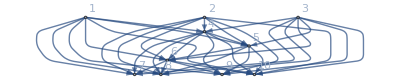

{1->4,1->5,1->6,1->7,1->8,1->9,1->10,2->4,2->5,2->6,2->7,2->8,2->9,2->10,3->4,3->5,3->6,3->7,3->8,3->9,3->10,4->5,4->6,4->7,4->8,4->9,4->10,5->6,5->8,5->9,5->10,6->7,6->8,6->9,6->10}

35

SparseArray[…]

{{0},{0},{0},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,4,5,6}}

{27,6,17}

{20,17,6,7}

{9,13,28}

{30,4,5,11}

```mathematica
m=3;
n=4;
p=3;
q=4;
H=50;
(*Crearea unui graf cu m surse, n destinatii si noduri-m-n noduri intermediare*)
(*In acest graft exista drum din fiecare sursa in fiecare destinatie*)
noduri=10;
g= Graph[
Table[i,{i,noduri}],
DeleteDuplicates@Flatten[Table[
Join[
{source->m+1},
Table[source->j,{j,RandomSample[Range[m+2,noduri]]}],
Flatten[Table[i->j,{i,m+1,noduri-n-1},{j,RandomSample[Range[i+2,noduri-n],RandomInteger[noduri-i-n-1]]}]],
Table[i->i+1,{i,m+1,noduri-1-n}],
Flatten[Table[i->j,{j,noduri-n+1,noduri},{i,RandomSample[Range[m+1,noduri-n],RandomInteger[{1,noduri-n-m}]]}]]
],{source,m}]],
VertexLabels->Automatic
]
val=Sort[EdgeList[g]] (*care arce sunt in graf*)
muchii=EdgeCount[g] (*numarul de arce*)

M=muchii*p*q;
pos = SparseArray[MapIndexed[#⟦1⟧*noduri+#⟦2⟧->#2⟦1⟧&,val]] (*Se creaza un hastable pentru a accesa pozitia unei muchii*)

(*Lista nodurilor parinti pentru fiecare nod*)
adjList=Join[Table[{0},m],Sort[Gather[val,#1[[2]]==#2[[2]]&],#1[[1,2]]<#2[[1,2]]&][[All,All,1]]]



α=Differences[Flatten[{0,Sort[RandomSample[Range[H-1],m-1]],H}]]
β=Differences[Flatten[{0,Sort[RandomSample[Range[H-1],n-1]],H}]]
γ=Differences[Flatten[{0,Sort[RandomSample[Range[H-1],p-1]],H}]]
δ=Differences[Flatten[{0,Sort[RandomSample[Range[H-1],q-1]],H}]]
```

```mathematica
(*Se creaza functiile concave de cost*)
foo=Table[RandomInteger[Range[1,2]],M]
bar=foo;
f[j_,x_]:=Piecewise[{{foo⟦j⟧ x, x≤bar⟦j⟧}, {foo⟦j⟧ bar⟦j⟧, x>bar⟦j⟧}, {0, True}}]
```

{2,2,1,1,2,2,1,2,2,1,2,1,1,1,1,2,2,2,1,2,2,1,2,2,2,1,2,1,2,1,2,2,2,2,2,1,2,2,2,2,1,1,1,2,1,1,2,1,2,2,1,1,1,2,2,2,2,2,2,2,1,2,2,2,1,2,2,1,1,2,1,1,1,2,2,2,1,1,1,2,2,1,1,2,1,1,1,2,1,2,2,1,2,1,1,2,2,2,2,1,2,1,2,1,2,2,1,1,2,2,1,1,2,2,1,2,1,1,2,2,1,2,1,1,1,2,2,1,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,2,2,1,1,2,1,2,1,1,2,1,2,2,1,2,1,2,2,2,1,1,2,1,2,1,2,2,1,1,1,2,2,1,2,2,1,2,1,2,1,1,1,2,2,1,1,2,2,1,2,1,1,1,2,2,2,2,2,2,1,1,2,1,1,2,2,2,2,1,2,1,2,1,1,1,2,1,2,2,2,1,1,2,1,2,2,1,1,1,1,1,2,1,1,2,2,1,1,1,2,2,2,2,2,2,1,2,1,1,2,1,2,2,2,2,1,1,1,2,1,2,1,1,1,1,2,2,2,1,1,2,1,1,1,1,2,2,2,1,2,1,2,2,1,2,2,1,2,1,1,1,2,1,1,1,2,2,2,2,1,1,1,1,2,1,1,2,2,1,1,2,1,2,1,2,1,2,1,1,1,1,2,2,1,1,1,2,2,1,2,2,1,1,1,1,2,1,2,2,1,1,2,1,2,2,2,2,1,2,2,1,2,1,1,1,2,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,2,1,2,2,2,2,1,2,1,1,1,1,2,1,2,2,2,2,1,2,2,2,1,1,1,1,2,2,1,2,1,2,1,2,2,1,1,1,2}

```mathematica
Do[
Print[Style["Test ","Section"],Style[bigCount,"Section"]];
thisTimer=Timing[
(*Variabile necesare pentru algoritm*)
nrIteratii=10;

(*Se afla nodurile in care se poate ajunge din sursa i*)
subtrees=Table[VertexList@FindSpanningTree[{g,i}],{i,m}];

Print["------------------------------------------------------------------"];
Print["Virfurile ce pot fi atinse din fiecare sursa  ",subtrees];
(*Se creaza populatia intiala. Fiecare cromozom va fi format din {valoarea functiei, arborii din fiecare sursa, ordinea surselor, ordinea destinatiilor, ordinea transporturilor, ordinea produselor}*)
Print["------------------------------------------------------------------"];
Print["Populatia initiala"];
chromosomes=Table[
{
0,
Table[Table[RandomChoice[Intersection[adjList⟦i⟧,subtrees⟦j⟧]]->i,{i,Drop[subtrees⟦j⟧,1]}],{j,m}],
RandomSample[Range[m]],
RandomSample[Range[n]],
RandomSample[Range[p]],
RandomSample[Range[q]]
}
,4*noduri];
Print[chromosomes];
(*Se gaseste solutiile asociate fiecarui cromozom si functiile lor obiectiv*)
Do[
(*Maximul de flux care poate fi trimis din fiecare sursa, destinatie, transport, produs*)
curLimits={α,β,γ,δ};
(*Solutia cromozomului i*)
currentX=Table[0,muchii,p,q];
currentSol=0;
(*Fiecare arbore este evaluat aparte*)
Do[
(*Arborele este reprezentat ca un hashmap dintre nodul copil si nodul parinte*)
parents=SparseArray[chromosomes⟦i,2,source⟧[[All,2]]->chromosomes⟦i,2,source⟧[[All,1]]];
(*Se calculeaza fluxul care trebuie impins din destinatii catre sursa*)
curFlow=Table[0,noduri,p,q];
Do[
(*Se afla marimea fluxului care poate fi impins din source catre dest cu produsul k si transportul l*)
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧,curLimits⟦3,k⟧,curLimits⟦4,l⟧}];
curFlow⟦noduri-n+dest,k,l⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
curLimits⟦3,k⟧-=minVal;
curLimits⟦4,l⟧-=minVal;
,{dest,chromosomes⟦i,4⟧},{k,chromosomes⟦i,5⟧},{l,chromosomes⟦i,6⟧}];
(*Printr-un depth first search se impinge fluxul din destinatii catre sursa*)
DepthFirstScan[chromosomes⟦i,2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
(*Se afla pozitia muchiei*)
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
(*Tot fluxul din nodul curent este impins catre parinte si solutia acestui cromozom este actualizata*)
Do[
curFlow⟦parents⟦#⟧,k,l⟧+=curFlow⟦#,k,l⟧;
currentX⟦edgeId,k,l⟧+=curFlow⟦#,k,l⟧;
,{k,chromosomes⟦i,5⟧},{l,chromosomes⟦i,6⟧}];
]&)];
,{source,chromosomes⟦i,3⟧}];
(*Se afla valoarea funtiei obiectiv*)
chromosomes⟦i,1⟧=Sum[f[(j-1)*p*q+(k-1)*q+l,currentX⟦j,k,l⟧],{j,muchii},{k,chromosomes⟦i,5⟧},{l,chromosomes⟦i,6⟧}];
,{i,4*noduri}];
chromosomes=Sort[chromosomes];


Do[
Print["------------------------------------------------------------------"];
Print["Iteratia ",iteratia];
(*Sunt alesi cei mai buni parinti*)

chromosomes=Take[chromosomes,2*noduri];

(*Se creaza urmasii si urmatoarea populatie*)
chromosomes=Join[
(*Parintii nu sunt schimbati*)
chromosomes,

Print["Parintii si Urmasii"];
Flatten[Table[
(*Urmasii sunt creati prin impartirea aleatoarea a arborilor din cromozomii-parinti*)
(*Celelalte valori sunt luate de la ambii parinti*)

randPos=RandomInteger[{1,m-1}];
{
{0,Join[chromosomes⟦i,2,;;randPos⟧,chromosomes⟦i+1,2,randPos+1;;⟧],chromosomes⟦i,3⟧,chromosomes⟦i+1,4⟧,chromosomes⟦i,5⟧,chromosomes⟦i+1,6⟧},
{0,Join[chromosomes⟦i+1,2,;;randPos⟧,chromosomes⟦i,2,randPos+1;;⟧],chromosomes⟦i+1,3⟧,chromosomes⟦i,4⟧,chromosomes⟦i+1,5⟧,chromosomes⟦i,6⟧}
}
,{i,1,2*noduri,2}],1]];
(*Pentru fiecare lista de ordini din fiecare cromozom-copil mutatia se produce cu sansa de 50%*)
Do[
If[RandomInteger[100]≤50,
(*Doua pozitii sunt alese aleator si schimbate cu locurile*)
{it1,it2}=RandomSample[Range[Length@chromosomes⟦i⟧⟦j⟧],2];
chromosomes⟦i⟧⟦j⟧⟦{it1,it2}⟧=chromosomes⟦i⟧⟦j⟧⟦{it2,it1}⟧
];
,{i,2*noduri+1,4*noduri},{j,3,6}];
Print[chromosomes];
(*Se evalueaza cromozomii-copii*)
Do[
curLimits={α,β,γ,δ};
currentX=Table[0,muchii,p,q];
currentSol=0;
Do[
parents=SparseArray[chromosomes⟦i,2,source⟧[[All,2]]->chromosomes⟦i,2,source⟧[[All,1]]];
curFlow=Table[0,noduri,p,q];
Do[
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧,curLimits⟦3,k⟧,curLimits⟦4,l⟧}];
curFlow⟦noduri-n+dest,k,l⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
curLimits⟦3,k⟧-=minVal;
curLimits⟦4,l⟧-=minVal;
,{dest,chromosomes⟦i,4⟧},{k,chromosomes⟦i,5⟧},{l,chromosomes⟦i,6⟧}];

DepthFirstScan[chromosomes⟦i,2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
Do[
curFlow⟦parents⟦#⟧,k,l⟧+=curFlow⟦#,k,l⟧;
currentX⟦edgeId,k,l⟧+=curFlow⟦#,k,l⟧;
,{k,chromosomes⟦i,5⟧},{l,chromosomes⟦i,6⟧}];
]&)];
,{source,chromosomes⟦i,3⟧}];
chromosomes⟦i,1⟧=Sum[f[(j-1)*p*q+(k-1)*q+l,currentX⟦j,k,l⟧],{j,muchii},{k,chromosomes⟦i,5⟧},{l,chromosomes⟦i,6⟧}];
,{i,2*noduri+1,4*noduri}];
(*Cromozomii sunt sortati si se incepe urmatoarea iteratie*)

Print["Populatia noua"];
chromosomes=Sort[chromosomes];

Print[chromosomes];
Print["Cromozom cu cele mai bune caracteristici",chromosomes⟦1⟧];
Print["Solutia cea mai buna",getSol[chromosomes⟦1⟧]];
Print["Funtia obiectiv totala  ",Total@chromosomes⟦All,1⟧];
,{iteratia,nrIteratii}];];
Print[thisTimer];
,{bigCount,6,10}]
```

Test 6

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,5->6,4->7,6->8,5->9,1->10},{2->4,4->5,4->6,6->7,4->8,6->9,6->10},{3->4,4->5,4->6,3->7,5->8,3->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{1,3,2,4}},{0,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,4->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,6->10}},{1,2,3},{3,4,2,1},{1,3,2},{2,1,4,3}},{0,{{1->4,4->5,4->6,6->7,5->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,4->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,5->8,3->9,5->10}},{2,3,1},{1,2,3,4},{3,2,1},{4,2,3,1}},{0,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,4,1,3}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,4->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,2,1},{2,1,4,3},{2,3,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,4,3,2},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,6->7,6->8,4->9,1->10},{2->4,4->5,2->6,2->7,4->8,6->9,6->10},{3->4,3->5,3->6,6->7,6->8,6->9,6->10}},{3,2,1},{2,4,1,3},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,2,4,3},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,4->6,6->7,6->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,6->10}},{3,2,1},{3,4,1,2},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{4,2,3,1}},{0,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{1,2,3},{4,1,2,3},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,6->7,4->8,6->9,1->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,5->9,5->10}},{3,2,1},{2,1,4,3},{3,1,2},{1,2,4,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{1,3,2,4},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,1->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,6->8,5->9,4->10}},{2,3,1},{1,3,4,2},{2,1,3},{2,1,3,4}},{0,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,4->8,2->9,6->10},{3->4,4->5,3->6,3->7,5->8,3->9,5->10}},{2,1,3},{1,3,4,2},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,4->6,4->7,5->8,5->9,1->10},{2->4,4->5,5->6,2->7,6->8,6->9,4->10},{3->4,4->5,4->6,6->7,6->8,4->9,6->10}},{3,2,1},{4,3,1,2},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{2,4,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,4->7,6->8,4->9,4->10},{3->4,4->5,4->6,3->7,5->8,4->9,3->10}},{1,3,2},{4,2,3,1},{1,2,3},{3,4,2,1}},{0,{{1->4,1->5,4->6,6->7,1->8,6->9,1->10},{2->4,4->5,4->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,1,2},{3,2,4,1},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,5->10},{2->4,4->5,2->6,2->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,3->9,4->10}},{1,3,2},{2,4,3,1},{2,3,1},{3,4,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,2->6,4->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,4->10}},{2,3,1},{4,1,3,2},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,5->6,4->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,6->10},{3->4,4->5,5->6,4->7,5->8,3->9,5->10}},{3,2,1},{4,1,2,3},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,5->8,1->9,5->10},{2->4,2->5,4->6,4->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,6->9,4->10}},{2,3,1},{1,3,4,2},{3,2,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,6->7,5->8,4->9,6->10},{2->4,2->5,5->6,4->7,6->8,5->9,4->10},{3->4,4->5,5->6,4->7,6->8,6->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,2,3}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,6->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,3,4,1},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,4->6,6->7,4->8,6->9,5->10},{3->4,4->5,5->6,3->7,4->8,5->9,5->10}},{1,2,3},{2,1,4,3},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{3,2,1},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,6->8,3->9,6->10}},{2,3,1},{3,4,1,2},{3,2,1},{2,4,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{2,1,3,4},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,1,4,3},{3,1,2},{3,1,4,2}},{0,{{1->4,4->5,1->6,4->7,1->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,6->9,5->10},{3->4,4->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,1,2,4},{2,1,3},{4,2,1,3}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{37,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{38,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{39,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,4,2}},{39,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,2,3},{3,2,4,1}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{1,3,2,4},{1,2,3},{4,2,3,1}},{41,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{4,2,3,1}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{1,2,4,3}},{42,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{1,3,2,4}},{42,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{2,3,1,4}},{43,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,1,4,3},{3,1,2},{3,1,4,2}},{43,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,2,4,3},{3,2,1},{1,3,4,2}},{44,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,4,1,3}},{45,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{2,4,1,3}},{45,{{1->4,4->5,1->6,6->7,6->8,4->9,5->10},{2->4,4->5,2->6,2->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,3->9,4->10}},{1,3,2},{2,4,3,1},{2,3,1},{3,4,2,1}},{45,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{1,2,3},{4,1,2,3},{1,2,3},{3,1,4,2}},{46,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,4,3,2},{1,2,3},{4,1,3,2}},{46,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,5->8,3->9,5->10}},{2,3,1},{1,2,3,4},{3,2,1},{4,2,3,1}},{46,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,3,1},{3,2,4,1}},{46,{{1->4,4->5,4->6,4->7,5->8,4->9,6->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,3,4,1},{2,1,3},{1,3,4,2}},{47,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,4->7,6->8,4->9,4->10},{3->4,4->5,4->6,3->7,5->8,4->9,3->10}},{1,3,2},{4,2,3,1},{1,2,3},{3,4,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{1,2,4,3},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{0,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{2,3,1},{4,2,1,3},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{2,3,1,4},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,2,4,3},{3,1,2},{1,3,4,2}},{0,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,3->9,4->10}},{3,2,1},{2,3,4,1},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,4,3,2},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,5->9,6->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{3,2,1},{4,2,1,3},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,2->5,2->6,4->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,5->8,3->9,5->10}},{2,3,1},{3,2,1,4},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,6->10},{2->4,2->5,4->6,4->7,6->8,4->9,4->10},{3->4,4->5,4->6,3->7,5->8,4->9,3->10}},{2,3,1},{3,2,4,1},{2,1,3},{3,4,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,3,4,2}}}

Populatia noua

{{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,3,4,2}},{37,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{38,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{39,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,4,2}},{39,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,2,3},{3,2,4,1}},{39,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{1,3,2,4},{1,2,3},{4,2,3,1}},{41,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{4,2,3,1}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{1,2,4,3}},{42,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{1,3,2,4}},{42,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{2,3,1,4}},{43,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,1,4,3},{3,1,2},{3,1,4,2}},{43,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,2,4,3},{3,2,1},{1,3,4,2}},{44,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,4,1,3}},{45,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{2,4,1,3}},{45,{{1->4,4->5,1->6,6->7,6->8,4->9,5->10},{2->4,4->5,2->6,2->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,3->9,4->10}},{1,3,2},{2,4,3,1},{2,3,1},{3,4,2,1}},{45,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{1,2,3},{4,1,2,3},{1,2,3},{3,1,4,2}},{45,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,4,3,2},{1,3,2},{1,4,3,2}},{46,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,4,3,2},{1,2,3},{4,1,3,2}},{46,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,5->8,3->9,5->10}},{2,3,1},{1,2,3,4},{3,2,1},{4,2,3,1}},{46,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,3,1},{3,2,4,1}},{46,{{1->4,4->5,4->6,4->7,5->8,4->9,6->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,3,4,1},{2,1,3},{1,3,4,2}},{46,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,2,4,3},{3,1,2},{1,3,4,2}},{47,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,4->7,6->8,4->9,4->10},{3->4,4->5,4->6,3->7,5->8,4->9,3->10}},{1,3,2},{4,2,3,1},{1,2,3},{3,4,2,1}},{49,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,2->5,2->6,4->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,5->8,3->9,5->10}},{2,3,1},{3,2,1,4},{1,3,2},{4,2,3,1}},{49,{{1->4,4->5,1->6,6->7,6->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,4,3,1}},{49,{{1->4,4->5,4->6,4->7,5->8,4->9,6->10},{2->4,2->5,4->6,4->7,6->8,4->9,4->10},{3->4,4->5,4->6,3->7,5->8,4->9,3->10}},{2,3,1},{3,2,4,1},{2,1,3},{3,4,2,1}},{50,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{2,3,1,4},{3,2,1},{4,2,1,3}},{50,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{4,1,3,2}},{55,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{1,2,4,3},{2,3,1},{3,1,4,2}},{57,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{2,3,1},{4,2,1,3},{1,3,2},{4,1,3,2}},{57,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,5->9,6->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{3,2,1},{4,2,1,3},{3,2,1},{3,1,4,2}},{57,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{3,1,4,2}},{57,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,3->9,4->10}},{3,2,1},{2,3,4,1},{1,2,3},{3,4,2,1}},{58,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{3,1,2,4}}}

Cromozom cu cele mai bune caracteristici{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,2,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,3,0},{0,0,0,11},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,2,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{15,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1772

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,3,4,2}},{37,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{38,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{39,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,4,2}},{39,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,2,3},{3,2,4,1}},{39,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{1,3,2,4},{1,2,3},{4,2,3,1}},{41,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{4,2,3,1}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{1,2,4,3}},{42,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{1,3,2,4}},{42,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{2,3,1,4}},{43,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,1,4,3},{3,1,2},{3,1,4,2}},{43,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,2,4,3},{3,2,1},{1,3,4,2}},{44,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,4,1,3}},{45,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{2,4,1,3}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{1,3,2,4},{1,3,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,2,3},{3,2,4,1},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,2,1,3},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{2,3,4,1},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{0,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{1,3,2},{3,2,4,1},{1,2,3},{1,2,4,3}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{1,3,2},{3,4,2,1},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,4,2},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{1,3,2,4},{1,2,3},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,2,4,3},{3,1,2},{1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{1,3,2},{2,4,1,3},{3,2,1},{3,1,4,2}},{0,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{1,3,2},{3,2,4,1},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{2,4,1,3},{3,1,2},{2,3,1,4}}}

Populatia noua

{{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{36,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,3,4,2}},{37,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{38,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{39,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,4,2}},{39,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,2,3},{3,2,4,1}},{39,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{1,3,2,4},{1,2,3},{4,2,3,1}},{41,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{4,2,3,1}},{42,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,2,4,3},{3,1,2},{1,3,4,2}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{1,2,4,3}},{42,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{1,3,2,4}},{42,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{2,3,1,4}},{43,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,1,4,3},{3,1,2},{3,1,4,2}},{43,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,2,4,3},{3,2,1},{1,3,4,2}},{44,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{1,3,2,4},{1,3,2},{4,3,2,1}},{44,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,4,1,3}},{45,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{2,3,4,1},{2,3,1},{3,2,4,1}},{45,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{2,4,1,3}},{47,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{1,3,2},{3,2,4,1},{1,2,3},{1,2,4,3}},{47,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,5->10},{3->4,3->5,4->6,4->7,5->8,6->9,5->10}},{1,3,2},{2,4,1,3},{3,2,1},{3,1,4,2}},{48,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{1,3,2},{3,4,2,1},{2,1,3},{4,2,1,3}},{50,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,4,2},{3,1,2},{1,2,3,4}},{51,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,4,1}},{52,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,2,3},{3,2,4,1},{1,2,3},{3,1,4,2}},{52,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{1,3,2},{3,2,4,1}},{53,{{1->4,4->5,5->6,4->7,4->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,3->9,6->10}},{1,3,2},{3,2,4,1},{3,1,2},{4,2,1,3}},{54,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,2,1,3},{1,3,2},{2,1,4,3}},{55,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,3,1},{4,3,1,2}},{57,{{1->4,4->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{1,3,2,4},{1,2,3},{1,3,2,4}},{62,{{1->4,4->5,1->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{2,4,1,3},{3,1,2},{2,3,1,4}}}

Cromozom cu cele mai bune caracteristici{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,2,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,3,0},{0,0,0,11},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,2,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{15,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1691

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{36,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,3,4,2}},{37,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{38,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{39,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,4,2}},{39,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,2,3},{3,2,4,1}},{39,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{1,3,2,4},{1,2,3},{4,2,3,1}},{41,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{4,2,3,1}},{42,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,2,4,3},{3,1,2},{1,3,4,2}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{1,2,4,3}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{1,2,3},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{2,4,1,3},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{2,1,3,4},{2,3,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,2,3},{3,1,2,4},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,2,3},{3,4,2,1},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,1,2},{1,3,2},{3,2,1,4}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,3,4,1},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,1,2},{3,2,4,1},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,2,4,1},{1,3,2},{2,1,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,2,3},{2,3,1,4},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{4,3,2,1},{3,1,2},{1,2,4,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}}}

Populatia noua

{{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,4,3,1}},{35,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{36,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,3,4,2}},{37,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{37,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,2,3},{3,4,2,1},{1,2,3},{3,1,4,2}},{37,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{4,3,2,1},{3,1,2},{1,2,4,3}},{37,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{38,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{39,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,4,2}},{39,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,2,3},{3,2,4,1}},{39,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,6->10},{3->4,4->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,4,2}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{1,3,2,4},{1,2,3},{4,2,3,1}},{40,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,2,3},{3,1,2,4},{3,2,1},{3,2,1,4}},{40,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,6->8,5->9,5->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,1,2},{3,2,4,1},{1,2,3},{3,1,4,2}},{41,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{4,2,3,1}},{42,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,2,4,3},{3,1,2},{1,3,4,2}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{1,2,4,3}},{43,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{2,4,1,3},{3,2,1},{4,2,3,1}},{44,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,1,2},{1,3,2},{3,2,1,4}},{45,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,3,4,1},{2,1,3},{1,3,4,2}},{45,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{1,2,3},{3,4,1,2}},{48,{{1->4,1->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,1,3,2}},{48,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,2,3},{2,3,1,4},{3,2,1},{3,1,4,2}},{49,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{2,1,3,4},{2,3,1},{4,3,2,1}},{54,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,1,4,2}},{61,{{1->4,4->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{3,2,4,1},{1,3,2},{2,1,4,3}}}

Cromozom cu cele mai bune caracteristici{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,2,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,3,0},{0,0,0,11},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,2,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{15,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1551

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,4,3,1}},{35,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{36,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,3,4,2}},{37,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{37,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,2,3},{3,4,2,1},{1,2,3},{3,1,4,2}},{37,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{4,3,2,1},{3,1,2},{1,2,4,3}},{37,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,3,2},{1,4,3,2},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,2,3},{3,2,4,1},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,4,2,3},{2,3,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{3,2,4,1},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{3,4,2,1},{2,1,3},{3,4,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{2,4,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,3,4}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{3,1,4,2},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,1,2},{2,1,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,1,2},{3,4,2,1},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,2,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{3,2,1},{3,4,2,1},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{1,3,2},{2,3,4,1},{1,3,2},{2,1,4,3}}}

Populatia noua

{{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{34,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,4,3,1}},{35,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,3,2},{1,4,3,2},{1,2,3},{3,2,4,1}},{36,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{36,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,3,4,2}},{37,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{37,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,2,3},{3,4,2,1},{1,2,3},{3,1,4,2}},{37,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{3,2,1},{4,3,2,1},{3,1,2},{1,2,4,3}},{37,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{38,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,4->8,5->9,5->10}},{1,2,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{39,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{3,4,2,1},{2,1,3},{3,4,2,1}},{41,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{42,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{3,1,4,2},{2,1,3},{4,2,3,1}},{43,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{2,3,4,1}},{43,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{3,2,4,1},{3,2,1},{3,1,2,4}},{44,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,3,4}},{44,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,1,2},{2,1,4,3}},{49,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{1,3,2},{3,4,1,2}},{49,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{3,2,1},{3,4,2,1},{3,1,2},{3,2,1,4}},{50,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,2,3},{3,2,4,1},{1,3,2},{2,4,3,1}},{50,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{2,4,1,3}},{51,{{1->4,1->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,5->9,5->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,1,2},{3,4,2,1},{3,1,2},{4,1,3,2}},{52,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,4,2,3},{2,3,1},{3,2,1,4}},{52,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,3->10}},{1,3,2},{2,3,4,1},{1,3,2},{2,1,4,3}}}

Cromozom cu cele mai bune caracteristici{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}}

Solutia cea mai buna{{{3,0,0,0},{13,0,0,0},{8,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,3}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,4,5,8}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{9,0,0,0},{8,0,0,0}},{{2,0,0,0},{4,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1522

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{34,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,4,3,1}},{35,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,3,2},{1,4,3,2},{1,2,3},{3,2,4,1}},{36,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{4,2,1,3},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,4,3},{2,1,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,4,2,3},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,4,2,3},{3,1,2},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,3,2,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,3,2},{2,3,1,4},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{2,1,4,3},{1,3,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,1,3},{3,4,1,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{3,2,1},{2,4,3,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,2,1,3},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{2,1,3,4},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,1,2},{1,4,2,3},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,4,3,2},{3,2,1},{3,2,4,1}}}

Populatia noua

{{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{4,3,2,1}},{34,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,4,3,1}},{35,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{36,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,3,2},{1,4,3,2},{1,2,3},{3,2,4,1}},{36,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{37,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,3,2},{4,3,2,1},{2,1,3},{3,4,1,2}},{38,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,1,4,3}},{39,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{3,2,1},{2,4,3,1}},{41,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{1,3,2},{2,3,1,4}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{4,2,1,3},{3,2,1},{4,3,2,1}},{42,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{3,1,2,4}},{43,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,4,2,3},{3,1,2},{3,1,2,4}},{43,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,3,2,1}},{43,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,4,3,2},{3,2,1},{3,2,4,1}},{44,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{3,1,2},{3,2,4,1}},{45,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,3,1},{1,4,3,2}},{46,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{2,1,4,3},{1,3,2},{4,3,2,1}},{46,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,4,2,3},{3,2,1},{1,4,2,3}},{47,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,4,3},{2,1,3},{2,3,4,1}},{49,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{2,1,3,4},{3,2,1},{4,3,2,1}},{52,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,1,2},{1,4,2,3},{3,2,1},{3,1,4,2}},{59,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,3,2},{2,3,1,4},{1,3,2},{3,1,4,2}},{61,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,2,1,3},{2,3,1},{2,4,3,1}}}

Cromozom cu cele mai bune caracteristici{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}}

Solutia cea mai buna{{{3,0,0,0},{13,0,0,0},{8,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,3}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,4,5,8}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{9,0,0,0},{8,0,0,0}},{{2,0,0,0},{4,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1531

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{4,3,2,1}},{34,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,4,3,1}},{35,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,3,2,4},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,4,3,2},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{2,1,3},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{1,2,3},{4,3,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,3,2},{3,4,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{1,3,4,2},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{3,4,2,1},{2,1,3},{1,2,4,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,4,1,2}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{3,2,1,4},{3,1,2},{4,3,2,1}}}

Populatia noua

{{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{4,3,2,1}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{3,4,2,1},{2,1,3},{1,2,4,3}},{34,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,4,3,1}},{35,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,3,2,1}},{36,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{1,3,4,2},{2,3,1},{1,4,3,2}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,3,4,1}},{39,{{1->4,1->5,4->6,1->7,1->8,6->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{3,2,1,4},{3,1,2},{4,3,2,1}},{39,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,3,4,1}},{39,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,3,2},{3,4,2,1}},{41,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,3,2,4},{1,2,3},{2,3,1,4}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{42,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{2,1,3},{4,1,2,3}},{43,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{3,4,1,2}},{45,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,3,1,4}},{45,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{1,2,3},{4,3,2,1}},{45,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,2,4,3},{2,1,3},{1,4,2,3}},{46,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,2,3}},{48,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{3,2,1},{2,3,4,1}},{50,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,4,3,2},{3,2,1},{3,2,4,1}},{55,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{2,3,1,4}},{57,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,4,1,2}}}

Cromozom cu cele mai bune caracteristici{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,3,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{5,0,0,0},{0,0,0,0},{8,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,4,2,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{4,0,0,0},{13,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,2,4}},{{0,0,0,0},{0,0,0,0},{0,4,3,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1474

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{4,3,2,1}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{3,4,2,1},{2,1,3},{1,2,4,3}},{34,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{4,2,1,3},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{3,2,1},{1,4,2,3},{3,2,1},{1,2,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,1,2,3},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,1,2,3},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,1,2},{4,3,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{4,2,1,3},{2,1,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{4,3,1,2},{3,2,1},{3,4,1,2}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{2,4,1,3},{3,2,1},{3,4,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{3,2,4,1},{1,2,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,3,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,1,3},{1,2,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{1,4,3,2},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,3,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}}}

Populatia noua

{{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,1,4}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{29,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{4,3,2,1}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{3,4,2,1},{2,1,3},{1,2,4,3}},{34,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,1,2},{4,3,2,1}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,4,1,2}},{36,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{3,4,2,1},{2,1,3},{1,2,4,3}},{37,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{1,4,3,2},{2,1,3},{4,3,1,2}},{37,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,1,2,3},{3,1,2},{1,2,3,4}},{38,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{3,2,1},{1,2,3,4}},{38,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,3,2,1}},{42,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,3,1},{3,2,4,1}},{44,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{3,2,4,1},{1,2,3},{1,2,3,4}},{45,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,1,2,3},{2,1,3},{3,2,1,4}},{49,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,2,3},{2,4,3,1}},{52,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,1,3},{2,4,1,3},{3,2,1},{3,4,2,1}},{52,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{4,2,1,3},{2,1,3},{1,4,3,2}},{53,{{1->4,1->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,3,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{53,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{4,3,1,2},{3,2,1},{3,4,1,2}},{55,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{3,2,1},{1,4,2,3},{3,2,1},{1,2,4,3}},{57,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,1,3},{4,2,1,3},{2,1,3},{3,1,4,2}}}

Cromozom cu cele mai bune caracteristici{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,3,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{5,0,0,0},{0,0,0,0},{8,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,4,2,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{4,0,0,0},{13,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,2,4}},{{0,0,0,0},{0,0,0,0},{0,4,3,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1459

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,1,4}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{29,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{3,4,1,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,3,1},{1,3,4,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,2,1},{2,1,4,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{4,3,1,2},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{1,4,2,3},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{3,1,4,2}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,3,1},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{3,4,2,1},{2,1,3},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,2,1},{1,2,3,4},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{2,3,4,1},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,3,2},{4,3,1,2},{3,2,1},{3,4,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{2,1,4,3},{1,3,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,2,3},{4,1,2,3},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{1,2,3},{1,3,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{4,3,1,2},{3,1,2},{4,3,1,2}}}

Populatia noua

{{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,1,4}},{26,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{3,2,1,4}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{3,4,1,2},{3,1,2},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{29,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,2,3,4}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{32,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,3,2},{3,4,1,2}},{33,{{1->4,1->5,1->6,1->7,4->8,4->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{2,1,4,3},{1,3,2},{4,1,2,3}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,3,1},{1,3,4,2},{3,1,2},{2,3,4,1}},{33,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{2,1,4,3},{3,1,2},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{2,1,3},{4,3,2,1}},{34,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{4,3,1,2},{1,3,2},{2,3,4,1}},{36,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,5->10}},{1,2,3},{4,1,2,3},{3,2,1},{3,2,1,4}},{36,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,2,1},{2,1,4,3}},{36,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,2,1},{3,4,2,1},{2,1,3},{1,3,2,4}},{40,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{41,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{3,1,4,2}},{43,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,3,1},{1,2,3},{2,4,3,1}},{44,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{1,4,2,3},{3,2,1},{3,2,1,4}},{45,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,4->7,4->8,5->9,5->10}},{2,1,3},{2,3,4,1},{2,3,1},{1,4,3,2}},{51,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,2,1},{1,2,3,4},{3,1,2},{4,1,2,3}},{53,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{1,2,3},{1,3,2,4}},{53,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{4,3,1,2},{3,1,2},{4,3,1,2}},{64,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,3,2},{4,3,1,2},{3,2,1},{3,4,1,2}}}

Cromozom cu cele mai bune caracteristici{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,2,3,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{24,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{3,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{2,4,3,0},{0,0,2,5},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{17,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1377

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,1,4}},{26,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{3,2,1,4}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{3,4,1,2},{3,1,2},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{29,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,2,3,4}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,1,2,3},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{4,2,3,1},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,1,2,3},{1,2,3},{1,3,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{4,2,1,3},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{3,1,4,2},{3,2,1},{2,1,4,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,2,4,3},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{2,1,3},{2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{1,4,2,3},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{2,4,1,3},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{3,2,1},{3,4,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{4,1,2,3},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,3,2},{1,3,2,4},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{3,2,1},{1,3,2,4}}}

Populatia noua

{{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{2,4,1,3},{3,1,2},{1,2,3,4}},{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,1,4}},{26,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{3,2,1,4}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{4,2,3,1},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{3,4,1,2},{3,1,2},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{29,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{29,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{29,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{2,1,3},{2,3,4,1}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,1,2},{1,4,3,2}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,2,3,4}},{31,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,2,1}},{32,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{3,1,4,2}},{34,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,3,2},{1,3,2,4},{2,1,3},{3,2,4,1}},{34,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,1,4}},{34,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{2,3,1},{1,4,3,2}},{37,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,1,2,3},{3,1,2},{1,2,3,4}},{39,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{3,2,1},{3,4,2,1}},{41,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{2,3,4,1}},{41,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,1,2,3},{1,2,3},{1,3,2,4}},{42,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{1,4,2,3},{3,2,1},{3,2,1,4}},{44,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,2,4,3},{3,1,2},{1,2,3,4}},{46,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,4,3}},{46,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{4,1,2,3},{1,2,3},{4,2,3,1}},{49,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{4,2,1,3},{3,2,1},{3,2,1,4}},{51,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{3,1,4,2},{3,2,1},{2,1,4,3}},{63,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,4,2,3},{3,2,1},{1,3,2,4}}}

Cromozom cu cele mai bune caracteristici{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{2,4,1,3},{3,1,2},{1,2,3,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{24,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{3,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{2,4,3,0},{0,0,2,5},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{17,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1339

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{2,4,1,3},{3,1,2},{1,2,3,4}},{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,1,4}},{26,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{3,2,1,4}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{4,2,3,1},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{3,4,1,2},{3,1,2},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{29,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{29,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{29,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{2,1,3},{2,3,4,1}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,2,1,3},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{1,4,2,3},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{2,4,1,3},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,4,3},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,1,2,3},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{3,4,1,2},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{4,2,3,1},{2,1,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,2,1},{1,3,2,4},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{2,3,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,3,2},{1,4,2,3},{2,1,3},{1,4,2,3}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,4,3,2},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,2,3},{3,2,1,4},{3,1,2},{4,1,3,2}}}

Populatia noua

{{22,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{3,2,4,1}},{22,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{2,4,1,3},{3,1,2},{1,2,3,4}},{23,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{25,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,1,2},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,1,4}},{26,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{3,2,1,4}},{27,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{1,2,3,4},{3,2,1},{2,3,4,1}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{4,2,3,1},{2,1,3},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{4,2,3,1},{3,2,1},{1,2,3,4}},{28,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{3,4,1,2},{3,1,2},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{1,2,3},{2,3,4,1}},{29,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{29,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{2,3,4,1}},{29,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,3,2},{1,4,2,3},{2,1,3},{4,2,3,1}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{3,1,2},{1,2,4,3}},{30,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{2,1,3},{2,3,4,1}},{30,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,1,4,2}},{30,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{3,2,1,4}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{3,4,1,2},{3,2,1},{2,3,4,1}},{32,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,3->10}},{1,3,2},{1,4,2,3},{2,1,3},{1,4,2,3}},{34,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,3,1},{1,2,3,4},{2,1,3},{4,3,2,1}},{36,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,2,4,3},{1,2,3},{2,3,4,1}},{38,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,6->9,4->10}},{3,2,1},{1,3,2,4},{3,2,1},{2,3,4,1}},{38,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{39,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{2,3,4,1}},{41,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{1,2,3},{4,2,1,3},{1,3,2},{1,2,3,4}},{43,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,1,2,3},{3,2,1},{1,3,2,4}},{45,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,2,4,3},{3,2,1},{2,3,4,1}},{49,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{2,3,1,4}},{56,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,6->9,6->10}},{2,1,3},{2,4,1,3},{3,1,2},{4,2,1,3}},{58,{{1->4,1->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,2->6,4->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,6->9,3->10}},{3,2,1},{1,4,3,2},{3,1,2},{3,2,1,4}},{60,{{1->4,4->5,5->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,6->7,3->8,6->9,6->10}},{1,2,3},{3,2,1,4},{3,1,2},{4,1,3,2}}}

Cromozom cu cele mai bune caracteristici{22,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,3,0,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{5,0,0,0},{0,0,0,0},{8,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,1,5,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{4,0,0,0},{13,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,2,0,4}},{{0,0,0,0},{0,0,0,0},{0,2,5,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1308

{2.125,Null}

Test 7

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,4->6,6->7,6->8,5->9,1->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{3,2,4,1},{2,3,1},{3,4,2,1}},{0,{{1->4,1->5,4->6,4->7,5->8,5->9,4->10},{2->4,2->5,2->6,4->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,5->6,6->7,6->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,3->10}},{3,1,2},{1,2,4,3},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,6->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,6->10}},{1,3,2},{1,2,4,3},{1,2,3},{1,4,3,2}},{0,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,4->7,2->8,4->9,4->10},{3->4,4->5,5->6,3->7,5->8,3->9,4->10}},{1,2,3},{4,3,1,2},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,5->6,4->7,4->8,6->9,1->10},{2->4,2->5,2->6,2->7,6->8,5->9,4->10},{3->4,4->5,4->6,3->7,5->8,5->9,4->10}},{2,3,1},{2,3,4,1},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,4->7,1->8,5->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{1,3,2},{2,1,4,3},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,4->6,4->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,4->8,6->9,4->10},{3->4,4->5,5->6,6->7,5->8,4->9,6->10}},{3,2,1},{2,3,1,4},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,1->6,6->7,1->8,6->9,1->10},{2->4,4->5,5->6,6->7,6->8,5->9,6->10},{3->4,4->5,3->6,4->7,4->8,6->9,4->10}},{1,3,2},{2,4,1,3},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,6->9,4->10}},{1,2,3},{2,3,4,1},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{1,3,2},{2,3,4,1},{3,2,1},{4,3,1,2}},{0,{{1->4,1->5,4->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,6->7,4->8,4->9,5->10},{3->4,3->5,4->6,6->7,4->8,3->9,6->10}},{2,3,1},{3,1,2,4},{1,3,2},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10},{2->4,4->5,5->6,4->7,6->8,4->9,2->10},{3->4,4->5,3->6,6->7,5->8,5->9,4->10}},{3,2,1},{2,3,1,4},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,4->6,4->7,4->8,3->9,4->10}},{2,1,3},{4,2,3,1},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,5->6,6->7,6->8,1->9,4->10},{2->4,2->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,3->9,6->10}},{2,3,1},{3,2,4,1},{2,1,3},{4,2,3,1}},{0,{{1->4,4->5,5->6,6->7,6->8,6->9,5->10},{2->4,2->5,4->6,2->7,5->8,4->9,2->10},{3->4,4->5,4->6,6->7,6->8,4->9,3->10}},{2,3,1},{3,4,2,1},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,6->8,3->9,4->10}},{3,1,2},{2,4,1,3},{2,1,3},{4,1,2,3}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,6->7,5->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,2->9,5->10},{3->4,3->5,5->6,6->7,3->8,6->9,4->10}},{2,3,1},{1,3,2,4},{2,3,1},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,1->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{2,1,3},{4,2,3,1},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,3->10}},{1,2,3},{3,4,1,2},{1,2,3},{1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{1,4,3,2},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,2->7,6->8,6->9,6->10},{3->4,4->5,5->6,6->7,4->8,4->9,6->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,2->10},{3->4,4->5,5->6,4->7,3->8,5->9,6->10}},{1,3,2},{2,4,1,3},{2,1,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,4->7,6->8,6->9,4->10}},{3,1,2},{3,1,2,4},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,4->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,6->9,4->10}},{2,1,3},{2,1,3,4},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,5->6,4->7,1->8,4->9,6->10},{2->4,2->5,5->6,2->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,4->10}},{3,2,1},{3,1,2,4},{1,2,3},{4,3,2,1}},{0,{{1->4,1->5,5->6,1->7,6->8,1->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,6->7,3->8,6->9,4->10}},{1,2,3},{4,3,2,1},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{1,3,2},{2,1,4,3},{1,3,2},{2,1,4,3}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,5->8,6->9,5->10}},{1,3,2},{1,4,3,2},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,4->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,4,3,2}},{0,{{1->4,4->5,4->6,4->7,6->8,6->9,1->10},{2->4,4->5,2->6,4->7,2->8,4->9,2->10},{3->4,4->5,4->6,6->7,3->8,3->9,6->10}},{2,3,1},{1,2,3,4},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{4,3,1,2}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,1->6,6->7,6->8,5->9,6->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,2,1},{4,2,3,1},{1,3,2},{1,3,2,4}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{1,3,2},{2,1,4,3},{1,3,2},{2,1,4,3}},{36,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{1,4,3,2},{2,1,3},{4,3,2,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{1,3,2},{2,3,4,1},{3,2,1},{4,3,1,2}},{37,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,1,2},{2,3,4,1}},{41,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{2,4,3,1}},{43,{{1->4,4->5,5->6,4->7,1->8,4->9,6->10},{2->4,2->5,5->6,2->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,4->10}},{3,2,1},{3,1,2,4},{1,2,3},{4,3,2,1}},{44,{{1->4,1->5,4->6,6->7,1->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{2,1,3},{4,2,3,1},{1,2,3},{4,2,3,1}},{44,{{1->4,4->5,4->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,4->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,4,3,2}},{47,{{1->4,4->5,1->6,4->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,5->8,6->9,5->10}},{1,3,2},{1,4,3,2},{2,3,1},{4,1,2,3}},{48,{{1->4,1->5,4->6,4->7,1->8,5->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{1,3,2},{2,1,4,3},{2,3,1},{1,4,2,3}},{49,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,4->7,6->8,6->9,4->10}},{3,1,2},{3,1,2,4},{3,2,1},{3,2,1,4}},{49,{{1->4,4->5,1->6,6->7,6->8,5->9,6->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,2,1},{4,2,3,1},{1,3,2},{1,3,2,4}},{50,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,4->6,4->7,4->8,3->9,4->10}},{2,1,3},{4,2,3,1},{2,3,1},{2,4,1,3}},{50,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{4,3,1,2}},{50,{{1->4,4->5,4->6,6->7,6->8,5->9,1->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{3,2,4,1},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{1,2,3},{2,4,1,3},{2,3,1},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,4,3},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,1,3},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{1,3,2},{4,3,1,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{1,3,4,2}},{0,{{1->4,4->5,5->6,4->7,1->8,4->9,6->10},{2->4,2->5,5->6,2->7,2->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{1,2,3},{4,2,3,1},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,6->7,1->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,4->10}},{2,1,3},{3,2,1,4},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,5->8,6->9,5->10}},{3,1,2},{1,4,3,2},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,5->10},{2->4,4->5,5->6,4->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,5->9,3->10}},{1,3,2},{3,1,2,4},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,4->7,1->8,5->9,6->10},{2->4,2->5,5->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,4->7,6->8,6->9,4->10}},{1,2,3},{3,4,2,1},{2,3,1},{4,2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{4,1,2,3},{3,2,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,4->6,4->7,4->8,3->9,4->10}},{3,2,1},{2,4,3,1},{1,3,2},{2,4,1,3}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,1,3},{1,3,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,4->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,6->10}},{3,1,2},{3,4,1,2},{2,3,1},{4,3,1,2}}}

Populatia noua

{{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{1,2,3,4}},{33,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,4,3},{1,3,2},{4,1,3,2}},{34,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,1,3},{1,3,2,4}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{1,3,2},{2,1,4,3},{1,3,2},{2,1,4,3}},{36,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{1,4,3,2},{2,1,3},{4,3,2,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{1,3,2},{2,3,4,1},{3,2,1},{4,3,1,2}},{37,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,1,2},{2,3,4,1}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{1,3,2},{4,3,1,2},{3,1,2},{2,3,4,1}},{41,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{2,4,3,1}},{43,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{4,1,2,3},{3,2,1},{1,4,3,2}},{43,{{1->4,4->5,5->6,4->7,1->8,4->9,6->10},{2->4,2->5,5->6,2->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,4->10}},{3,2,1},{3,1,2,4},{1,2,3},{4,3,2,1}},{44,{{1->4,1->5,4->6,6->7,1->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{2,1,3},{4,2,3,1},{1,2,3},{4,2,3,1}},{44,{{1->4,4->5,4->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,4->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,4,3,2}},{45,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,1,3},{4,3,1,2}},{46,{{1->4,4->5,4->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,6->10}},{3,1,2},{3,4,1,2},{2,3,1},{4,3,1,2}},{47,{{1->4,4->5,1->6,4->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,5->8,6->9,5->10}},{1,3,2},{1,4,3,2},{2,3,1},{4,1,2,3}},{48,{{1->4,1->5,4->6,4->7,1->8,5->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{1,3,2},{2,1,4,3},{2,3,1},{1,4,2,3}},{48,{{1->4,4->5,4->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,5->8,6->9,5->10}},{3,1,2},{1,4,3,2},{3,1,2},{4,1,2,3}},{48,{{1->4,4->5,5->6,4->7,1->8,4->9,6->10},{2->4,2->5,5->6,2->7,2->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{1,2,3},{4,2,3,1},{3,2,1},{3,2,4,1}},{49,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,4->7,6->8,6->9,4->10}},{3,1,2},{3,1,2,4},{3,2,1},{3,2,1,4}},{49,{{1->4,4->5,1->6,6->7,6->8,5->9,6->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,2,1},{4,2,3,1},{1,3,2},{1,3,2,4}},{50,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,4->6,4->7,4->8,3->9,4->10}},{2,1,3},{4,2,3,1},{2,3,1},{2,4,1,3}},{50,{{1->4,4->5,1->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,4->6,4->7,4->8,3->9,4->10}},{3,2,1},{2,4,3,1},{1,3,2},{2,4,1,3}},{50,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{4,3,1,2}},{50,{{1->4,4->5,4->6,6->7,6->8,5->9,1->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{3,2,4,1},{2,3,1},{3,4,2,1}},{53,{{1->4,1->5,4->6,6->7,1->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,5->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,4->10}},{2,1,3},{3,2,1,4},{3,2,1},{2,3,4,1}},{55,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{1,2,3},{2,4,1,3},{2,3,1},{2,3,1,4}},{55,{{1->4,4->5,1->6,4->7,5->8,1->9,5->10},{2->4,4->5,5->6,4->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,5->9,3->10}},{1,3,2},{3,1,2,4},{1,3,2},{2,4,3,1}},{56,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{1,3,4,2}},{62,{{1->4,1->5,4->6,4->7,1->8,5->9,6->10},{2->4,2->5,5->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,4->7,6->8,6->9,4->10}},{1,2,3},{3,4,2,1},{2,3,1},{4,2,1,3}}}

Cromozom cu cele mai bune caracteristici{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{15,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{1,0,5,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,9},{2,4,0,2},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,9},{2,4,0,2},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1651

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{1,2,3,4}},{33,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,4,3},{1,3,2},{4,1,3,2}},{34,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,1,3},{1,3,2,4}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{1,3,2},{2,1,4,3},{1,3,2},{2,1,4,3}},{36,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{1,4,3,2},{2,1,3},{4,3,2,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{1,3,2},{2,3,4,1},{3,2,1},{4,3,1,2}},{37,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,1,2},{2,3,4,1}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{1,3,2},{4,3,1,2},{3,1,2},{2,3,4,1}},{41,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{2,4,3,1}},{43,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{4,1,2,3},{3,2,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{2,1,3},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,3,4},{2,3,1},{3,4,1,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{1,2,4,3},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,4,2,1}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,3,1,2},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,3,4,2},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,1,2},{4,2,1,3},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{3,2,1,4},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,3,1},{4,3,2,1}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,4,3,2},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{1,3,2},{2,3,1,4},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,4,3},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{3,2,1},{3,4,2,1}}}

Populatia noua

{{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{1,2,3,4}},{33,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,4,3},{1,3,2},{4,1,3,2}},{34,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,1,3},{1,3,2,4}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{1,3,2},{2,1,4,3},{1,3,2},{2,1,4,3}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,3,1},{4,3,2,1}},{35,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,4,3},{1,3,2},{1,4,3,2}},{35,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{3,2,1},{4,2,1,3}},{35,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,1,2},{4,2,1,3},{1,3,2},{2,3,1,4}},{36,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{1,4,3,2},{2,1,3},{4,3,2,1}},{36,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,3,1,2},{2,3,1},{2,3,4,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,4,3,2},{3,1,2},{4,3,2,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{1,3,2},{2,3,4,1},{3,2,1},{4,3,1,2}},{37,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,1,2},{2,3,4,1}},{39,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,4,2,1}},{39,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,2,4,3}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{1,3,2},{4,3,1,2},{3,1,2},{2,3,4,1}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{1,3,2},{2,3,1,4},{1,3,2},{2,3,1,4}},{41,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{2,4,3,1}},{41,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{1,2,4,3},{2,3,1},{3,1,4,2}},{43,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,4,1,3}},{43,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,4->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{4,3,2,1}},{43,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,3,4},{2,3,1},{3,4,1,2}},{43,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{4,1,2,3},{3,2,1},{1,4,3,2}},{45,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{2,1,3},{4,2,1,3}},{47,{{1->4,4->5,1->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{3,2,1},{3,4,2,1}},{52,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,3,4,2},{1,2,3},{4,1,3,2}},{52,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{3,2,1,4},{1,3,2},{1,4,3,2}},{54,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,4->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{3,1,2},{2,3,4,1}}}

Cromozom cu cele mai bune caracteristici{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{5,4,0,11}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{9,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{4,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1460

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{1,2,3,4}},{33,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,4,3},{1,3,2},{4,1,3,2}},{34,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,1,3},{1,3,2,4}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{1,3,2},{2,1,4,3},{1,3,2},{2,1,4,3}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,3,1},{4,3,2,1}},{35,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,4,3},{1,3,2},{1,4,3,2}},{35,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{3,2,1},{4,2,1,3}},{35,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,1,2},{4,2,1,3},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{2,4,3,1},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{2,3,1},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,4,3},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{2,4,1,3},{1,3,2},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{4,2,1,3},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,3,1,4},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,2,1},{2,1,4,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,4,3},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{4,2,3,1},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{3,1,2},{4,3,1,2}}}

Populatia noua

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{32,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,4,3},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{1,2,3,4}},{33,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{3,2,4,1}},{33,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,4,3},{1,3,2},{4,1,3,2}},{34,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,1,3},{1,3,2,4}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{1,3,2},{2,1,4,3},{1,3,2},{2,1,4,3}},{34,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,3,1},{2,3,1},{4,3,2,1}},{35,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,2,1},{2,1,4,3},{2,1,3},{3,1,4,2}},{35,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,4,3},{1,3,2},{1,4,3,2}},{35,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{3,2,1},{4,2,1,3}},{35,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,4,3},{1,2,3},{4,1,3,2}},{35,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,1,2},{4,2,1,3},{1,3,2},{2,3,1,4}},{36,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{2,4,1,3},{1,3,2},{1,3,2,4}},{36,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{3,1,2},{4,3,1,2}},{36,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{38,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,3,1,4},{1,3,2},{1,2,3,4}},{39,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,2,3}},{41,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{4,2,3,1},{1,3,2},{4,3,2,1}},{42,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{2,3,1},{3,1,4,2}},{43,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{4,2,1,3},{1,2,3},{4,1,3,2}},{43,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{4,3,1,2}},{46,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{2,4,3,1},{1,2,3},{3,1,4,2}},{56,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,4,1,2}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{4,4,5,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,3},{0,0,0,0},{12,0,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1334

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{32,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,4,3},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{1,2,3,4}},{33,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{2,4,1,3},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,3,1},{2,1,4,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,2,3},{3,2,4,1},{2,3,1},{3,4,2,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,2,4,3},{3,1,2},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,3,2},{4,2,3,1},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,2,1,4},{3,1,2},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,3,4,2},{1,3,2},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,1,2},{2,4,1,3},{3,2,1},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,4,1,3},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,4,2,3},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{1,2,4,3}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,2,1},{4,2,3,1}}}

Populatia noua

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{29,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,1,3,2}},{32,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,4,3},{2,3,1},{1,4,3,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{1,2,3,4}},{33,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,3,1,4}},{39,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,2,3,4}},{41,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,2,1,3}},{42,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,2,3},{3,2,4,1},{2,3,1},{3,4,2,1}},{42,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{3,1,4,2}},{43,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{1,2,4,3}},{43,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,1,2},{2,4,1,3},{3,2,1},{4,3,1,2}},{44,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,2,4,3},{3,1,2},{4,3,1,2}},{44,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,2,1,4},{3,1,2},{4,3,1,2}},{46,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,3,1},{2,1,4,3},{2,1,3},{3,1,4,2}},{47,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,4,2,3},{3,2,1},{3,1,4,2}},{48,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,2,1,4},{3,2,1},{4,2,3,1}},{49,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,3,4,2},{1,3,2},{4,3,1,2}},{49,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,3,2},{4,2,3,1},{2,3,1},{3,4,2,1}},{55,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{2,4,1,3},{3,1,2},{4,2,1,3}},{59,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,4,1,3},{1,3,2},{1,4,3,2}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{4,4,5,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,3},{0,0,0,0},{12,0,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1385

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{29,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,1,3,2},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,2,4,1},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,2,1,4},{1,2,3},{1,3,2,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,2,3},{3,1,4,2},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,1,2,4},{2,1,3},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{1,2,3},{3,4,1,2},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{1,2,3},{1,2,4,3},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{1,3,2,4},{1,2,3},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,3,2},{4,2,3,1},{3,2,1},{3,4,1,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,1,3},{4,2,3,1},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{1,3,4,2},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{1,2,4,3},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,1,2},{2,4,3,1},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}}}

Populatia noua

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{29,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,4,1}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{31,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{3,1,4,2},{2,3,1},{4,2,1,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,2,1},{2,4,1,3},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{3,1,2},{2,4,3,1},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,2,4,1},{1,2,3},{3,1,4,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,4,3,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{1,3,4,2},{3,1,2},{4,2,1,3}},{36,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,1,3,2},{1,3,2},{4,2,3,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{3,1,4,2}},{36,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{1,2,3},{3,4,1,2},{3,2,1},{2,3,1,4}},{37,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,2,3},{3,1,4,2},{2,3,1},{2,4,1,3}},{38,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{4,1,3,2}},{39,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,1,3},{4,2,3,1},{2,3,1},{3,4,2,1}},{42,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{1,2,3},{1,2,4,3},{2,1,3},{4,3,1,2}},{43,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,2,1,4},{1,2,3},{1,3,2,4}},{43,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,1,2},{3,2,1,4}},{44,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{1,2,4,3},{2,3,1},{1,4,3,2}},{45,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,3,2},{4,2,3,1},{3,2,1},{3,4,1,2}},{46,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{1,3,2,4},{1,2,3},{4,2,1,3}},{46,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,1,2,4},{2,1,3},{1,2,3,4}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{4,4,5,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,3},{0,0,0,0},{12,0,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1266

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{29,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,4,1}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,1,4},{1,2,3},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{3,2,1,4},{2,1,3},{1,2,4,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,4,1},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,4,1},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,1,2},{1,2,4,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,4,1},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,3,2},{4,2,3,1},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{1,2,3,4},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,1,3},{4,2,1,3},{1,2,3},{3,4,1,2}}}

Populatia noua

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,3,2}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,4,1},{1,2,3},{1,2,3,4}},{29,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,4,2}},{29,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{3,1,2},{3,2,4,1}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,4,1}},{30,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{3,4,2,1}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{1,3,2},{4,1,3,2}},{32,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,1,4},{1,2,3},{2,1,3,4}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{1,3,2,4}},{33,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,4,1},{1,2,3},{1,2,3,4}},{35,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{37,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{4,3,1,2}},{38,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,1,2},{1,2,4,3},{2,1,3},{3,1,4,2}},{38,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,4,1},{2,1,3},{2,3,1,4}},{39,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{3,2,1,4},{2,1,3},{1,2,4,3}},{39,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{3,2,1},{4,3,2,1}},{39,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{1,2,4,3},{1,2,3},{4,3,1,2}},{44,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,1,3},{4,2,1,3},{1,2,3},{3,4,1,2}},{49,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{2,4,1,3}},{49,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,3,2},{4,2,3,1},{3,2,1},{3,2,4,1}},{61,{{1->4,4->5,4->6,1->7,4->8,5->9,6->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{1,2,3,4},{3,1,2},{4,1,3,2}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{4,4,5,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,3},{0,0,0,0},{12,0,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1227

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,3,2}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{1,2,4,3},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{2,3,1},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,2,4,1},{1,3,2},{1,3,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{2,1,3,4},{1,3,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,3,1},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,2,4,1},{2,1,3},{1,4,3,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,3,1},{4,2,1,3},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,1,4,2},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{2,1,3,4},{1,3,2},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{1,2,3},{3,4,1,2}}}

Populatia noua

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{2,3,1,4}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,3,2,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,3,2}},{26,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{2,3,1},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{2,3,1},{4,2,3,1},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,2,1,3}},{29,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,3,1},{1,2,3,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,2,4,1},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,1,4,2},{1,2,3},{4,2,3,1}},{32,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{4,3,2,1}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,2,4,1},{1,3,2},{1,3,4,2}},{35,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{1,2,4,3},{1,2,3},{4,1,3,2}},{35,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,2,1,3}},{37,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{2,1,3,4},{1,3,2},{4,2,1,3}},{37,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{1,2,4,3},{2,3,1},{3,1,4,2}},{39,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{1,3,2},{4,2,3,1}},{39,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{1,2,3},{3,4,1,2}},{41,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{1,2,3},{4,3,1,2}},{41,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,3->8,3->9,3->10}},{2,3,1},{4,2,1,3},{2,3,1},{4,3,1,2}},{43,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,2,3,1}},{49,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{2,1,3,4},{1,3,2},{4,1,2,3}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{4,4,5,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,3},{0,0,0,0},{12,0,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1149

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{2,3,1,4}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,3,2,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,3,2}},{26,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{4,3,1,2},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,1,4,2},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{1,3,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,1,4,2},{2,3,1},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,2,1},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{2,3,4,1},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{2,3,4,1},{1,2,3},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,1,2},{4,1,2,3},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{1,2,3},{3,2,4,1},{3,2,1},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,2,1},{2,3,1,4},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{1,2,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{2,1,3},{1,2,3,4}}}

Populatia noua

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{2,3,1,4}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,3,2,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,2,1},{2,3,1,4},{3,2,1},{1,3,2,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,3,2}},{26,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,3,1,4}},{26,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,2,3,4}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{2,1,4,3},{1,2,3},{3,1,4,2}},{28,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{2,1,3},{1,2,3,4}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,2,1},{1,3,2},{3,1,4,2}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,1,4,2},{2,3,1},{2,1,3,4}},{32,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,1,2},{4,1,2,3},{1,2,3},{3,1,4,2}},{32,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{2,3,4,1},{1,2,3},{4,3,1,2}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,5->8,4->9,4->10}},{1,2,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{33,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{2,3,4,1},{1,2,3},{1,2,4,3}},{34,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,2,1,4}},{35,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{1,3,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{35,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,1,4,2},{3,2,1},{4,1,3,2}},{36,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{1,2,3},{3,2,4,1},{3,2,1},{4,3,1,2}},{39,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{4,3,1,2},{1,3,2},{3,1,4,2}},{40,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,4,1}},{45,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,6->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{3,1,4,2}},{45,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,2,3,1}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{4,4,5,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,3},{0,0,0,0},{12,0,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1112

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{2,3,1,4}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,3,2,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,2,1},{2,3,1,4},{3,2,1},{1,3,2,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{2,3,4,1},{3,1,2},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{4,3,1,2},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,2,3},{2,1,4,3},{3,1,2},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,2,1},{2,1,4,3},{2,1,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{4,3,1,2},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{3,2,4,1},{2,1,3},{4,3,2,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,1,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{3,2,4,1},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{2,3,1,4},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,2,3},{2,4,1,3},{3,1,2},{3,1,2,4}}}

Populatia noua

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{2,3,1,4}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{21,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{2,3,1,4}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{24,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{4,3,1,2},{3,2,1},{3,2,4,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{1,3,4,2}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,3,2,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{3,2,1},{2,3,1,4},{3,2,1},{1,3,2,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,4,2,1}},{26,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{28,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,1,3,4}},{28,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{4,3,1,2}},{30,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{3,2,1},{2,1,4,3},{2,1,3},{3,2,4,1}},{30,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{2,3,1},{4,1,3,2}},{33,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{4,1,3,2}},{33,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,4,1}},{34,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{2,3,1,4},{3,1,2},{1,2,3,4}},{35,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,2,3},{2,4,1,3},{3,1,2},{3,1,2,4}},{37,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,2,3},{2,1,4,3},{3,1,2},{4,3,1,2}},{38,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{4,3,1,2},{1,2,3},{3,2,4,1}},{40,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{2,3,4,1},{3,1,2},{3,1,4,2}},{42,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{3,2,4,1},{3,2,1},{1,3,2,4}},{44,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,3,4}},{48,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{3,2,4,1},{2,1,3},{4,3,2,1}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{4,4,5,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,3},{0,0,0,0},{12,0,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,6},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1093

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{2,3,1,4}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{21,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{2,3,1,4}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{24,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{4,3,1,2},{3,2,1},{3,2,4,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{1,3,4,2}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,1,4,2},{1,3,2},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,1,4,2},{1,3,2},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{2,1,4,3},{1,3,2},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{1,2,3},{3,2,4,1},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,2,1},{1,3,2},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{2,1,3},{2,4,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{2,1,3},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,4,2,1},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{4,3,2,1},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{4,1,3,2},{2,1,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{2,3,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,3,1,2},{2,1,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,4,3,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}}}

Populatia noua

{{16,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{17,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{2,3,1,4}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{3,1,4,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,3,2},{4,3,1,2}},{21,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{2,3,1},{1,3,2,4}},{21,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{2,3,1,4}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{2,1,3},{2,4,1,3}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{3,1,4,2}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,4,2}},{23,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{1,2,3},{4,2,1,3}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{3,2,4,1}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,2,4,1},{1,2,3},{4,3,1,2}},{24,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{4,3,2,1}},{24,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{4,3,1,2},{3,2,1},{3,2,4,1}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{3,2,4,1}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{1,3,4,2}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,3,2},{2,1,4,3},{1,3,2},{4,2,1,3}},{27,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,2,1},{2,1,4,3},{2,1,3},{2,4,1,3}},{27,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,2,3},{4,1,3,2},{2,1,3},{3,2,4,1}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{4,3,1,2},{2,1,3},{3,2,4,1}},{30,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,4->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{1,4,3,2}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{1,2,3},{3,2,4,1},{1,2,3},{4,3,1,2}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,2,1},{1,3,2},{2,1,4,3}},{31,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,3->7,5->8,3->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,1,4,2}},{33,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,1,4,2},{1,3,2},{4,1,3,2}},{36,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{4,3,1,2}},{37,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{4,3,2,1},{1,2,3},{3,2,4,1}},{39,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{2,3,1},{3,1,4,2},{1,3,2},{1,3,2,4}},{39,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,1,4}},{40,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{3,2,4,1}},{42,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,4,2,1},{1,2,3},{4,3,1,2}},{55,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,6->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{4,3,2,1}}}

Cromozom cu cele mai bune caracteristici{16,{{1->4,4->5,4->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{10,0,0,0}},{{0,0,0,0},{0,0,0,0},{17,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,3},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,4},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,2,0,0},{0,0,0,4},{0,0,0,0}},{{0,2,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1077

{1.95313,Null}

Test 8

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,4->7,5->8,4->9,5->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,4->9,5->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,5->10},{2->4,2->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,4->7,6->8,4->9,6->10}},{3,2,1},{3,2,1,4},{2,3,1},{3,1,2,4}},{0,{{1->4,1->5,4->6,6->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,5->8,6->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,4->10}},{1,3,2},{1,4,3,2},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,5->8,3->9,6->10}},{3,1,2},{4,3,1,2},{1,3,2},{4,2,1,3}},{0,{{1->4,4->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,4->6,2->7,4->8,6->9,5->10},{3->4,4->5,5->6,6->7,4->8,6->9,3->10}},{3,2,1},{2,3,4,1},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,4->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,5->9,5->10},{3->4,4->5,4->6,6->7,4->8,5->9,4->10}},{3,2,1},{1,4,2,3},{1,3,2},{3,4,1,2}},{0,{{1->4,4->5,5->6,4->7,1->8,6->9,1->10},{2->4,2->5,4->6,4->7,5->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{1,4,3,2},{1,2,3},{1,3,2,4}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,6->7,5->8,4->9,6->10},{2->4,2->5,2->6,6->7,5->8,5->9,6->10},{3->4,4->5,3->6,3->7,6->8,4->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,4->8,4->9,5->10},{3->4,4->5,5->6,3->7,4->8,6->9,4->10}},{3,1,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,6->9,6->10},{3->4,3->5,3->6,3->7,4->8,4->9,6->10}},{2,1,3},{1,2,4,3},{1,2,3},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{2,4,1,3},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,4->6,6->7,5->8,1->9,4->10},{2->4,2->5,4->6,2->7,6->8,4->9,2->10},{3->4,3->5,4->6,6->7,4->8,6->9,4->10}},{1,2,3},{2,3,1,4},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,6->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,5->6,4->7,6->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,2,3,4},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,4->7,2->8,6->9,6->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{2,3,1},{2,1,4,3},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,6->10},{2->4,4->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,1->6,4->7,6->8,5->9,4->10},{2->4,2->5,4->6,4->7,4->8,4->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{4,1,2,3},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,4->6,6->7,5->8,4->9,5->10},{2->4,4->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,5->6,3->7,6->8,3->9,6->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,1,3,4}},{0,{{1->4,4->5,5->6,6->7,5->8,6->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,5->10},{3->4,3->5,5->6,6->7,5->8,3->9,4->10}},{3,2,1},{3,1,4,2},{2,3,1},{3,4,1,2}},{0,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,6->8,5->9,6->10},{2->4,2->5,4->6,2->7,2->8,2->9,2->10},{3->4,3->5,3->6,4->7,3->8,5->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,4->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,5->10},{3->4,4->5,5->6,6->7,6->8,6->9,5->10}},{3,1,2},{2,3,4,1},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,3,2},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,6->7,1->8,6->9,1->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,6->7,4->8,6->9,4->10}},{3,1,2},{1,4,2,3},{2,1,3},{2,1,3,4}},{0,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{2,1,4,3},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{0,{{1->4,4->5,1->6,4->7,5->8,6->9,1->10},{2->4,2->5,4->6,2->7,4->8,4->9,6->10},{3->4,4->5,4->6,4->7,4->8,5->9,3->10}},{1,3,2},{3,2,1,4},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,5->6,1->7,6->8,1->9,5->10},{2->4,4->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,4->7,3->8,5->9,5->10}},{1,3,2},{3,2,1,4},{2,1,3},{2,3,1,4}},{0,{{1->4,4->5,5->6,6->7,4->8,6->9,1->10},{2->4,2->5,5->6,4->7,4->8,6->9,5->10},{3->4,4->5,4->6,6->7,5->8,6->9,4->10}},{1,2,3},{1,2,4,3},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,4->10},{3->4,4->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,2,1,3},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,1->8,6->9,1->10},{2->4,2->5,4->6,4->7,4->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,2,1},{4,2,1,3},{3,2,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,4->6,4->7,5->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,5->9,3->10}},{1,3,2},{3,1,2,4},{2,1,3},{2,4,3,1}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{39,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{41,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,1,4}},{41,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{2,4,1,3}},{41,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{2,1,3},{2,4,3,1}},{43,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{1,2,3,4}},{44,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{2,4,1,3},{2,3,1},{1,4,2,3}},{44,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,3,2},{1,2,3},{4,1,3,2}},{45,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{2,1,4,3},{3,1,2},{2,3,4,1}},{46,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,4->10},{3->4,4->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,2,1,3},{3,1,2},{4,1,3,2}},{46,{{1->4,4->5,1->6,4->7,1->8,4->9,6->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,4,3}},{47,{{1->4,1->5,4->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,4->7,2->8,6->9,6->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{2,3,1},{2,1,4,3},{3,1,2},{1,2,3,4}},{49,{{1->4,4->5,4->6,6->7,5->8,1->9,4->10},{2->4,2->5,4->6,2->7,6->8,4->9,2->10},{3->4,3->5,4->6,6->7,4->8,6->9,4->10}},{1,2,3},{2,3,1,4},{3,2,1},{1,3,2,4}},{50,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,5->8,3->9,6->10}},{3,1,2},{4,3,1,2},{1,3,2},{4,2,1,3}},{50,{{1->4,4->5,1->6,4->7,6->8,5->9,4->10},{2->4,2->5,4->6,4->7,4->8,4->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{4,1,2,3},{2,3,1},{3,2,4,1}},{50,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,4->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{3,4,2,1}},{50,{{1->4,4->5,5->6,4->7,6->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,2,3,4},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,1,3},{2,1,3,4},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{3,1,2},{4,3,2,1},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{2,3,1},{2,1,3,4},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{1,2,3},{2,4,1,3},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{3,4,1,2},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,1,4,3},{1,2,3},{4,3,2,1}},{0,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,4->10},{3->4,4->5,3->6,3->7,6->8,3->9,6->10}},{3,2,1},{4,2,1,3},{3,2,1},{2,1,3,4}},{0,{{1->4,1->5,4->6,4->7,6->8,6->9,5->10},{2->4,2->5,4->6,2->7,6->8,4->9,2->10},{3->4,3->5,4->6,6->7,4->8,6->9,4->10}},{3,2,1},{2,3,1,4},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,4->6,6->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,2->8,6->9,6->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,3,2},{2,1,4,3},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,4->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{4,1,2,3},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,4->7,6->8,5->9,4->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,5->8,3->9,6->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,5->6,4->7,6->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,3,2,4},{2,3,1},{3,4,2,1}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,2,3,4}},{39,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{41,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,1,4}},{41,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{3,4,1,2},{3,2,1},{3,2,1,4}},{41,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{2,4,1,3}},{41,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{2,1,3},{2,4,3,1}},{42,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,1,3},{2,1,3,4},{2,1,3},{2,3,4,1}},{43,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{1,2,3,4}},{44,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{2,4,1,3},{2,3,1},{1,4,2,3}},{44,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,3,2},{1,2,3},{4,1,3,2}},{44,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{45,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{4,1,3,2}},{45,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{2,1,4,3},{3,1,2},{2,3,4,1}},{46,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,4->10},{3->4,4->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,2,1,3},{3,1,2},{4,1,3,2}},{46,{{1->4,4->5,1->6,4->7,1->8,4->9,6->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,4,3}},{46,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{3,1,2},{4,3,2,1},{2,1,3},{3,1,4,2}},{47,{{1->4,1->5,4->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,4->7,2->8,6->9,6->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{2,3,1},{2,1,4,3},{3,1,2},{1,2,3,4}},{47,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,4->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{4,1,2,3},{2,3,1},{3,2,4,1}},{48,{{1->4,1->5,4->6,4->7,6->8,6->9,5->10},{2->4,2->5,4->6,2->7,6->8,4->9,2->10},{3->4,3->5,4->6,6->7,4->8,6->9,4->10}},{3,2,1},{2,3,1,4},{1,3,2},{1,4,2,3}},{48,{{1->4,4->5,4->6,6->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,2->8,6->9,6->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,3,2},{2,1,4,3},{3,2,1},{1,3,2,4}},{49,{{1->4,4->5,4->6,6->7,5->8,1->9,4->10},{2->4,2->5,4->6,2->7,6->8,4->9,2->10},{3->4,3->5,4->6,6->7,4->8,6->9,4->10}},{1,2,3},{2,3,1,4},{3,2,1},{1,3,2,4}},{50,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{2,3,1},{2,1,3,4},{3,2,1},{4,1,2,3}},{50,{{1->4,1->5,4->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,5->8,3->9,6->10}},{3,1,2},{4,3,1,2},{1,3,2},{4,2,1,3}},{50,{{1->4,4->5,1->6,4->7,1->8,4->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,4->10},{3->4,4->5,3->6,3->7,6->8,3->9,6->10}},{3,2,1},{4,2,1,3},{3,2,1},{2,1,3,4}},{50,{{1->4,4->5,1->6,4->7,6->8,5->9,4->10},{2->4,2->5,4->6,4->7,4->8,4->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{4,1,2,3},{2,3,1},{3,2,4,1}},{50,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,4->5,4->6,3->7,5->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{3,4,2,1}},{50,{{1->4,4->5,5->6,4->7,6->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,2,3,4},{2,3,1},{3,2,4,1}},{50,{{1->4,4->5,5->6,4->7,6->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,2->10},{3->4,4->5,4->6,3->7,5->8,6->9,6->10}},{2,3,1},{1,3,2,4},{2,3,1},{3,4,2,1}},{51,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,1,4,3},{1,2,3},{4,3,2,1}},{51,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,4,2,3}},{60,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{1,2,3},{2,4,1,3},{2,3,1},{2,4,3,1}},{65,{{1->4,4->5,1->6,4->7,6->8,5->9,4->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,5->8,3->9,6->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,2,1,3}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1755

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,2,3,4}},{39,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{41,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,1,4}},{41,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{3,4,1,2},{3,2,1},{3,2,1,4}},{41,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{2,4,1,3}},{41,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{2,1,3},{2,4,3,1}},{42,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,1,3},{2,1,3,4},{2,1,3},{2,3,4,1}},{43,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{1,2,3,4}},{44,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{2,4,1,3},{2,3,1},{1,4,2,3}},{44,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,3,2},{1,2,3},{4,1,3,2}},{44,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{45,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,2,1},{4,1,2,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{1,3,2},{3,4,2,1}},{0,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{3,1,2},{3,1,4,2},{2,1,3},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,3,1},{1,2,3,4},{3,2,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{3,4,1,2},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,3,1},{1,3,4,2},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{2,3,1},{2,4,1,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{3,4,1,2},{2,1,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{3,1,2,4},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{1,2,3},{2,4,1,3},{1,2,3},{1,4,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,3,2},{3,1,2},{4,3,1,2}},{0,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,4,2,1},{3,1,2},{3,4,2,1}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,1,4,3}},{37,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,2,1},{4,1,2,3}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,2,3,4}},{38,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,4,3,1}},{39,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{40,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{1,3,2},{3,4,2,1}},{41,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,1,4}},{41,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{3,4,1,2},{3,2,1},{3,2,1,4}},{41,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{2,4,1,3}},{41,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{2,1,3},{2,4,3,1}},{42,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,1,3},{2,1,3,4},{2,1,3},{2,3,4,1}},{43,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,3,1},{1,2,3,4},{3,2,1},{4,2,3,1}},{43,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{1,2,3,4}},{43,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,3,2},{3,1,2},{4,3,1,2}},{44,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{2,4,1,3},{2,3,1},{1,4,2,3}},{44,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,3,2},{1,2,3},{4,1,3,2}},{44,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{45,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{4,1,3,2}},{45,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,4,2,1},{2,3,1},{3,1,4,2}},{47,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{2,3,1},{4,2,3,1}},{50,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{3,4,1,2},{2,1,3},{1,2,3,4}},{50,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{4,1,3,2}},{51,{{1->4,4->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{3,1,2,4},{2,3,1},{2,3,4,1}},{52,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{3,4,1,2},{3,1,2},{4,2,1,3}},{53,{{1->4,4->5,4->6,4->7,1->8,1->9,1->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,4,2,1},{3,1,2},{3,4,2,1}},{54,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{3,1,2},{3,1,4,2},{2,1,3},{2,1,3,4}},{55,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{2,4,3,1}},{56,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,6->7,6->8,6->9,5->10}},{1,2,3},{2,4,1,3},{1,2,3},{1,4,2,3}},{56,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{2,3,1},{2,4,1,3}},{77,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,3,1},{1,3,4,2},{3,2,1},{4,2,1,3}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1692

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,1,4,3}},{37,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,2,1},{4,1,2,3}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,2,3,4}},{38,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,4,3,1}},{39,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{40,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{1,3,2},{3,4,2,1}},{41,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,1,4}},{41,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{3,4,1,2},{3,2,1},{3,2,1,4}},{41,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{2,4,1,3}},{41,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,3,2},{2,1,4,3},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{2,1,3},{2,1,3,4},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{4,3,1,2},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{1,3,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{4,2,3,1},{3,1,2},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{3,2,1},{4,1,3,2},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,3,4},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,3,1},{1,2,4,3},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{1,4,3,2},{2,1,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,3,1},{4,3,1,2},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{1,3,2},{2,4,3,1},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{1,2,3},{2,4,1,3}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{2,3,1},{2,4,3,1}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,1,4,3}},{37,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,2,1},{4,1,2,3}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{2,4,3,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,2,3,4}},{38,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,4,3,1}},{39,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{40,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{1,3,2},{3,4,2,1}},{40,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,3,1},{4,3,1,2},{3,2,1},{3,2,1,4}},{41,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,1,2},{3,2,1,4}},{41,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,3,1},{3,4,1,2},{3,2,1},{3,2,1,4}},{41,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{2,4,1,3}},{41,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{2,1,3},{2,4,3,1}},{43,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,3,2},{2,1,4,3},{3,1,2},{3,2,4,1}},{47,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{1,4,2,3}},{47,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{3,1,2},{2,1,4,3}},{48,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,3,1},{1,2,4,3},{3,1,2},{4,1,3,2}},{49,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{4,3,1,2},{1,3,2},{3,1,4,2}},{50,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{53,{{1->4,4->5,5->6,1->7,1->8,4->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{1,3,2},{2,4,3,1},{2,3,1},{2,4,3,1}},{54,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{1,3,2},{1,2,4,3}},{54,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,3,4},{2,1,3},{3,1,4,2}},{55,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{4,2,3,1},{3,1,2},{4,1,3,2}},{56,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,1,4,3}},{57,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{2,1,3},{2,1,3,4},{2,1,3},{4,1,2,3}},{58,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,6->9,5->10}},{2,1,3},{1,4,3,2},{2,1,3},{3,2,1,4}},{61,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{3,2,1},{4,1,3,2},{1,3,2},{1,4,3,2}},{66,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,5->9,4->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{1,2,3},{2,4,1,3}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1662

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{2,3,1},{2,4,3,1}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,1,4,3}},{37,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,2,1},{4,1,2,3}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{2,4,3,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,2,3,4}},{38,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,4,3,1}},{39,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{40,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,3,2},{1,2,3,4},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{4,1,2,3},{3,2,1},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,2,1},{2,1,4,3},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{4,2,1,3},{3,2,1},{2,4,3,1}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,2,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{3,1,2},{4,1,3,2},{2,3,1},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{2,3,4,1},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1,4},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,2,3,1}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,1,2},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{2,3,1},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,2,3},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{2,3,1},{2,4,3,1}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,1,4,3}},{37,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,2,1},{4,1,2,3}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{2,4,3,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,2,3,4}},{38,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,4,3,1}},{39,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,4,3}},{39,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{39,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{4,1,2,3},{3,2,1},{4,3,1,2}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,2,3,1}},{39,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{39,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,2,1},{2,1,4,3},{2,1,3},{2,1,4,3}},{40,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{1,3,2},{3,4,2,1}},{40,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{2,1,3},{2,1,4,3}},{47,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{3,1,2},{3,2,4,1}},{48,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,5->9,6->10}},{3,1,2},{4,1,3,2},{2,3,1},{1,2,3,4}},{49,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,2,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{49,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,3,2},{1,2,3,4},{3,2,1},{3,2,4,1}},{53,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,1,3},{1,2,3,4},{1,3,2},{4,2,3,1}},{54,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,2->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{1,3,2},{2,3,4,1},{1,2,3},{2,1,4,3}},{56,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1,4},{2,3,1},{2,3,4,1}},{57,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{4,2,1,3},{3,2,1},{2,4,3,1}},{57,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{3,1,4,2}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1513

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,1,2},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{2,3,1},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,2,3},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{2,3,1},{2,4,3,1}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,1,4,3}},{37,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,2,1},{4,1,2,3}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,2,3},{1,3,4,2},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,3,4,2},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{3,1,2,4},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,3,2},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{2,3,1},{2,1,3,4},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,1,4,2},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,4,1,2},{3,1,2},{3,1,2,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{1,2,3},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{3,2,1},{1,3,2,4},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,3,1},{1,2,3,4},{3,1,2},{4,2,3,1}},{0,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{2,1,3},{1,4,2,3}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,4,2,1}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,1,2},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{2,3,1},{2,4,3,1}},{33,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{3,1,2,4},{2,3,1},{4,1,3,2}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,2,3},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{2,3,1},{2,4,3,1}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,1,4,3}},{37,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,2,1},{4,1,2,3}},{38,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,3,2},{4,3,2,1}},{39,{{1->4,1->5,1->6,4->7,6->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{2,1,3},{1,4,2,3}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{2,3,1},{2,1,3,4},{3,1,2},{4,1,2,3}},{40,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,3,4,2},{2,3,1},{2,3,4,1}},{40,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{3,4,2,1}},{40,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,2,3},{1,3,4,2},{3,1,2},{3,2,4,1}},{42,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{2,3,1},{1,2,3,4},{3,1,2},{4,2,3,1}},{43,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,4,1}},{46,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,4->10}},{3,2,1},{1,3,2,4},{2,3,1},{2,1,4,3}},{49,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{2,3,1},{2,4,1,3}},{50,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,1,4,2},{3,2,1},{1,4,2,3}},{55,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,3,2},{4,1,3,2}},{61,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,4,1,2},{3,1,2},{3,1,2,4}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1414

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,4,2,1}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,1,2},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,3,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,1,2,3},{2,1,3},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,2,1},{4,1,2,3},{1,3,2},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{2,1,3,4},{1,3,2},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{1,4,2,3}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{1,3,2},{3,4,2,1},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{2,3,1,4},{3,2,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{2,3,4,1},{2,3,1},{2,4,3,1}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,2,1},{4,1,3,2}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,3,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,4,2,1}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{2,1,3,4},{1,3,2},{4,1,2,3}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,3,2},{3,2,4,1},{3,1,2},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,1,3,4},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,2,4,1}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{2,1,3},{3,4,1,2},{1,3,2},{3,1,4,2}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,1,2,3},{2,1,3},{1,4,2,3}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,2,4},{2,3,1},{2,4,3,1}},{34,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,2,3,1}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{3,2,1},{4,3,2,1}},{36,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{37,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{2,3,1,4},{3,2,1},{3,4,2,1}},{37,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,3,2},{1,2,4,3},{3,1,2},{3,2,4,1}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{41,{{1->4,4->5,4->6,1->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{1,4,2,3}},{42,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{3,2,4,1}},{43,{{1->4,1->5,4->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{1,3,2},{4,2,3,1}},{49,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,2,1},{4,1,2,3},{1,3,2},{4,1,3,2}},{50,{{1->4,4->5,5->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,3->10}},{1,3,2},{3,4,2,1},{1,2,3},{3,1,4,2}},{51,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{2,3,4,1},{2,3,1},{2,4,3,1}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1304

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,2,1},{4,1,3,2}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,3,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,4,2,1}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,2,3},{1,2,4,3},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,2,3},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,2,1,3},{2,1,3},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,1,3,2},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{2,3,4,1},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,2,1},{3,2,4,1},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{1,2,3},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,4,1},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,2,1},{1,4,2,3},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,2,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,2,1},{1,2,4,3},{3,2,1},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,2,3,4},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{3,1,4,2},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,3,1},{1,3,2,4},{2,3,1},{4,3,1,2}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,2,3,4},{1,3,2},{3,4,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,2,1},{4,1,3,2}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,3,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,4,2,1}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{31,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{2,3,4,1},{1,3,2},{3,4,2,1}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{3,1,4,2},{3,1,2},{2,3,4,1}},{34,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,4->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{3,2,1,4},{3,2,1},{2,3,4,1}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,1,3,2},{1,3,2},{1,4,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{1,2,3},{2,1,4,3}},{37,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,2,3},{4,3,2,1}},{37,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{4,1,2,3}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{1,3,2},{4,2,3,1}},{40,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,2,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{42,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,2,1},{3,2,4,1},{2,3,1},{1,4,2,3}},{45,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,2,3},{1,2,4,3},{1,2,3},{3,2,4,1}},{46,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,2,1,3},{2,1,3},{2,4,1,3}},{47,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,2,1},{1,2,4,3},{3,2,1},{3,1,4,2}},{50,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{2,3,1},{4,3,1,2}},{50,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{3,2,1},{1,4,2,3},{1,2,3},{3,1,4,2}},{59,{{1->4,4->5,5->6,1->7,6->8,6->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,3,1},{1,3,2,4},{2,3,1},{4,3,1,2}},{67,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,4,1},{2,1,3},{2,4,3,1}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1358

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,2,3,4},{1,3,2},{3,4,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,2,1},{4,1,3,2}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,3,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{3,2,4,1},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,3,1},{3,1,2,4},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{1,3,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{1,3,2},{1,3,4,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{2,1,4,3},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,2,3,4},{1,3,2},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,4,3,2},{3,2,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,2,4,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,2,3,4},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,3,1},{1,4,2,3},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{4,2,3,1},{3,2,1},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{2,4,1,3},{1,2,3},{4,3,1,2}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1,4},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,3,4,2},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{4,2,1,3},{1,3,2},{4,1,3,2}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{2,3,1},{3,4,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{1,3,2},{1,3,4,2}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,2,3,4},{1,3,2},{3,4,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{1,3,2},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{2,3,4,1}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,2,1},{4,1,3,2}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,3,4,1}},{29,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,3,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,2,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,1,3,2}},{35,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,3,2},{1,3,4,2},{2,3,1},{1,4,3,2}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,4,3,2},{3,2,1},{3,4,2,1}},{39,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{4,3,1,2}},{45,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,2,4,1},{3,1,2},{1,4,2,3}},{45,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,3,1},{1,4,2,3},{2,3,1},{4,2,3,1}},{49,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,3,1},{3,1,2,4},{1,3,2},{4,3,2,1}},{49,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{4,2,1,3},{1,3,2},{4,1,3,2}},{51,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{3,2,4,1},{1,2,3},{3,2,4,1}},{52,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{2,1,4,3},{2,3,1},{3,4,2,1}},{53,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{2,1,3},{2,4,1,3},{1,2,3},{4,3,1,2}},{55,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1,4},{2,3,1},{2,4,3,1}},{59,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,2,3,4},{2,3,1},{3,1,2,4}},{61,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{3,1,2},{4,2,3,1},{3,2,1},{2,4,1,3}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1351

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{2,3,1},{3,4,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{1,3,2},{1,3,4,2}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,2,3,4},{1,3,2},{3,4,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{1,3,2},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{2,3,4,1}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{2,1,3,4},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{3,1,2,4},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,3,2},{1,2,4,3},{3,1,2},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,1,3,4},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{4,2,3,1},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,3,2,1},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,3,2,4},{2,3,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,2,3,4},{1,3,2},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{3,2,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,2,3}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{1,2,3,4},{2,3,1},{3,4,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,2,4},{1,3,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{2,3,1},{3,4,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{1,3,2},{1,3,4,2}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,1,3,4},{3,1,2},{1,2,4,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{25,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,3,1},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{2,1,3,4},{1,3,2},{3,4,2,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,2,3,4},{1,3,2},{3,4,2,1}},{28,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{1,3,2},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{2,3,4,1}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,2,1},{4,1,3,2}},{29,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,2,3,4},{1,3,2},{4,3,2,1}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,4->8,4->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{1,4,3,2}},{32,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{2,3,1},{3,1,2,4}},{33,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{2,4,3,1}},{34,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{4,2,3,1},{3,1,2},{2,1,4,3}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{3,2,4,1},{1,3,2},{1,4,2,3}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,4->6,6->7,4->8,2->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,2,4},{1,3,2},{4,1,2,3}},{41,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{1,2,3,4},{2,3,1},{3,4,1,2}},{44,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{3,2,1},{4,2,3,1}},{47,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,3,2,4},{2,3,1},{1,3,4,2}},{47,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{1,3,2},{1,2,4,3},{3,1,2},{3,1,4,2}},{57,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{3,1,2,4},{1,3,2},{1,4,2,3}},{60,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,3,2,1},{1,3,2},{3,1,2,4}},{60,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,1,4,2},{1,3,2},{4,1,2,3}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1253

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{2,3,1},{3,4,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{1,3,2},{1,3,4,2}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,1,3,4},{3,1,2},{1,2,4,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{25,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,3,1},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{2,1,3,4},{1,3,2},{3,4,2,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,2,3,4},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{2,3,1},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,3,4},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{2,1,3,4},{1,3,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,3,2,1},{3,1,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,4,2,3},{3,1,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,4,3,2},{3,2,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,4,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{1,4,3,2},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{1,3,4,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{2,4,1,3},{3,1,2},{3,4,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,3,1},{2,1,3,4},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,3,2},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{1,4,3,2},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{2,1,3,4}}}

Populatia noua

{{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,1,2,4},{2,3,1},{3,4,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,4,3},{1,3,2},{3,2,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{1,3,2},{1,3,4,2}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{2,1,3,4},{3,1,2},{1,2,4,3}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,4,2,1}},{25,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,5->9,4->10}},{3,1,2},{1,2,3,4},{3,1,2},{3,2,4,1}},{25,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,4,2,3},{3,1,2},{3,4,2,1}},{25,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,3,1},{3,4,2,1}},{26,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,3,2,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,2,3,4},{1,3,2},{2,3,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{2,4,3,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{2,1,3,4},{1,3,2},{3,4,2,1}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,1,2,4}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{3,4,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{1,3,2},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,4,3,1}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,2,3,4},{1,3,2},{3,4,2,1}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{3,2,1},{1,3,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{1,2,3},{1,4,3,2},{3,2,1},{3,4,2,1}},{31,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{2,1,3,4},{1,3,2},{1,2,4,3}},{32,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{1,4,3,2},{2,3,1},{2,4,3,1}},{33,{{1->4,1->5,5->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,4,3},{1,3,2},{4,3,1,2}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,3,2,1},{3,1,2},{3,4,2,1}},{35,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,3,1},{2,1,3,4},{2,1,3},{2,4,3,1}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,2,3},{2,4,1,3},{3,1,2},{3,4,1,2}},{36,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,2->8,5->9,5->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{2,1,3,4}},{38,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{1,3,4,2}},{41,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{1,4,3,2},{2,3,1},{3,1,2,4}},{42,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{2,3,1},{1,2,4,3}},{45,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,4,2,1}},{47,{{1->4,4->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,3,2},{1,3,2,4}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,2->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,3,2,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,4,5,4}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,7}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1151

{2.,Null}

Test 9

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,1->6,4->7,1->8,4->9,4->10},{2->4,4->5,4->6,2->7,2->8,6->9,5->10},{3->4,3->5,5->6,4->7,4->8,3->9,6->10}},{1,2,3},{3,2,4,1},{1,3,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,2->7,4->8,4->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,6->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,4,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,1->9,1->10},{2->4,4->5,4->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,4->7,5->8,6->9,4->10}},{1,3,2},{1,2,4,3},{3,1,2},{3,1,2,4}},{0,{{1->4,4->5,5->6,4->7,1->8,4->9,5->10},{2->4,2->5,4->6,6->7,5->8,5->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,4->10}},{1,3,2},{1,2,4,3},{2,3,1},{1,3,2,4}},{0,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,4->10}},{3,1,2},{3,4,1,2},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,6->7,4->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,4->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,6->10},{2->4,4->5,4->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,4->7,5->8,4->9,6->10}},{3,1,2},{3,2,4,1},{2,3,1},{3,4,1,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,3,1,2}},{0,{{1->4,1->5,4->6,4->7,6->8,6->9,1->10},{2->4,4->5,4->6,4->7,4->8,2->9,6->10},{3->4,3->5,4->6,3->7,4->8,5->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,6->9,1->10},{2->4,2->5,2->6,4->7,2->8,6->9,6->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,2,3},{1,2,4,3},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,4->7,4->8,2->9,6->10},{3->4,4->5,4->6,6->7,4->8,5->9,4->10}},{1,3,2},{4,2,1,3},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,5->6,6->7,6->8,6->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,4->6,3->7,4->8,3->9,6->10}},{1,2,3},{3,2,4,1},{2,1,3},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,5->6,4->7,4->8,6->9,6->10},{2->4,4->5,2->6,4->7,6->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,6->9,4->10}},{1,3,2},{3,2,4,1},{1,2,3},{4,2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,6->7,6->8,4->9,4->10},{3->4,3->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,2,3,1},{3,2,1},{3,4,1,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,5->8,6->9,6->10}},{3,2,1},{3,1,2,4},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,5->9,6->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{1,2,3},{4,2,3,1},{2,3,1},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,1->8,6->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{1,2,3},{3,1,2,4},{1,2,3},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{3,4,2,1}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,3,4,2},{2,3,1},{3,4,1,2}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,1->10},{2->4,4->5,5->6,6->7,6->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,5->9,6->10}},{2,1,3},{2,1,4,3},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{0,{{1->4,4->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,4->9,2->10},{3->4,4->5,3->6,4->7,4->8,6->9,4->10}},{1,2,3},{2,1,3,4},{3,1,2},{1,3,4,2}},{0,{{1->4,4->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,6->9,4->10}},{1,3,2},{4,3,1,2},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,3,2},{3,4,2,1},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,5->6,3->7,4->8,3->9,3->10}},{1,2,3},{2,4,3,1},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,5->6,6->7,4->8,6->9,4->10},{2->4,4->5,2->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{3,4,1,2},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,1->8,4->9,1->10},{2->4,4->5,4->6,4->7,5->8,2->9,6->10},{3->4,3->5,3->6,4->7,4->8,6->9,4->10}},{1,3,2},{2,3,1,4},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,1->10},{2->4,2->5,4->6,4->7,5->8,5->9,5->10},{3->4,4->5,3->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,3,4,2},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,4->7,6->8,6->9,5->10},{3->4,3->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{1,3,4,2}},{0,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,3->5,4->6,4->7,3->8,5->9,3->10}},{3,2,1},{4,1,3,2},{1,2,3},{1,3,4,2}},{0,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{3,2,1},{3,1,2,4},{2,1,3},{4,2,1,3}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{33,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{36,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,3,4,2},{2,3,1},{3,4,1,2}},{40,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{41,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,3,4,1}},{42,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,3,1,2}},{42,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{43,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{3,4,2,1}},{44,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{3,2,1},{3,1,2,4},{2,1,3},{4,2,1,3}},{44,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{2,4,1,3}},{45,{{1->4,1->5,1->6,6->7,1->8,6->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{1,2,3},{3,1,2,4},{1,2,3},{1,3,2,4}},{45,{{1->4,1->5,4->6,4->7,6->8,6->9,1->10},{2->4,4->5,4->6,4->7,4->8,2->9,6->10},{3->4,3->5,4->6,3->7,4->8,5->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,3,1,2}},{45,{{1->4,4->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,4->9,2->10},{3->4,4->5,3->6,4->7,4->8,6->9,4->10}},{1,2,3},{2,1,3,4},{3,1,2},{1,3,4,2}},{46,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,3,1,4}},{46,{{1->4,1->5,5->6,6->7,4->8,6->9,4->10},{2->4,4->5,2->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{3,4,1,2},{1,3,2},{4,2,3,1}},{48,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,6->7,4->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,4->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{2,3,1,4}},{49,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,3,2},{3,4,2,1},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{1,2,3},{2,1,4,3},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,4,3},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{1,2,4,3},{1,3,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{3,1,2},{1,3,4,2},{3,2,1},{3,4,1,2}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{3,2,1,4},{1,3,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,4,1,2},{2,1,3},{4,2,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,4,3,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,2,1,3}},{0,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,4,2},{2,1,3},{4,3,2,1}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,1,2,4},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,1->6,6->7,1->8,6->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,2,4,3},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,4->6,4->7,6->8,6->9,1->10},{2->4,4->5,4->6,4->7,4->8,2->9,6->10},{3->4,4->5,3->6,4->7,4->8,6->9,4->10}},{2,3,1},{2,1,4,3},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,4->9,2->10},{3->4,3->5,4->6,3->7,4->8,5->9,6->10}},{3,2,1},{2,4,1,3},{3,1,2},{4,3,1,2}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,5->6,6->7,4->8,6->9,4->10},{2->4,4->5,2->6,2->7,6->8,2->9,4->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{3,2,1},{3,1,4,2},{1,3,2},{2,4,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,6->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{3,1,2},{3,2,4,1},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,5->8,4->9,4->10}},{2,3,1},{2,4,1,3},{3,1,2},{2,3,1,4}}}

Populatia noua

{{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{33,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{33,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,4,1,2},{2,1,3},{4,2,1,3}},{36,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,3,4,2},{2,3,1},{3,4,1,2}},{40,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{40,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,4,2},{2,1,3},{4,3,2,1}},{41,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,3,4,1}},{42,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,1,2,4},{3,2,1},{1,3,2,4}},{42,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,3,1,2}},{42,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{43,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{3,4,2,1}},{44,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{3,2,1},{3,1,2,4},{2,1,3},{4,2,1,3}},{44,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{3,1,2},{1,3,4,2},{3,2,1},{3,4,1,2}},{44,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{2,4,1,3}},{44,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{1,2,3},{2,1,4,3},{2,1,3},{3,1,2,4}},{45,{{1->4,1->5,1->6,6->7,1->8,6->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,2,4,3},{1,2,3},{2,1,4,3}},{45,{{1->4,1->5,1->6,6->7,1->8,6->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{1,2,3},{3,1,2,4},{1,2,3},{1,3,2,4}},{45,{{1->4,1->5,4->6,4->7,6->8,6->9,1->10},{2->4,4->5,4->6,4->7,4->8,2->9,6->10},{3->4,3->5,4->6,3->7,4->8,5->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,3,1,2}},{45,{{1->4,4->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,4->9,2->10},{3->4,4->5,3->6,4->7,4->8,6->9,4->10}},{1,2,3},{2,1,3,4},{3,1,2},{1,3,4,2}},{46,{{1->4,1->5,4->6,4->7,6->8,6->9,1->10},{2->4,4->5,4->6,4->7,4->8,2->9,6->10},{3->4,4->5,3->6,4->7,4->8,6->9,4->10}},{2,3,1},{2,1,4,3},{2,1,3},{2,3,4,1}},{46,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,3,1,4}},{46,{{1->4,1->5,5->6,6->7,4->8,6->9,4->10},{2->4,4->5,2->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{3,4,1,2},{1,3,2},{4,2,3,1}},{48,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,6->7,4->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,4->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{2,3,1,4}},{48,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{1,2,4,3},{1,3,2},{1,2,4,3}},{48,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,4,3},{1,3,2},{3,4,1,2}},{49,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{2,3,4,1}},{49,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,3,2},{3,4,2,1},{3,1,2},{3,2,1,4}},{51,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{3,2,1,4},{1,3,2},{3,2,4,1}},{52,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,6->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{3,1,2},{3,2,4,1},{1,2,3},{2,3,1,4}},{53,{{1->4,1->5,5->6,6->7,4->8,6->9,4->10},{2->4,4->5,2->6,2->7,6->8,2->9,4->10},{3->4,3->5,3->6,6->7,3->8,5->9,4->10}},{3,2,1},{3,1,4,2},{1,3,2},{2,4,1,3}},{56,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,2,1,3}},{60,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,2->9,4->10},{3->4,4->5,3->6,3->7,5->8,4->9,4->10}},{2,3,1},{2,4,1,3},{3,1,2},{2,3,1,4}},{61,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{4,3,1,2}},{62,{{1->4,4->5,5->6,4->7,1->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,4->9,2->10},{3->4,3->5,4->6,3->7,4->8,5->9,6->10}},{3,2,1},{2,4,1,3},{3,1,2},{4,3,1,2}}}

Cromozom cu cele mai bune caracteristici{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{6,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{1,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{1,0,5,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,9},{0,0,0,0},{2,4,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1723

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{33,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{33,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,4,1,2},{2,1,3},{4,2,1,3}},{36,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,3,4,2},{2,3,1},{3,4,1,2}},{40,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{40,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,4,2},{2,1,3},{4,3,2,1}},{41,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,3,4,1}},{42,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,1,2,4},{3,2,1},{1,3,2,4}},{42,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,3,1,2}},{42,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{43,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{3,4,2,1}},{44,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{3,2,1},{3,1,2,4},{2,1,3},{4,2,1,3}},{44,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{3,1,2},{1,3,4,2},{3,2,1},{3,4,1,2}},{44,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,3,1},{3,1,4,2},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,1,4,2},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,2,4,3},{2,1,3},{1,4,3,2}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{3,2,1},{3,4,1,2},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{1,3,4,2},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{3,1,2},{3,1,4,2},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{3,1,2},{4,3,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,3,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{3,1,2},{3,1,2,4},{3,1,2},{2,4,1,3}},{0,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{1,3,4,2},{3,1,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,1,2},{3,1,4,2},{1,2,3},{1,4,2,3}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{3,4,2,1}}}

Populatia noua

{{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{32,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,2,3},{2,4,3,1}},{33,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{33,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,4,1,2},{2,1,3},{4,2,1,3}},{36,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,3,4,2},{2,3,1},{3,4,1,2}},{38,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,3,4}},{39,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{1,3,4,2},{2,1,3},{4,3,2,1}},{40,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{40,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,4,2},{2,1,3},{4,3,2,1}},{40,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,4,2,1}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,3,1},{3,1,4,2},{3,1,2},{4,1,2,3}},{41,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,3,4,1}},{42,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,2,4,3},{1,2,3},{3,4,2,1}},{42,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,1,2,4},{3,2,1},{1,3,2,4}},{42,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,3,1,2}},{42,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{3,2,1,4},{2,3,1},{2,4,3,1}},{43,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{3,4,2,1}},{44,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,1,4,2},{3,2,1},{3,2,4,1}},{44,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{3,2,1},{3,1,2,4},{2,1,3},{4,2,1,3}},{44,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{3,1,2},{1,3,4,2},{3,2,1},{3,4,1,2}},{44,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,4->6,4->7,6->8,2->9,6->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{2,4,1,3}},{45,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{1,3,4,2},{3,1,2},{3,4,2,1}},{45,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10},{2->4,4->5,5->6,4->7,2->8,2->9,5->10},{3->4,4->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{3,1,2},{4,3,2,1}},{45,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,6->8,6->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{2,3,1,4}},{46,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{3,1,2},{3,1,4,2},{2,3,1},{1,4,2,3}},{47,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,4->7,2->8,2->9,6->10},{3->4,3->5,4->6,3->7,5->8,5->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{3,1,2,4}},{47,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,1,2},{3,1,4,2},{1,2,3},{1,4,2,3}},{48,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,3,1,2}},{49,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{3,2,1},{3,4,1,2},{2,3,1},{4,2,3,1}},{52,{{1->4,1->5,5->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,5->6,3->7,6->8,6->9,3->10}},{3,1,2},{3,1,2,4},{3,1,2},{2,4,1,3}},{53,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,2,4,3},{2,1,3},{1,4,3,2}}}

Cromozom cu cele mai bune caracteristici{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{6,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{1,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{1,0,5,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,9},{0,0,0,0},{2,4,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1555

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{32,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,2,3},{2,4,3,1}},{33,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{33,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,4,1,2},{2,1,3},{4,2,1,3}},{36,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,3,4,2},{2,3,1},{3,4,1,2}},{38,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,3,4}},{39,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{1,3,4,2},{2,1,3},{4,3,2,1}},{40,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{40,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,4,2},{2,1,3},{4,3,2,1}},{40,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,4,2,1}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,3,1},{3,1,4,2},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,1,3},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{4,2,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{1,3,2},{1,4,3,2},{1,3,2},{2,4,1,3}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,1,2},{3,4,1,2},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{3,1,2},{4,2,1,3},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,2,3},{3,1,2,4},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{3,2,1,4},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,4,2,1},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{3,2,1},{3,4,1,2},{2,1,3},{4,3,1,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,4,2},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,2,3},{4,2,1,3},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,2,4}},{0,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{3,1,2},{4,1,3,2},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{3,1,4,2},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{1,3,2,4},{1,3,2},{2,4,3,1}}}

Populatia noua

{{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{29,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,1,3},{1,3,2},{3,1,2,4}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{32,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,2,3},{2,4,3,1}},{33,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,2,4}},{33,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{4,2,1,3}},{33,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,1,2},{3,4,1,2},{3,2,1},{4,2,3,1}},{36,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,4,1,2},{2,1,3},{4,2,1,3}},{36,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{3,1,2},{4,2,1,3},{1,3,2},{3,4,1,2}},{36,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,3,1},{1,3,4,2},{2,3,1},{3,4,1,2}},{37,{{1->4,4->5,4->6,6->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{3,2,1},{3,4,1,2},{2,1,3},{4,3,1,2}},{38,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,1,2},{3,2,1,4},{3,1,2},{2,1,3,4}},{39,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{1,3,4,2},{2,1,3},{4,3,2,1}},{40,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{40,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,4,2},{2,1,3},{4,3,2,1}},{40,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,4,2,1}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,3,1},{3,1,4,2},{3,1,2},{4,1,2,3}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{1,3,2,4},{1,3,2},{2,4,3,1}},{42,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,2,3},{3,1,2,4},{1,3,2},{2,4,3,1}},{42,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{3,1,4,2},{1,3,2},{1,4,2,3}},{43,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,1,4,3}},{43,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,4,2},{3,1,2},{4,3,2,1}},{47,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{1,3,2},{1,4,3,2},{1,3,2},{2,4,1,3}},{49,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{3,2,1,4},{3,1,2},{2,3,4,1}},{54,{{1->4,1->5,5->6,4->7,6->8,6->9,5->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{3,1,2},{4,1,3,2},{1,2,3},{2,3,1,4}},{57,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,2,3},{4,2,1,3},{2,1,3},{4,1,3,2}},{58,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,4,2,1},{1,2,3},{2,4,3,1}},{64,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{3,1,4,2}}}

Cromozom cu cele mai bune caracteristici{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{6,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{1,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{1,0,5,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,9},{0,0,0,0},{2,4,0,2}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1471

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{29,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,1,3},{1,3,2},{3,1,2,4}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{32,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,2,3},{2,4,3,1}},{33,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,2,4}},{33,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{4,2,1,3}},{33,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,1,2},{3,4,1,2},{3,2,1},{4,2,3,1}},{36,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,4,1,2},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,1,3,2},{2,1,3},{2,1,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,1,3},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,1,3},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,1,4},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,2,4}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{1,2,3},{2,1,3,4},{1,2,3},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{1,3,2},{4,3,1,2},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,1,2},{4,1,2,3},{3,1,2},{2,1,3,4}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,1,3,4},{2,1,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{1,3,2},{3,4,1,2},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{3,4,1,2},{1,2,3},{4,2,3,1}}}

Populatia noua

{{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,1,3,4},{2,1,3},{1,4,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,1,4},{2,3,1},{4,1,2,3}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,1,2,4}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,1,3},{3,2,1},{3,1,2,4}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,2,4}},{29,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,1,3},{1,3,2},{3,1,2,4}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,1,3},{2,1,3},{2,4,3,1}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{3,1,4,2}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{32,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,2,3},{2,4,3,1}},{33,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{2,1,3},{4,2,1,3},{3,1,2},{3,4,1,2}},{33,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,2,4}},{33,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,2,4}},{33,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{4,2,1,3}},{33,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{1,3,2},{3,4,1,2},{3,1,2},{4,2,1,3}},{33,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,4,3,1}},{34,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,1,2},{3,4,1,2},{3,2,1},{4,2,3,1}},{36,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,4->8,3->9,4->10}},{2,1,3},{3,4,1,2},{2,1,3},{4,2,1,3}},{38,{{1->4,4->5,1->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{3,4,1,2},{1,2,3},{4,2,3,1}},{38,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,3,2},{3,1,2,4}},{39,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,6->7,5->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{4,2,1,3},{3,1,2},{3,2,4,1}},{41,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{2,3,1},{4,2,3,1}},{41,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,4->10}},{1,3,2},{4,3,1,2},{1,2,3},{1,4,3,2}},{43,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,1,3,2},{2,1,3},{2,1,3,4}},{53,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{1,2,3},{2,1,3,4},{1,2,3},{4,3,2,1}},{57,{{1->4,1->5,4->6,1->7,6->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,4->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,1,2},{4,1,2,3},{3,1,2},{2,1,3,4}}}

Cromozom cu cele mai bune caracteristici{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{20,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,1,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,3,0,0},{2,0,0,11},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,3,0,0},{2,0,0,11},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1268

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,1,3,4},{2,1,3},{1,4,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,1,4},{2,3,1},{4,1,2,3}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,1,2,4}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,1,3},{3,2,1},{3,1,2,4}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,2,4}},{29,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,1,3},{1,3,2},{3,1,2,4}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,1,3},{2,1,3},{2,4,3,1}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{3,1,4,2}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,1,3,2},{1,2,3},{1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,4,1},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{2,4,3,1},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,2,4,1},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,1,4,3},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{1,2,3,4},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{2,3,4,1},{2,3,1},{3,1,2,4}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{4,1,2,3},{3,1,2},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{2,4,3,1},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{1,2,4,3},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,4,3,1},{1,3,2},{2,1,3,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,1,4,3},{2,3,1},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}}}

Populatia noua

{{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{1,2,3,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,1,3,4},{2,1,3},{1,4,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,1,4},{2,3,1},{4,1,2,3}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,1,2,4}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,1,3},{3,2,1},{3,1,2,4}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,2,4,3}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,2,4}},{28,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,4,1},{3,2,1},{1,3,2,4}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{2,3,4,1},{2,3,1},{3,1,2,4}},{29,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,1,3},{1,3,2},{3,1,2,4}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,1,4,3},{2,3,1},{2,1,3,4}},{30,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{1,2,4,3}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,1,3},{2,1,3},{2,4,3,1}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,2,4}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{3,1,4,2}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{31,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{35,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,1,4,3},{3,2,1},{1,4,2,3}},{38,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{2,4,3,1},{1,3,2},{2,4,3,1}},{38,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{2,4,3,1},{1,2,3},{4,2,3,1}},{39,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,2,4,1},{3,1,2},{4,2,1,3}},{39,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,1,3,2},{1,2,3},{1,3,2,4}},{41,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{1,2,4,3},{3,2,1},{3,1,2,4}},{42,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{2,3,1},{2,3,4,1}},{42,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,4,3,1},{1,3,2},{2,1,3,4}},{45,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{1,2,3,4},{3,2,1},{1,3,2,4}},{47,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{4,1,2,3},{3,1,2},{2,1,4,3}}}

Cromozom cu cele mai bune caracteristici{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{20,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,1,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,3,0,0},{2,0,0,11},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,3,0,0},{2,0,0,11},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1187

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{1,2,3,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,1,3,4},{2,1,3},{1,4,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,1,4},{2,3,1},{4,1,2,3}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,1,2,4}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,1,3},{3,2,1},{3,1,2,4}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,2,4,3}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{3,2,1,4},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,2,3,1},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,1,3,2},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{3,1,2},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{1,4,3,2},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,4,3,1},{1,3,2},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,3,1,4},{2,1,3},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,3,1,2},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{2,1,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{1,2,3},{3,2,1,4},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,3,1},{1,2,3},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{2,1,4,3},{3,2,1},{4,1,2,3}}}

Populatia noua

{{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{23,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,1,3},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{1,2,3,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,2,3,1},{2,1,3},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{2,1,4,3},{3,2,1},{4,1,2,3}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,1,3,4},{2,1,3},{1,4,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{3,1,2,4}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,1,4},{2,3,1},{4,1,2,3}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,3,1},{1,2,3},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,1,3,2},{2,1,3},{3,1,2,4}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,1,2,4}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{4,3,2,1}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,1,3},{3,2,1},{3,1,2,4}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,2,4,3}},{28,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{2,4,3,1}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{2,1,3},{2,1,4,3},{1,2,3},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{3,1,2,4}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{1,4,3,2},{2,1,3},{2,4,3,1}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,4,3,1},{1,3,2},{1,2,3,4}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,3,1,2},{3,1,2},{4,1,2,3}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{3,1,2},{2,4,3,1}},{33,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{1,4,3,2},{1,2,3},{1,2,3,4}},{33,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{3,1,2,4}},{37,{{1->4,1->5,4->6,6->7,1->8,1->9,6->10},{2->4,2->5,4->6,4->7,4->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{1,2,3},{3,2,1,4},{3,1,2},{1,2,4,3}},{37,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{1,3,2,4}},{40,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,3,1,4},{2,1,3},{1,4,2,3}},{44,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{3,2,1,4},{2,3,1},{3,2,4,1}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{9,0,0,0},{0,0,0,0},{5,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{4,2,0,0},{0,0,0,0}},{{0,0,0,0},{0,2,5,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,11}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1069

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{23,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,1,3},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{1,2,3,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,2,3,1},{2,1,3},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{2,1,4,3},{3,2,1},{4,1,2,3}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,1,3,4},{2,1,3},{1,4,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{3,1,2,4}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{1,2,3},{2,3,4,1},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,2,1},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{1,3,4,2},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,3,1},{2,1,3},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,3,2,1},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{1,2,3},{2,4,3,1},{1,3,2},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{3,2,4,1},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{2,1,4,3},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,4,2},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,1,3,4},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}}}

Populatia noua

{{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,4,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{4,1,2,3}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{1,2,3,4}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,4,2,3}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{23,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,1,3},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{1,2,3,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,2,3,1},{2,1,3},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{3,4,2,1}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,3,1},{2,1,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{2,1,4,3},{3,2,1},{4,1,2,3}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,1,3,4},{2,1,3},{1,4,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,1,2,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{3,1,2,4}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,4,2,3}},{27,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{2,3,1},{4,1,2,3}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,3,2,1},{3,2,1},{3,1,2,4}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{2,1,3,4}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,4->10}},{3,2,1},{2,1,4,3},{2,1,3},{4,1,2,3}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{1,2,3},{2,4,3,1},{1,3,2},{2,3,4,1}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{3,2,4,1},{1,2,3},{3,1,2,4}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,4,2},{3,2,1},{3,2,1,4}},{32,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{1,2,3},{2,3,4,1},{2,1,3},{2,3,4,1}},{34,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,2,1},{2,1,3},{3,2,4,1}},{35,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{1,3,4,2},{3,2,1},{4,1,2,3}},{36,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,5->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,1,3,4},{2,3,1},{1,4,3,2}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{3,0,0,0}},{{0,0,0,0},{9,0,0,0},{8,0,0,0}},{{2,0,0,0},{4,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{2,4,0,11}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  990

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,4,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{4,1,2,3}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{1,2,3,4}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,4,2,3}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{23,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,1,3},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{4,2,3,1},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,3,2},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,2,1,3},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,1,4},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{2,3,1},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,3,1},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,2,1},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,4,2},{3,2,1},{4,2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3,4},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{1,2,3},{2,4,1,3},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{1,2,3,4},{1,2,3},{3,1,2,4}}}

Populatia noua

{{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,3,2},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,4,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{4,1,2,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,2,1},{2,1,3},{3,1,2,4}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{1,2,3,4}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,4,2,3}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{3,2,1},{1,3,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{1,3,4,2},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{2,3,4,1},{1,2,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{2,1,3},{2,4,3,1},{1,2,3},{2,4,3,1}},{23,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,1,3},{3,1,2,4}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,3,2},{1,2,3,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,1,3,2},{1,2,3},{1,2,3,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,4,2},{3,2,1},{4,2,1,3}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{1,2,3,4}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,1,3},{3,2,1},{2,1,4,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,2,1,3},{2,3,1},{4,1,2,3}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{4,2,3,1},{1,2,3},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,3,1},{1,3,2},{3,1,2,4}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,6->10}},{1,2,3},{2,4,1,3},{2,1,3},{2,4,3,1}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,4,1,3}},{35,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3,4},{2,3,1},{3,1,2,4}},{35,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,1,3,2},{1,2,3},{3,1,2,4}},{36,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{2,3,1},{2,1,3,4}},{40,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,1,4},{2,3,1},{3,2,4,1}},{43,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{1,2,3,4},{1,2,3},{3,1,2,4}},{50,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{2,1,3},{3,1,4,2}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,3,2},{3,2,1,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{20,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,2,0,0},{0,0,0,0},{4,0,0,0}},{{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,1,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,11},{4,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1007

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,3,2},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,4,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{4,1,2,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,2,1},{2,1,3},{3,1,2,4}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{1,2,3,4}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,4,2,3}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{3,2,1},{1,3,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{4,3,2,1},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,3,1,2},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{1,3,2},{1,2,4,3},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{1,3,2,4},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{2,1,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{3,2,1,4},{2,1,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,4,1,2},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{1,2,4,3},{3,2,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,4,3,1},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,3,1,2},{3,2,1},{3,1,2,4}}}

Populatia noua

{{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,3,2},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,4,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{4,1,2,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,2,1},{2,1,3},{3,1,2,4}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{1,2,3},{3,1,2,4}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{1,2,3,4}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,2,3,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,4,2,3}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{2,3,1},{1,4,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{3,2,1},{1,3,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{1,2,3},{3,1,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{1,2,4,3},{3,2,1},{3,4,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{2,1,3},{3,1,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{4,3,2,1},{1,3,2},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,4,1,2},{3,2,1},{3,1,2,4}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,3,1},{2,1,4,3}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,2,3,1},{3,1,2},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{1,3,2,4}},{29,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,3,1,2},{3,2,1},{3,1,2,4}},{29,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{4,3,2,1}},{33,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,4,3,1},{1,3,2},{3,4,2,1}},{33,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{1,3,2,4},{3,2,1},{3,1,2,4}},{34,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{1,3,2},{1,2,4,3},{2,3,1},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,3,2},{2,1,3},{3,2,1,4}},{38,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{3,2,1,4},{2,1,3},{3,4,2,1}},{39,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,3,1,2},{3,2,1},{3,2,1,4}},{44,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,1,3,2},{2,1,3},{1,2,3,4}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,2,1,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,2,0,0},{13,0,0,0},{5,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,1,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,11}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  972

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,3,2},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,4,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{4,1,2,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,2,1},{2,1,3},{3,1,2,4}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{1,2,3},{3,1,2,4}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{1,2,3,4}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,2,3,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,4,2,3}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{2,3,1},{1,4,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,2,1},{2,1,3},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,3,1},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{4,1,2,3},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{3,4,2,1},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,3,1,4},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,2,4,1},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,3,2,1},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{2,1,3},{3,4,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,1,2},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,3,1,4},{3,1,2},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,2,3},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{4,2,1,3},{2,3,1},{1,2,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,3,1,4},{2,1,3},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,4,1,2},{3,2,1},{4,1,2,3}}}

Populatia noua

{{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,2,3},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{1,3,2},{3,2,1,4}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,2,1},{1,2,3},{3,1,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,1,2},{2,1,3},{3,2,1,4}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{3,2,4,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,4,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{4,1,2,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,2,1},{2,1,3},{3,1,2,4}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,2,3,1},{1,2,3},{3,1,2,4}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{4,2,3,1},{1,2,3},{1,2,3,4}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3,4},{2,1,3},{3,4,2,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,2,3,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,4,1,2},{3,2,1},{4,1,2,3}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,1,2,4}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,4,2,3}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{3,1,2,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,3,1,2},{2,3,1},{1,4,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,3,2,1},{2,1,3},{2,3,1,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{4,1,2,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,4,2},{3,2,1},{1,3,2,4}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{1,4,2,3}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,3,1,4},{2,1,3},{1,4,2,3}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,2,3,1},{3,1,2},{1,3,2,4}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,3,1,4},{3,1,2},{1,4,3,2}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{4,3,2,1}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{3,1,2},{3,4,2,1},{1,2,3},{3,2,4,1}},{26,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,1,3},{2,1,4,3}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,2,3},{4,1,2,3},{1,2,3},{3,4,2,1}},{27,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,4->9,5->10}},{2,1,3},{4,2,1,3},{2,3,1},{1,2,4,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,2,4,1},{2,1,3},{4,1,2,3}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,3,2,1},{3,2,1},{4,1,2,3}},{28,{{1->4,4->5,5->6,1->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,3,1,4},{1,2,3},{2,3,1,4}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{1,2,3},{4,2,3,1},{1,3,2},{3,1,2,4}},{30,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,2,4}},{38,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,2->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,2,1},{4,1,2,3},{1,2,3},{3,1,2,4}},{51,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,2,3,4}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,4->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,2,1,4}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,2,0,0},{13,0,0,0},{5,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,1,5,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,11}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  931

{1.96875,Null}

Test 10

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,6->10}},{3,2,1},{4,2,3,1},{3,2,1},{2,3,1,4}},{0,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,2->9,6->10},{3->4,4->5,5->6,4->7,3->8,3->9,3->10}},{3,2,1},{1,4,3,2},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,5->6,4->7,6->8,4->9,1->10},{2->4,4->5,5->6,6->7,4->8,6->9,4->10},{3->4,4->5,5->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,4,1},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10},{2->4,2->5,4->6,4->7,4->8,4->9,4->10},{3->4,4->5,3->6,4->7,4->8,5->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,4,2,1},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,5->6,4->7,5->8,5->9,1->10},{2->4,2->5,4->6,4->7,5->8,6->9,6->10},{3->4,3->5,4->6,3->7,4->8,3->9,5->10}},{3,1,2},{4,2,3,1},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,6->9,6->10}},{1,2,3},{3,1,4,2},{3,1,2},{4,3,2,1}},{0,{{1->4,4->5,5->6,6->7,1->8,6->9,5->10},{2->4,4->5,5->6,4->7,4->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,6->9,5->10}},{2,3,1},{1,3,4,2},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,4->6,6->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,4->6,6->7,6->8,4->9,4->10}},{1,3,2},{3,2,1,4},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,3,2},{2,1,3,4}},{0,{{1->4,4->5,5->6,1->7,6->8,5->9,5->10},{2->4,4->5,4->6,2->7,5->8,6->9,5->10},{3->4,3->5,5->6,3->7,5->8,3->9,3->10}},{2,1,3},{2,3,1,4},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,6->9,6->10},{2->4,4->5,2->6,6->7,6->8,2->9,5->10},{3->4,4->5,4->6,6->7,6->8,3->9,4->10}},{3,1,2},{2,1,3,4},{1,3,2},{2,3,4,1}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,2->5,2->6,4->7,4->8,2->9,2->10},{3->4,4->5,5->6,6->7,6->8,5->9,5->10}},{2,3,1},{2,1,4,3},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,5->6,4->7,4->8,6->9,5->10},{2->4,2->5,4->6,2->7,6->8,4->9,5->10},{3->4,3->5,4->6,6->7,3->8,3->9,6->10}},{1,2,3},{4,2,1,3},{2,1,3},{4,3,2,1}},{0,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{2,1,3},{4,2,1,3}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{0,{{1->4,4->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,3->9,4->10}},{3,2,1},{4,1,2,3},{1,3,2},{2,1,4,3}},{0,{{1->4,4->5,4->6,6->7,4->8,6->9,6->10},{2->4,4->5,5->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,4->7,5->8,5->9,6->10}},{1,2,3},{2,1,4,3},{2,3,1},{1,2,4,3}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,4->10},{2->4,4->5,4->6,6->7,5->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,1,4},{2,3,1},{1,3,2,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{3,4,2,1},{3,2,1},{3,1,2,4}},{0,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,4->6,6->7,6->8,6->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,3->7,5->8,3->9,3->10}},{3,2,1},{3,4,2,1},{3,1,2},{2,4,1,3}},{0,{{1->4,4->5,5->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,4->7,6->8,4->9,2->10},{3->4,4->5,4->6,3->7,4->8,5->9,4->10}},{1,2,3},{1,2,3,4},{3,1,2},{3,4,2,1}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{2,1,4,3}},{0,{{1->4,1->5,4->6,6->7,5->8,6->9,1->10},{2->4,2->5,2->6,4->7,2->8,6->9,6->10},{3->4,3->5,3->6,3->7,4->8,6->9,4->10}},{2,1,3},{3,4,1,2},{1,2,3},{4,2,1,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,2->10},{3->4,3->5,3->6,3->7,5->8,6->9,3->10}},{2,1,3},{2,4,1,3},{1,2,3},{4,3,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10},{2->4,4->5,5->6,6->7,4->8,2->9,5->10},{3->4,4->5,3->6,6->7,5->8,4->9,6->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,1->6,4->7,6->8,5->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,4->10},{3->4,4->5,5->6,4->7,6->8,4->9,6->10}},{3,1,2},{1,4,2,3},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,6->10}},{3,2,1},{1,3,2,4},{2,3,1},{4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10},{2->4,4->5,5->6,4->7,2->8,5->9,6->10},{3->4,3->5,3->6,6->7,5->8,6->9,4->10}},{1,3,2},{4,3,1,2},{1,3,2},{2,1,3,4}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{38,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{39,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{1,2,3},{2,3,1,4}},{40,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,3,2},{2,1,3,4}},{41,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{2,1,4,3}},{42,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{2,1,3},{4,2,1,3}},{42,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,4,2,1},{2,1,3},{4,3,1,2}},{44,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{44,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{3,4,2,1},{3,2,1},{3,1,2,4}},{45,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{45,{{1->4,4->5,4->6,6->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,4->6,6->7,6->8,4->9,4->10}},{1,3,2},{3,2,1,4},{2,1,3},{4,3,1,2}},{47,{{1->4,1->5,1->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,2->10},{3->4,3->5,3->6,3->7,5->8,6->9,3->10}},{2,1,3},{2,4,1,3},{1,2,3},{4,3,2,1}},{47,{{1->4,4->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,6->10}},{3,2,1},{1,3,2,4},{2,3,1},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{1,3,4,2},{1,2,3},{4,2,1,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,2,3},{4,2,1,3},{1,2,3},{1,3,4,2}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,3,2},{3,1,4,2},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{1,2,3},{2,4,3,1},{1,3,2},{3,4,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{3,2,1},{1,3,4,2},{1,3,2},{1,2,4,3}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{1,2,3},{2,3,1,4},{1,3,2},{1,3,2,4}},{0,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{2,3,1},{2,3,1,4},{2,1,3},{1,2,4,3}},{0,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{3,1,2},{2,1,4,3}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{1,3,2},{4,1,3,2},{3,2,1},{2,1,3,4}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,4,2,1},{2,1,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,4,2,3},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{3,4,2,1},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,4->6,6->7,6->8,4->9,4->10}},{1,2,3},{3,2,1,4},{2,3,1},{4,3,1,2}},{0,{{1->4,4->5,4->6,6->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{3,1,2},{3,1,2,4},{3,1,2},{1,2,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,4->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,1,2,4},{1,2,3},{4,3,1,2}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,4->6,6->7,5->8,4->9,2->10},{3->4,3->5,3->6,3->7,5->8,6->9,3->10}},{2,3,1},{2,4,1,3},{2,3,1},{1,3,2,4}}}

Populatia noua

{{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{38,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{39,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{1,2,3},{2,3,1,4}},{40,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,3,2},{2,1,3,4}},{41,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{2,1,4,3}},{41,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{3,2,1},{3,2,1,4}},{42,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{2,1,3},{4,2,1,3}},{42,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,4,2,1},{2,1,3},{4,3,1,2}},{43,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{44,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{44,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{3,4,2,1},{3,2,1},{3,1,2,4}},{45,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{45,{{1->4,4->5,4->6,6->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,4->6,6->7,6->8,4->9,4->10}},{1,3,2},{3,2,1,4},{2,1,3},{4,3,1,2}},{46,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{3,1,2},{2,1,4,3}},{47,{{1->4,1->5,1->6,4->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,5->8,4->9,2->10},{3->4,3->5,3->6,3->7,5->8,6->9,3->10}},{2,1,3},{2,4,1,3},{1,2,3},{4,3,2,1}},{47,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{1,2,3},{2,4,3,1},{1,3,2},{3,4,1,2}},{47,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{2,3,1},{2,3,1,4},{2,1,3},{1,2,4,3}},{47,{{1->4,4->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,6->10}},{3,2,1},{1,3,2,4},{2,3,1},{4,3,1,2}},{49,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{3,2,1},{3,4,2,1},{1,2,3},{3,4,2,1}},{49,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,2,3},{4,2,1,3},{1,2,3},{1,3,4,2}},{50,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{1,3,4,2},{1,2,3},{4,2,1,3}},{50,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{1,3,2},{4,1,3,2},{3,2,1},{2,1,3,4}},{50,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,4->6,6->7,6->8,4->9,4->10}},{1,2,3},{3,2,1,4},{2,3,1},{4,3,1,2}},{50,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,4,2,3},{2,1,3},{4,2,1,3}},{51,{{1->4,4->5,4->6,6->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{3,1,2},{3,1,2,4},{3,1,2},{1,2,4,3}},{53,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{1,2,3},{2,3,1,4},{1,3,2},{1,3,2,4}},{54,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{3,2,1},{1,3,4,2},{1,3,2},{1,2,4,3}},{56,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{3,2,4,1},{2,1,3},{3,1,4,2}},{60,{{1->4,1->5,1->6,4->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,4->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,6->10}},{3,1,2},{3,1,2,4},{1,2,3},{4,3,1,2}},{60,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,3,2},{3,1,4,2},{3,1,2},{4,1,3,2}},{68,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,4,2,1},{2,1,3},{4,3,1,2}},{71,{{1->4,4->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,4->6,6->7,5->8,4->9,2->10},{3->4,3->5,3->6,3->7,5->8,6->9,3->10}},{2,3,1},{2,4,1,3},{2,3,1},{1,3,2,4}}}

Cromozom cu cele mai bune caracteristici{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{5,2,0,0},{0,2,0,5},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{2,0,0,0},{0,0,0,0},{4,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{12,0,5,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1816

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{38,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{39,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{1,2,3},{2,3,1,4}},{40,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,3,2},{2,1,3,4}},{41,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{2,1,4,3}},{41,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{3,2,1},{3,2,1,4}},{42,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{2,1,3},{4,2,1,3}},{42,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,4,2,1},{2,1,3},{4,3,1,2}},{43,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{44,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{44,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{3,4,2,1},{3,2,1},{3,1,2,4}},{45,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{3,2,4,1},{2,1,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,3,1},{4,2,1,3},{2,3,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,2,3},{4,1,3,2},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,3,2},{1,2,4,3},{1,3,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,2,3},{3,1,4,2},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,2,1},{2,1,3,4},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,2,1},{1,3,2,4},{3,1,2},{1,2,4,3}},{0,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,2,1,3},{2,1,3},{4,1,2,3}},{0,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{1,4,3,2},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{2,3,1},{2,3,1,4},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,1,4,3},{3,2,1},{2,1,3,4}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,4,2,1},{2,1,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{3,2,1},{1,4,2,3},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{1,4,2,3},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{1,2,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{0,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,3,2,4}}}

Populatia noua

{{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{38,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{39,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,2,1},{4,1,2,3}},{40,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{1,2,3},{2,3,1,4}},{40,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,3,2},{2,1,3,4}},{40,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,3,2},{4,1,3,2}},{40,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{1,2,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{41,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,2,3},{4,1,3,2},{3,2,1},{4,2,3,1}},{41,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{2,1,4,3}},{41,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{3,2,1},{3,2,1,4}},{42,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,2,1},{1,3,2,4},{3,1,2},{1,2,4,3}},{42,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,4,2,3},{2,1,3},{4,2,1,3}},{42,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,4,2,1},{2,1,3},{4,3,1,2}},{43,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{44,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{3,2,1,4}},{44,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{3,4,2,1},{3,2,1},{3,1,2,4}},{45,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{46,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,3,1},{4,2,1,3},{2,3,1},{1,3,4,2}},{47,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,2,3},{3,1,4,2},{3,2,1},{1,3,4,2}},{48,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,3,2},{1,2,4,3},{1,3,2},{4,1,2,3}},{48,{{1->4,1->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{1,4,2,3},{1,2,3},{4,1,3,2}},{48,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{2,3,1},{2,3,1,4},{3,1,2},{2,3,4,1}},{50,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,1,4,3},{3,2,1},{2,1,3,4}},{54,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{3,2,4,1},{2,1,3},{2,3,4,1}},{54,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,2->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{3,2,1},{1,4,2,3},{2,1,3},{4,2,1,3}},{55,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,2,1},{2,1,3,4},{3,2,1},{3,2,4,1}},{56,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,2,1,3},{2,1,3},{4,1,2,3}},{61,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{1,4,3,2},{2,1,3},{2,3,1,4}},{61,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,4->9,3->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,3,2,4}},{70,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,2->9,4->10},{3->4,3->5,4->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,4,2,1},{2,1,3},{4,3,1,2}}}

Cromozom cu cele mai bune caracteristici{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{5,2,0,0},{0,2,0,5},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{2,0,0,0},{0,0,0,0},{4,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{12,0,5,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,6},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1729

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{38,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{39,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{40,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,2,1},{4,1,2,3}},{40,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{1,2,3},{2,3,1,4}},{40,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,3,2},{2,1,3,4}},{40,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,3,2},{4,1,3,2}},{40,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{1,2,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{41,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,2,3},{4,1,3,2},{3,2,1},{4,2,3,1}},{41,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{2,1,4,3}},{41,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{1,3,4,2},{1,2,3},{1,2,4,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{3,1,2},{3,1,4,2},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,3,1},{1,3,2,4},{2,1,3},{1,2,4,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,2,3,1},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,2,3},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,2,1},{1,2,3,4},{3,2,1},{3,4,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{0,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,3,2},{4,3,1,2},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,1,2},{2,3,1,4},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{1,4,3,2},{2,1,3},{1,4,2,3}},{0,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{3,2,1,4},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,1,3},{1,4,3,2},{1,3,2},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}}}

Populatia noua

{{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,2,4,1}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{37,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{38,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{39,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{39,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{2,3,1},{2,1,4,3}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,4,2}},{40,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,2,1},{4,1,2,3}},{40,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,2,1},{2,3,1,4},{1,2,3},{2,3,1,4}},{40,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{3,2,1,4},{1,3,2},{4,2,3,1}},{40,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,3,2},{2,1,3,4}},{40,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,3,2},{4,1,3,2}},{40,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{1,2,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{41,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{3,1,2},{3,1,4,2},{1,2,3},{4,1,3,2}},{41,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,2,3},{4,1,3,2},{3,2,1},{4,2,3,1}},{41,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{2,1,4,3}},{41,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{3,2,1},{3,2,1,4}},{42,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,3->6,4->7,6->8,5->9,6->10}},{3,1,2},{2,3,1,4},{2,3,1},{3,2,1,4}},{43,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,2,1},{1,2,3,4},{3,2,1},{3,4,2,1}},{46,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,4->6,4->7,4->8,6->9,6->10}},{2,1,3},{1,4,3,2},{1,3,2},{1,2,3,4}},{50,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,3,1},{1,3,2,4},{2,1,3},{1,2,4,3}},{52,{{1->4,1->5,4->6,4->7,6->8,4->9,1->10},{2->4,4->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{1,4,3,2},{2,1,3},{1,4,2,3}},{53,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,2,3,1},{2,1,3},{4,3,2,1}},{53,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,3,2},{4,3,1,2},{3,1,2},{4,3,2,1}},{53,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{2,1,3},{3,1,2,4}},{54,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,3,1,4}},{54,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{1,3,4,2},{1,2,3},{1,2,4,3}},{55,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,2,3},{1,2,3},{4,1,3,2}}}

Cromozom cu cele mai bune caracteristici{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{11,0,0,9}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,5,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{5,4,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1590

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,2,4,1}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{37,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{38,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{39,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{39,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{2,3,1},{2,1,4,3}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,4,2}},{40,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{1,3,2,4},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,4,2},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,3,2},{2,3,4,1},{3,2,1},{2,1,4,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,1,3},{1,2,3},{1,3,4,2}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{3,1,2},{4,1,3,2},{3,1,2},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{1,2,3,4},{3,1,2},{3,4,2,1}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,1,2,3},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{2,1,3,4},{3,2,1},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,2,1,3},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,2,3},{3,1,2},{2,1,3,4}},{0,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{1,2,3},{2,1,3,4},{1,3,2},{2,4,1,3}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{2,3,1},{4,2,1,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}}}

Populatia noua

{{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,2,4,1}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{37,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{2,3,1},{4,2,1,3}},{37,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{37,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{38,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,1,3,2}},{38,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{1,3,2,4},{2,1,3},{2,1,4,3}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{3,1,2},{4,1,2,3}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,1,2,3},{3,2,1},{4,3,2,1}},{39,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,2,4},{3,1,2},{1,2,4,3}},{39,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{2,1,3},{3,1,2,4},{2,3,1},{2,1,4,3}},{39,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,1,3,4},{3,1,2},{3,2,1,4}},{40,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,4,2}},{40,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,2,1},{4,1,2,3}},{40,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,3,2},{2,3,4,1},{3,2,1},{2,1,4,3}},{40,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,2,1,3},{1,2,3},{4,1,3,2}},{41,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{1,2,3},{4,1,2,3}},{43,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,2,3},{3,1,2},{2,1,3,4}},{45,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{1,2,3,4},{3,1,2},{3,4,2,1}},{47,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{3,2,4,1}},{49,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{2,1,3,4},{3,2,1},{2,1,3,4}},{49,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,1,3},{1,2,3},{1,3,4,2}},{50,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,2,3},{1,3,4,2},{1,3,2},{1,4,2,3}},{57,{{1->4,1->5,5->6,6->7,5->8,5->9,5->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,3->6,4->7,6->8,5->9,5->10}},{1,2,3},{2,1,3,4},{1,3,2},{2,4,1,3}},{62,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{3,1,2},{4,1,3,2},{3,1,2},{4,3,1,2}}}

Cromozom cu cele mai bune caracteristici{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{11,0,0,9}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,5,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{5,4,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1501

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,2,4,1}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{37,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{2,3,1},{4,2,1,3}},{37,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{37,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,2,4},{1,2,3},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{1,3,2,4},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,3,4,1},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,2,1},{1,3,2,4},{1,2,3},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{3,2,1},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,2,3},{4,1,3,2},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,3,1},{4,2,1,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,4,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,1,2,3},{2,1,3},{4,1,2,3}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,3,1,4},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,2,1},{2,1,3,4},{3,2,1},{2,4,3,1}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,3,4,1},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{3,4,2,1}}}

Populatia noua

{{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{4,2,1,3}},{31,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{3,4,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,3,1},{4,2,1,3},{2,1,3},{3,1,4,2}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,2,4,1}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{35,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{35,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{3,2,1},{2,1,4,3}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{2,3,1},{2,4,1,3}},{36,{{1->4,1->5,4->6,6->7,4->8,5->9,5->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,4,2,1}},{36,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,3,4,1},{1,3,2},{2,1,4,3}},{37,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{2,3,1},{4,2,1,3}},{37,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,2,4},{1,2,3},{4,2,1,3}},{37,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{37,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{39,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,4,2,3}},{39,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{40,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{2,3,4,1}},{41,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{2,3,1,4},{3,1,2},{4,1,2,3}},{42,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,2,1},{1,3,2,4},{1,2,3},{1,3,2,4}},{46,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{2,3,4,1},{2,1,3},{2,3,4,1}},{48,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,2,3},{4,1,3,2},{1,3,2},{1,4,3,2}},{50,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{4,1,2,3},{2,1,3},{4,1,2,3}},{56,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{1,3,2,4},{2,1,3},{2,1,4,3}},{59,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,2->5,5->6,2->7,6->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,2,1},{2,1,3,4},{3,2,1},{2,4,3,1}}}

Cromozom cu cele mai bune caracteristici{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{11,0,0,9}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{5,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,5,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{5,4,0,0},{8,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1415

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{4,2,1,3}},{31,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{3,4,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,3,1},{4,2,1,3},{2,1,3},{3,1,4,2}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,2,4,1}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,3,1},{3,1,2},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{3,2,1},{4,1,3,2},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{1,3,4,2},{1,3,2},{2,4,1,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,3,2},{3,2,4,1},{3,2,1},{2,1,3,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{1,3,2},{4,1,3,2},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{3,1,2},{1,3,4,2},{2,3,1},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,1,2},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,2,4,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{3,4,1,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{3,2,1},{4,1,3,2},{2,1,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,1,3},{2,3,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{2,1,3},{3,2,4,1}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{4,2,1,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,3,1},{3,1,2},{1,3,4,2}},{31,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{3,4,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,1,2,3}},{32,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{33,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{2,1,3},{3,2,4,1}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,3,1},{4,2,1,3},{2,1,3},{3,1,4,2}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{34,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{2,3,1},{3,2,4,1}},{35,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,1,2},{1,2,4,3}},{35,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{36,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{1,3,2},{4,1,3,2},{2,1,3},{3,1,2,4}},{41,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{3,4,1,2}},{42,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{3,2,1},{4,1,3,2},{2,1,3},{4,3,1,2}},{43,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{3,1,2},{1,3,4,2},{2,3,1},{4,2,1,3}},{50,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{1,3,4,2},{1,3,2},{2,4,1,3}},{51,{{1->4,4->5,1->6,4->7,1->8,6->9,6->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{1,4,2,3}},{52,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,1,3},{2,3,1},{1,3,4,2}},{54,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,3,2},{3,2,4,1},{3,2,1},{2,1,3,4}},{54,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,1,2},{4,1,2,3}},{55,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,2,4,3}},{58,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{3,2,1},{4,1,3,2},{3,1,2},{3,2,4,1}},{68,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,2,1},{4,2,1,3}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{13,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,5,0},{0,0,0,8},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1429

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{4,2,1,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,3,1},{3,1,2},{1,3,4,2}},{31,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{3,4,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{1,2,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{2,1,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{1,3,2,4},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,2,1},{4,2,1,3},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{4,1,3,2},{2,3,1},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{4,3,2,1},{1,3,2},{4,1,2,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{2,3,4,1},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{1,3,2,4},{3,1,2},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,2,3},{4,3,1,2},{3,2,1},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{3,2,4,1},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{3,4,2,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,2,4,3},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{1,4,3,2},{3,2,1},{3,1,2,4}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,3,1},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,1,2},{1,4,2,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,3,2},{1,3,2,4},{3,2,1},{1,4,2,3}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{1,2,3},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{3,2,4,1},{3,1,2},{3,1,4,2}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{4,2,1,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,3,1},{3,1,2},{1,3,4,2}},{31,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{3,2,1},{3,4,2,1}},{32,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{3,1,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,1,2,3}},{33,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{2,4,1,3}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{2,1,3},{3,2,4,1}},{35,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,2,3},{4,3,1,2},{3,2,1},{2,4,1,3}},{36,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{2,1,3},{4,2,3,1},{1,2,3},{2,3,4,1}},{37,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{4,3,2,1},{1,3,2},{4,1,2,3}},{38,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,3->7,5->8,3->9,3->10}},{1,3,2},{1,3,2,4},{3,2,1},{1,4,2,3}},{39,{{1->4,1->5,4->6,1->7,4->8,6->9,4->10},{2->4,4->5,2->6,6->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,4,2},{3,1,2},{1,4,2,3}},{39,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,2,1},{4,2,1,3},{2,3,1},{1,4,2,3}},{39,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{2,3,4,1},{2,3,1},{1,4,3,2}},{40,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{4,1,3,2},{2,3,1},{3,2,1,4}},{40,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,4,1}},{45,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,2,4,3},{1,2,3},{3,2,1,4}},{49,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{1,3,2,4},{3,1,2},{2,1,3,4}},{54,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,1,2},{1,4,3,2},{3,2,1},{3,1,2,4}},{71,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{1,3,2,4},{3,2,1},{1,2,4,3}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{13,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,5,0},{0,0,0,8},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1329

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{1,2,3},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{3,2,4,1},{3,1,2},{3,1,4,2}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,3,2},{2,4,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{1,2,4,3},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{2,3,4,1},{3,2,1},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,2,3},{4,1,3,2},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{2,1,3,4},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{2,3,1,4},{2,3,1},{4,2,1,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{4,3,1,2},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{2,3,1},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{1,3,2,4},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,1,2},{4,3,1,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{3,2,4,1},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,2,4,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,3,4,2}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{22,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,3,2},{2,4,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{1,2,3},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{30,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{2,3,1},{3,4,2,1}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{3,2,4,1},{3,1,2},{3,1,4,2}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{2,1,4,3}},{31,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{1,2,3},{2,1,4,3}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{3,1,4,2}},{31,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{1,3,2},{1,4,2,3}},{32,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{1,3,2,4},{2,3,1},{3,2,4,1}},{33,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{3,2,4,1},{3,1,2},{2,1,4,3}},{34,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{3,2,4,1},{2,1,3},{2,1,4,3}},{35,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{2,3,1,4},{2,3,1},{4,2,1,3}},{35,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{1,2,4,3},{1,3,2},{3,2,1,4}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{2,1,3,4},{1,3,2},{3,2,4,1}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{1,3,2},{2,3,1,4}},{37,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{2,1,3},{3,1,4,2}},{38,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{4,3,1,2},{1,3,2},{2,3,1,4}},{38,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,2,3},{4,1,3,2},{2,3,1},{2,1,4,3}},{47,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{3,1,2},{4,3,1,2}},{48,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,5->6,4->7,4->8,5->9,3->10}},{1,3,2},{1,2,4,3},{2,1,3},{3,1,4,2}},{48,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{2,3,4,1},{3,2,1},{4,2,1,3}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{13,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,5,0},{0,0,0,8},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1243

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{22,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,3,2},{2,4,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{1,2,3},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{30,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{2,3,1},{3,4,2,1}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,2,3},{2,1,3,4},{3,2,1},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{4,3,1,2},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{4,3,1,2},{2,1,3},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,2,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,3,2},{1,4,3,2},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,4,3,1},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{3,2,1,4},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{4,3,1,2},{1,3,2},{4,2,1,3}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,2,4},{1,3,2},{2,4,1,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{4,1,3,2},{1,2,3},{3,4,1,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,4,3,2},{2,1,3},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{1,2,3,4},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,2,1},{3,4,2,1}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{22,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,3,2},{2,4,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{1,2,3},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{1,2,3,4},{3,2,1},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{30,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{2,3,1},{3,4,2,1}},{31,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,4,1}},{31,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{33,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{1,3,2},{1,4,3,2},{1,2,3},{3,2,4,1}},{33,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{2,3,1},{3,2,4,1}},{34,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,3,1},{4,3,1,2},{1,3,2},{3,2,1,4}},{34,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,2,3},{2,1,3,4},{3,2,1},{2,1,4,3}},{34,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,3,2},{2,4,3,1}},{36,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{4,1,3,2},{1,2,3},{3,4,1,2}},{36,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{3,2,1,4},{1,3,2},{3,1,2,4}},{37,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,4,3,1},{3,2,1},{4,1,2,3}},{38,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,2,3},{3,2,1,4}},{38,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,4,3,2},{2,1,3},{3,4,1,2}},{41,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{1,2,3,4}},{43,{{1->4,1->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{3,2,1},{3,4,2,1}},{43,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,2,3},{4,2,1,3},{3,2,1},{1,2,3,4}},{44,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,3,4},{1,2,3},{3,1,4,2}},{49,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{4,3,1,2},{2,1,3},{4,2,1,3}},{52,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,1,2},{1,3,2,4},{1,3,2},{2,4,1,3}},{65,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{4,3,1,2},{1,3,2},{4,2,1,3}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{13,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,5,0},{0,0,0,8},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1303

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{22,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,3,2},{2,4,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{1,2,3},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{1,2,3,4},{3,2,1},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,2,3},{2,1,3,4},{1,2,3},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,4,3},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,3,1,4},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{4,3,1,2},{1,3,2},{2,4,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,3,1},{1,4,3,2},{2,1,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{2,4,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,3,2},{2,3,1,4},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{1,3,2,4},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,4,3,1},{2,1,3},{3,2,1,4}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,4,3,1},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{4,2,1,3},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{1,2,3,4},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{1,3,4,2},{1,3,2},{3,4,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{2,3,1,4},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,3,2},{3,2,1,4}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}},{19,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,2,3},{2,1,4,3}},{21,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,4,3,1},{2,3,1},{1,4,2,3}},{22,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,3,2},{2,4,1,3}},{23,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{2,1,3},{4,2,1,3}},{24,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{3,1,2},{4,2,1,3},{3,2,1},{1,3,2,4}},{26,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,2,1},{2,1,3,4},{1,2,3},{2,3,4,1}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{1,2,3,4},{1,3,2},{3,2,1,4}},{27,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,3,2},{3,2,1,4}},{28,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{4,2,1,3},{1,2,3},{3,1,2,4}},{28,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{1,2,3},{1,3,4,2},{2,3,1},{1,4,2,3}},{28,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{4,3,1,2},{2,3,1},{4,1,2,3}},{29,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,4,3,2},{1,3,2},{3,4,2,1}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,1,3}},{30,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,3,1,4},{2,3,1},{3,2,1,4}},{30,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{30,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,2,3},{1,2,3,4},{3,2,1},{3,2,1,4}},{30,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{33,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,2->9,4->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{2,4,1,3}},{33,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{2,1,3,4},{3,1,2},{3,2,4,1}},{34,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{3,1,2},{4,3,1,2},{1,3,2},{2,4,1,3}},{36,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,3,2},{3,2,1,4}},{37,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,2,1,4}},{40,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,2,3},{2,1,3,4},{1,2,3},{2,1,4,3}},{41,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,5->8,6->9,5->10}},{1,3,2},{4,2,1,3},{1,3,2},{1,2,3,4}},{45,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{2,4,3,1},{2,1,3},{3,2,1,4}},{45,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{2,1,3},{1,3,4,2},{3,2,1},{1,2,4,3}},{48,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{2,3,1},{1,3,4,2},{1,3,2},{3,4,1,2}},{49,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{1,3,2},{2,3,1,4},{3,1,2},{2,3,4,1}},{49,{{1->4,4->5,4->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,1,2},{1,2,4,3},{3,2,1},{3,2,4,1}},{51,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{2,1,3},{1,2,3,4},{1,2,3},{3,2,1,4}},{51,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,6->8,2->9,4->10},{3->4,4->5,4->6,4->7,4->8,6->9,5->10}},{2,3,1},{1,4,3,2},{2,1,3},{3,2,4,1}},{54,{{1->4,4->5,1->6,1->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,6->9,6->10}},{1,3,2},{2,3,1,4},{1,3,2},{2,4,3,1}},{54,{{1->4,4->5,1->6,6->7,4->8,1->9,5->10},{2->4,4->5,2->6,4->7,4->8,6->9,6->10},{3->4,3->5,4->6,6->7,3->8,6->9,4->10}},{3,2,1},{1,3,2,4},{1,3,2},{1,4,2,3}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,2,3},{3,2,4,1}}

Solutia cea mai buna{{{0,0,0,0},{0,0,0,0},{13,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{14,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{2,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,4,5,0},{0,0,0,8},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,3},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{7,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{6,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Funtia obiectiv totala  1330

{2.01563,Null}

## Test 5

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,4->6,5->7,5->8,4->9,1->10},{2->4,2->5,5->6,4->7,4->8,5->9,2->10},{3->4,3->5,4->6,4->7,5->8,6->9,4->10}},{2,1,3},{4,2,1,3},{2,3,1},{2,1,4,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,4->7,4->8,6->9,4->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,3,2}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,4->5,4->6,4->7,5->8,5->9,5->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,5->6,5->7,1->8,1->9,5->10},{2->4,2->5,2->6,4->7,4->8,6->9,5->10},{3->4,4->5,3->6,3->7,6->8,4->9,3->10}},{1,2,3},{4,2,1,3},{2,3,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,1,3,4}},{0,{{1->4,1->5,5->6,1->7,1->8,6->9,6->10},{2->4,4->5,5->6,6->7,5->8,2->9,5->10},{3->4,4->5,3->6,4->7,3->8,6->9,5->10}},{2,1,3},{4,2,3,1},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,6->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{2,1,3},{1,4,2,3}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{4,3,2,1},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10},{2->4,4->5,4->6,6->7,6->8,4->9,2->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,4,2,1},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,6->10},{2->4,4->5,2->6,4->7,5->8,6->9,5->10},{3->4,3->5,3->6,5->7,5->8,3->9,5->10}},{3,1,2},{4,3,1,2},{2,3,1},{2,1,3,4}},{0,{{1->4,4->5,1->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,6->7,5->8,2->9,2->10},{3->4,4->5,5->6,5->7,6->8,3->9,4->10}},{1,3,2},{4,2,1,3},{3,1,2},{4,2,3,1}},{0,{{1->4,4->5,4->6,6->7,4->8,6->9,6->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,6->7,5->8,3->9,6->10}},{2,3,1},{1,3,4,2},{3,1,2},{4,1,3,2}},{0,{{1->4,4->5,5->6,5->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{1,2,3},{4,1,3,2},{2,1,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,6->7,1->8,6->9,5->10},{2->4,2->5,4->6,4->7,5->8,2->9,2->10},{3->4,3->5,3->6,4->7,6->8,6->9,6->10}},{1,2,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10},{2->4,4->5,4->6,5->7,6->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,5->9,5->10}},{3,2,1},{2,1,4,3},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,1->6,4->7,6->8,6->9,6->10},{2->4,4->5,4->6,5->7,6->8,5->9,5->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{2,1,3},{4,3,1,2},{3,1,2},{3,1,2,4}},{0,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,1->8,4->9,6->10},{2->4,2->5,2->6,2->7,2->8,6->9,5->10},{3->4,4->5,5->6,3->7,4->8,5->9,5->10}},{2,1,3},{3,2,1,4},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,5->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{2,3,1},{3,1,4,2},{2,3,1},{4,3,2,1}},{0,{{1->4,4->5,5->6,6->7,4->8,1->9,1->10},{2->4,2->5,4->6,5->7,5->8,4->9,6->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,3,1,4},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,5->6,5->7,1->8,6->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,6->8,5->9,6->10}},{3,2,1},{4,2,1,3},{1,3,2},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,2->6,4->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,1,4,2},{1,2,3},{3,4,1,2}},{0,{{1->4,4->5,4->6,6->7,5->8,6->9,6->10},{2->4,4->5,4->6,6->7,6->8,2->9,6->10},{3->4,3->5,4->6,3->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{1,3,4,2}},{0,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{1,4,3,2},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,4->5,4->6,2->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,4->10}},{3,2,1},{1,3,2,4},{1,2,3},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,6->9,5->10},{3->4,4->5,4->6,6->7,4->8,5->9,6->10}},{3,2,1},{2,3,1,4},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,4->9,4->10}},{3,2,1},{1,3,2,4},{2,1,3},{1,4,2,3}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,3->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,6->10},{2->4,4->5,5->6,5->7,6->8,4->9,4->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{1,3,2},{1,3,4,2}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,6->10},{2->4,4->5,4->6,6->7,6->8,4->9,4->10},{3->4,4->5,4->6,4->7,4->8,5->9,6->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,5->6,6->7,1->8,4->9,5->10},{2->4,4->5,5->6,5->7,4->8,5->9,4->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{1,2,3},{4,2,3,1},{2,3,1},{1,2,4,3}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{29,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{32,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{32,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{4,3,2,1},{2,1,3},{2,3,1,4}},{34,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{1,2,3},{2,4,3,1}},{35,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{2,1,3},{1,4,2,3}},{36,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,1,3,4}},{36,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{1,4,3,2},{2,3,1},{2,1,4,3}},{36,{{1->4,4->5,5->6,6->7,4->8,1->9,1->10},{2->4,2->5,4->6,5->7,5->8,4->9,6->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,3,1,4},{3,2,1},{4,1,3,2}},{37,{{1->4,1->5,1->6,5->7,1->8,5->9,6->10},{2->4,4->5,5->6,5->7,6->8,4->9,4->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{1,3,2},{1,3,4,2}},{38,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,6->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,3,1,4}},{39,{{1->4,4->5,5->6,5->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{1,2,3},{4,1,3,2},{2,1,3},{3,2,1,4}},{40,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,3->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,1,2},{2,3,1,4}},{42,{{1->4,4->5,5->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{2,3,1},{3,1,4,2},{2,3,1},{4,3,2,1}},{44,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,2->6,4->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,1,4,2},{1,2,3},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{2,3,1},{2,4,3,1},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,1,2},{4,3,2,1},{1,3,2},{1,3,2,4}},{0,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{1,2,3},{1,2,4,3},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{1,4,2,3},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{2,4,1,3}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{2,3,1},{2,3,4,1},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,2,4,3},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,1,3},{2,1,3,4},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,3,1,2},{2,1,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,6->7,4->8,1->9,1->10},{2->4,2->5,4->6,5->7,5->8,4->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{1,4,3,2},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,6->10},{2->4,4->5,5->6,5->7,6->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{2,3,1,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,5->6,5->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{1,2,3},{4,1,3,2},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,5->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,4->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{3,4,1,2},{3,2,1},{3,4,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{4,3,2,1}}}

Populatia noua

{{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{29,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{32,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{1,4,2,3}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{32,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{32,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{4,3,2,1},{2,1,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{2,1,3},{3,1,4,2}},{34,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{1,2,3},{2,4,3,1}},{35,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{1,2,3},{4,1,3,2},{3,2,1},{4,2,1,3}},{35,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{2,1,3},{1,4,2,3}},{36,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,1,3,4}},{36,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{4,3,2,1}},{36,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{1,4,3,2},{2,3,1},{2,1,4,3}},{36,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,1,2},{4,3,2,1},{1,3,2},{1,3,2,4}},{36,{{1->4,4->5,5->6,6->7,4->8,1->9,1->10},{2->4,2->5,4->6,5->7,5->8,4->9,6->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,3,1,4},{3,2,1},{4,1,3,2}},{37,{{1->4,1->5,1->6,5->7,1->8,5->9,6->10},{2->4,4->5,5->6,5->7,6->8,4->9,4->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{1,3,2},{1,3,4,2}},{37,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{1,2,4,3},{2,1,3},{4,1,2,3}},{38,{{1->4,1->5,1->6,5->7,1->8,5->9,6->10},{2->4,4->5,5->6,5->7,6->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,6->10}},{3,1,2},{2,3,1,4},{3,1,2},{2,3,1,4}},{38,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,6->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,3,1,4}},{39,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{1,4,2,3},{2,3,1},{2,4,3,1}},{39,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{2,4,1,3}},{39,{{1->4,4->5,5->6,5->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{1,2,3},{4,1,3,2},{2,1,3},{3,2,1,4}},{40,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,3->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,1,2},{2,3,1,4}},{42,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{1,2,3},{1,2,4,3},{3,2,1},{3,1,4,2}},{42,{{1->4,4->5,5->6,1->7,1->8,1->9,6->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{2,3,1},{3,1,4,2},{2,3,1},{4,3,2,1}},{43,{{1->4,4->5,5->6,5->7,1->8,1->9,1->10},{2->4,2->5,4->6,4->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{2,3,1,4}},{44,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,2->6,4->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,1,4,2},{1,2,3},{3,4,1,2}},{46,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,1,3},{2,1,3,4},{2,1,3},{4,1,3,2}},{47,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{2,3,1},{2,4,3,1},{3,2,1},{1,3,2,4}},{48,{{1->4,4->5,5->6,6->7,4->8,1->9,1->10},{2->4,2->5,4->6,5->7,5->8,4->9,6->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{1,4,3,2},{3,2,1},{2,3,4,1}},{50,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{2,3,1},{2,3,4,1},{2,1,3},{4,3,1,2}},{52,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,3,1,2},{2,1,3},{4,1,3,2}},{53,{{1->4,4->5,5->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,4->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{3,4,1,2},{3,2,1},{3,4,1,2}},{58,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{1,3,4,2}}}

Cromozom cu cele mai bune caracteristici{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}}

Funtia obiectiv totala  1507

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{29,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{32,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{1,4,2,3}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{32,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{32,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{4,3,2,1},{2,1,3},{2,3,1,4}},{33,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{2,1,3},{3,1,4,2}},{34,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{1,2,3},{2,4,3,1}},{35,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{1,2,3},{4,1,3,2},{3,2,1},{4,2,1,3}},{35,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{2,1,3},{1,4,2,3}},{36,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,1,3,4}},{36,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{4,3,2,1}},{36,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{1,4,3,2},{2,3,1},{2,1,4,3}},{36,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,1,2},{4,3,2,1},{1,3,2},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,2,1},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{1,2,3},{4,2,1,3},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,3,4},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{3,2,1},{2,3,4,1},{1,3,2},{1,3,4,2}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{1,2,3},{4,2,1,3},{2,3,1},{1,3,4,2}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{2,1,3},{4,3,2,1},{2,3,1},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{2,1,3},{2,1,3,4},{1,2,3},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{2,3,1},{3,4,2,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{2,1,3},{4,2,1,3},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{2,3,1},{4,1,2,3},{3,1,2},{1,3,2,4}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{3,2,1},{1,3,2,4},{3,2,1},{2,1,3,4}},{0,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,2,3},{4,3,2,1},{2,1,3},{1,3,2,4}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,1,2},{1,4,3,2},{1,3,2},{2,1,4,3}}}

Populatia noua

{{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{32,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{1,4,2,3}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{32,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{32,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{4,3,2,1},{2,1,3},{2,3,1,4}},{32,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{3,2,1},{1,3,2,4},{3,2,1},{2,1,3,4}},{33,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{2,1,3},{3,1,4,2}},{34,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{1,2,3},{2,4,3,1}},{35,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{1,2,3},{4,1,3,2},{3,2,1},{4,2,1,3}},{35,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,1,2,3}},{36,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{2,1,3},{1,4,2,3}},{36,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,1,3,4}},{36,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{3,2,1},{4,1,3,2},{1,2,3},{4,3,2,1}},{36,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,2,1},{1,4,3,2},{2,3,1},{2,1,4,3}},{36,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,1,2},{4,3,2,1},{1,3,2},{1,3,2,4}},{37,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{2,1,3,4},{2,3,1},{1,4,2,3}},{43,{{1->4,4->5,1->6,6->7,5->8,5->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,4->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,2,3},{4,3,2,1},{2,1,3},{1,3,2,4}},{44,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{3,2,1},{2,3,4,1},{1,3,2},{1,3,4,2}},{44,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,3->9,5->10}},{3,1,2},{1,4,3,2},{1,3,2},{2,1,4,3}},{44,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{2,1,3},{4,3,2,1},{2,3,1},{3,2,1,4}},{45,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,3->8,3->9,3->10}},{2,1,3},{4,2,1,3},{3,1,2},{4,1,2,3}},{45,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,5->9,6->10}},{2,3,1},{4,1,2,3},{3,1,2},{1,3,2,4}},{46,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{1,2,3},{4,2,1,3},{3,2,1},{3,1,4,2}},{47,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,2,1},{2,3,1},{1,4,2,3}},{47,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,2->6,5->7,6->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{3,1,2},{4,1,3,2},{2,3,1},{3,4,2,1}},{49,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{1,2,3},{4,2,1,3},{2,3,1},{1,3,4,2}},{57,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,2->5,5->6,4->7,6->8,4->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,6->10}},{2,1,3},{2,1,3,4},{1,2,3},{4,2,1,3}},{67,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,4,3,1}}}

Cromozom cu cele mai bune caracteristici{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}}

Funtia obiectiv totala  1447

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{32,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{1,4,2,3}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{32,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{32,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{4,3,2,1},{2,1,3},{2,3,1,4}},{32,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{3,2,1},{1,3,2,4},{3,2,1},{2,1,3,4}},{33,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{2,1,3},{3,1,4,2}},{34,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{2,4,1,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{4,1,2,3},{3,2,1},{2,4,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,1,2,3},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{1,3,2},{1,3,2,4},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{1,4,3,2},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{2,1,3},{2,4,3,1},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{1,4,2,3},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{1,3,2,4},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{2,1,3,4},{1,2,3},{1,4,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,1,3},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,1,4,3},{3,1,2},{3,4,1,2}},{0,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,3,1},{1,3,2,4},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{1,3,2,4},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,1,2},{2,4,1,3},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{1,2,3},{2,4,1,3},{3,2,1},{2,1,4,3}}}

Populatia noua

{{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{2,4,1,3}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{4,1,2,3},{3,2,1},{2,4,3,1}},{29,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,1,3},{3,2,1},{2,3,4,1}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{32,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{1,4,2,3}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{32,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{32,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{4,3,2,1},{2,1,3},{2,3,1,4}},{32,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{3,2,1},{1,3,2,4},{3,2,1},{2,1,3,4}},{33,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{3,1,2},{3,1,4,2}},{33,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,3,1},{2,3,1,4},{3,2,1},{4,1,3,2}},{33,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{3,1,2},{4,2,1,3},{2,1,3},{3,1,4,2}},{34,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{1,2,3},{2,4,3,1}},{36,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{2,3,1},{2,4,3,1}},{36,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,1,4,3},{3,1,2},{3,4,1,2}},{39,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{2,1,3,4},{1,2,3},{1,4,2,3}},{39,{{1->4,4->5,5->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,1,2},{2,4,1,3},{1,2,3},{2,4,3,1}},{41,{{1->4,1->5,5->6,4->7,5->8,6->9,6->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,3,1},{1,3,2,4},{2,3,1},{2,4,3,1}},{41,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{1,3,2,4},{1,2,3},{4,1,3,2}},{42,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,1,2,3},{1,3,2},{1,4,2,3}},{43,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,1,4,2}},{45,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{1,4,2,3},{3,2,1},{2,3,4,1}},{45,{{1->4,4->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,3->7,6->8,6->9,5->10}},{3,2,1},{1,3,2,4},{3,2,1},{2,3,1,4}},{51,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{1,4,3,2},{2,3,1},{2,3,4,1}},{56,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{1,3,2},{1,3,2,4},{1,3,2},{1,4,3,2}},{56,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{2,1,3},{2,4,3,1},{2,1,3},{4,3,1,2}},{63,{{1->4,4->5,4->6,1->7,1->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,3->5,5->6,5->7,6->8,6->9,3->10}},{1,2,3},{2,4,1,3},{3,2,1},{2,1,4,3}}}

Cromozom cu cele mai bune caracteristici{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}}

Funtia obiectiv totala  1391

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{2,4,1,3}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{4,1,2,3},{3,2,1},{2,4,3,1}},{29,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,1,3},{3,2,1},{2,3,4,1}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{32,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{1,4,2,3}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{32,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,2,3},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,2,4,3},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,1,2},{4,2,1,3},{1,3,2},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,1,2},{1,3,2,4},{2,1,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,2,1},{2,4,3,1},{3,1,2},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,3,2,1},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,4,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{3,1,2},{2,4,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,2,3},{4,1,3,2},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,1,3},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,3,1},{2,1,4,3},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{3,1,2},{2,3,4,1},{1,2,3},{3,4,1,2}}}

Populatia noua

{{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{3,1,4,2}},{29,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{2,3,1},{4,2,3,1}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{2,4,1,3}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,2,3},{2,3,1},{4,2,3,1}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{4,1,2,3},{3,2,1},{2,4,3,1}},{29,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,4,2,3},{1,2,3},{2,3,4,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,4,3,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,1,3},{3,2,1},{2,3,4,1}},{30,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,1,3},{3,2,1},{2,3,4,1}},{30,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,1,2},{1,3,2,4},{2,1,3},{2,4,3,1}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,3,1},{4,2,1,3},{2,3,1},{3,1,4,2}},{31,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,3,2},{2,4,3,1}},{32,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,2->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{1,4,2,3}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{2,3,4,1},{1,3,2},{3,4,1,2}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,3,1},{2,1,4,3},{3,1,2},{2,3,4,1}},{32,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,6->9,5->10}},{2,1,3},{2,3,4,1},{2,1,3},{1,3,4,2}},{34,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,2,1},{2,4,3,1},{3,1,2},{1,3,4,2}},{36,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{3,1,2},{2,4,3,1}},{39,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{1,2,4,3},{3,2,1},{2,3,1,4}},{41,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,3,2,1},{3,2,1},{1,4,2,3}},{44,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,1,2},{4,2,1,3},{1,3,2},{4,2,1,3}},{44,{{1->4,4->5,4->6,6->7,1->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,5->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{3,4,2,1}},{47,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,5->8,6->9,4->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{3,1,2},{2,3,4,1},{1,2,3},{3,4,1,2}},{50,{{1->4,4->5,4->6,1->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,5->9,4->10}},{1,2,3},{4,1,3,2},{2,3,1},{1,4,2,3}}}

Cromozom cu cele mai bune caracteristici{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}}

Funtia obiectiv totala  1234

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{3,1,4,2}},{29,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{2,3,1},{4,2,3,1}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{2,4,1,3}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,2,3},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,3,1},{2,1,3,4}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,3,2,1},{3,2,1},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{1,4,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{1,4,2,3},{2,3,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,3,1},{4,2,1,3},{2,1,3},{4,2,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{1,2,3},{4,3,1,2},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,1,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{4,2,3,1},{1,3,2},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,2,1,3},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{1,3,2},{1,3,4,2}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{3,4,2,1},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,4,2,1},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,2,3},{3,1,2},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,2,3,1},{2,3,1},{2,1,4,3}}}

Populatia noua

{{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{1,4,2,3}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{3,1,4,2}},{29,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{4,1,3,2}},{29,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{2,3,1},{4,2,3,1}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,2,3},{3,1,2},{4,2,3,1}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{2,4,1,3}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,2,3},{2,3,1},{4,2,3,1}},{30,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,1,3},{1,4,3,2}},{33,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,1,4,2}},{34,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,3,1},{2,1,3,4}},{34,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,3,2,1},{3,2,1},{2,4,3,1}},{34,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,2,4,1},{1,2,3},{2,4,3,1}},{34,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,2,3,1},{2,3,1},{2,1,4,3}},{34,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{4,2,3,1},{1,3,2},{1,3,4,2}},{35,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{1,4,2,3},{2,3,1},{2,3,4,1}},{37,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,4,2,1},{1,3,2},{4,2,3,1}},{37,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{1,3,2},{4,3,1,2},{2,1,3},{4,1,3,2}},{38,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{1,3,2},{1,4,3,2}},{39,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{1,2,3},{4,3,1,2},{2,3,1},{1,4,3,2}},{41,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,3,1},{4,2,1,3},{2,1,3},{4,2,3,1}},{41,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,2,1,3},{3,1,2},{3,2,4,1}},{42,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{3,4,2,1},{3,2,1},{1,2,3,4}},{43,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{1,3,2},{1,3,4,2}}}

Cromozom cu cele mai bune caracteristici{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}}

Funtia obiectiv totala  1222

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{1,4,2,3}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{3,1,4,2}},{29,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,1,2},{3,4,2,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{2,4,3,1},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,2,3},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,2,1},{1,2,3},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{2,3,1},{3,4,2,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{3,4,2,1},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{3,4,2,1},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{3,2,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,2,3},{2,4,1,3},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,2,3},{2,4,3,1},{1,3,2},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,2,1,3},{1,3,2},{3,4,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,2,1},{1,4,2,3},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,1,2},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,4,3,2},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,1,2,4}}}

Populatia noua

{{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{2,4,3,1},{3,2,1},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{1,4,2,3}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{1,4,2,3}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{3,2,1},{3,2,4,1}},{28,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,2,3},{1,4,2,3},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{2,1,3},{4,2,1,3},{3,2,1},{3,1,4,2}},{29,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{4,1,3,2}},{30,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{3,4,2,1},{1,3,2},{1,4,2,3}},{33,{{1->4,1->5,1->6,5->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,4,3,2},{3,2,1},{3,1,4,2}},{35,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{1,3,2},{2,3,4,1}},{35,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,2,3},{2,1,3},{4,2,3,1}},{35,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,3,2},{3,2,1},{4,2,3,1}},{35,{{1->4,1->5,4->6,6->7,4->8,4->9,1->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,1,2},{2,3,1},{1,4,2,3}},{39,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{2,3,1},{3,4,2,1}},{40,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,1,2},{3,4,2,1}},{40,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,1,3},{2,4,1,3},{3,2,1},{4,2,3,1}},{42,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,4->6,4->7,3->8,6->9,6->10}},{1,3,2},{4,1,2,3},{3,1,2},{3,1,2,4}},{43,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,2,3},{2,4,1,3},{2,1,3},{2,3,4,1}},{49,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{3,4,2,1},{2,3,1},{1,4,3,2}},{50,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,2,3},{2,4,3,1},{1,3,2},{1,3,4,2}},{51,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{3,2,1},{1,4,2,3},{1,3,2},{1,4,3,2}},{51,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{1,4,3,2}},{54,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,2,1},{1,2,3},{1,4,2,3}},{69,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,2,1,3},{1,3,2},{3,4,2,1}}}

Cromozom cu cele mai bune caracteristici{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}}

Funtia obiectiv totala  1333

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{2,4,3,1},{3,2,1},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{1,4,2,3}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{1,4,2,3}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,1,3},{4,2,3,1},{1,2,3},{2,4,1,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{2,1,4,3},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,4,3,1},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,1,2,4},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{3,4,2,1},{2,3,1},{2,3,4,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{3,4,2,1},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,2,4,3},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,1,3,4},{2,3,1},{4,3,1,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,1,3},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,2,1},{2,3,4,1},{1,2,3},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,1,4,3},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}}}

Populatia noua

{{19,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{3,4,2,1},{3,2,1},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{2,4,3,1},{3,2,1},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{1,4,2,3}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{27,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{1,3,4,2}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{3,2,4,1}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{1,4,2,3}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,4,1,3},{3,2,1},{3,2,4,1}},{29,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,2,4,3},{2,3,1},{4,1,3,2}},{29,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,4,2,3}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,1,4,3},{3,2,1},{3,2,4,1}},{31,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,2,3},{2,4,3,1}},{32,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{1,4,2,3}},{33,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,4,3,1},{1,2,3},{2,4,3,1}},{33,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,1,3},{3,2,1},{1,3,4,2}},{34,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,2,4,3}},{38,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,4->5,5->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,2,1},{2,3,4,1},{1,2,3},{1,3,4,2}},{39,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{3,4,2,1},{2,3,1},{2,3,4,1}},{39,{{1->4,4->5,4->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{1,2,4,3},{2,1,3},{3,2,4,1}},{42,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{3,1,2},{2,1,3,4},{2,3,1},{4,3,1,2}},{43,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,1,3},{4,2,3,1},{1,2,3},{2,4,1,3}},{46,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,1,2,4},{3,2,1},{3,2,4,1}},{47,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{2,1,4,3},{3,1,2},{2,3,4,1}}}

Cromozom cu cele mai bune caracteristici{19,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}}

Funtia obiectiv totala  1178

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{19,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{3,4,2,1},{3,2,1},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{2,4,3,1},{3,2,1},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{1,4,2,3}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,2,3},{2,4,3,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{1,4,3,2},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,3,2},{2,1,3,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,4,2,1},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,1,2},{3,2,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,3,2},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{3,4,2,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,2,3},{4,2,1,3},{3,2,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{4,2,1,3},{2,3,1},{4,2,1,3}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}},{19,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{1,4,2,3}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,3,2},{2,1,3,4}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,4,3,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,3,2},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{1,4,3,2}},{26,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{3,4,2,1},{3,2,1},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{2,4,3,1},{3,2,1},{1,4,3,2}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{1,4,2,3}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,4,2,1},{1,2,3},{2,3,4,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{2,4,1,3},{2,3,1},{4,2,3,1}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,3,1},{1,3,4,2}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,2,3},{2,4,3,1},{3,1,2},{1,4,2,3}},{34,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,3,4,1},{2,3,1},{4,1,3,2}},{34,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,3->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{3,4,1,2}},{35,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,4->6,5->7,3->8,6->9,3->10}},{1,3,2},{2,4,3,1},{2,1,3},{3,1,4,2}},{38,{{1->4,1->5,4->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{3,4,2,1},{3,1,2},{1,4,2,3}},{38,{{1->4,4->5,1->6,5->7,1->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,6->10},{3->4,4->5,3->6,4->7,6->8,4->9,6->10}},{1,3,2},{4,2,1,3},{2,3,1},{4,2,1,3}},{40,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{4,3,2,1},{1,3,2},{1,4,3,2}},{42,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{1,4,3,2},{3,1,2},{3,1,4,2}},{43,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{2,1,3,4},{1,2,3},{1,4,3,2}},{45,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,1,2},{3,2,1},{1,4,2,3}},{48,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,3,2},{1,4,2,3}},{50,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,2,3},{4,2,1,3},{3,2,1},{1,4,2,3}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}}

Funtia obiectiv totala  1154

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}},{19,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{1,4,2,3}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,3,2},{2,1,3,4}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,4,3,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,3,2},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,4,3,1},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,1,2,3},{3,2,1},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,1,2},{2,1,3},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,3,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,3,4,1},{3,1,2},{2,1,3,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{1,3,2},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,3,2},{2,3,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{3,1,2,4},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{2,3,4,1},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,4,2,1},{3,1,2},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,2,3},{1,2,3,4},{2,1,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,1,2},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{1,4,3,2},{3,2,1},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{1,4,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,3,1,2},{1,2,3},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{4,1,2,3},{2,1,3},{3,2,4,1}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}},{19,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{1,4,2,3}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,3,1}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,4,3,1},{3,1,2},{4,1,2,3}},{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{23,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,3,2},{2,1,3,4}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,4,3,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,3,2},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{1,4,2,3},{1,3,2},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,1,2},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{3,4,2,1},{1,2,3},{1,4,2,3}},{27,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{4,1,2,3},{2,1,3},{3,2,4,1}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,2,3},{1,2,3,4},{2,1,3},{1,4,3,2}},{32,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,1,2},{2,1,3},{1,4,2,3}},{32,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{2,3,4,1}},{32,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{34,{{1->4,1->5,1->6,6->7,6->8,1->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,3,1,2},{1,2,3},{4,3,1,2}},{34,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,3,4,1},{3,1,2},{2,1,3,4}},{35,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{1,3,2},{1,3,2,4}},{37,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{2,3,4,1},{1,2,3},{2,4,3,1}},{38,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,1,2},{4,1,2,3},{3,2,1},{4,1,2,3}},{39,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{3,1,2,4},{2,1,3},{4,2,3,1}},{41,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,3,2},{2,3,1},{4,1,3,2}},{44,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,1,3,2},{2,3,1},{2,3,4,1}},{44,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{1,3,2},{1,4,3,2},{3,2,1},{1,3,4,2}},{45,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{3,4,2,1},{3,1,2},{4,2,3,1}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}}

Funtia obiectiv totala  1129

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}},{19,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{1,4,2,3}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,3,1}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,4,3,1},{3,1,2},{4,1,2,3}},{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{23,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,3,2},{2,1,3,4}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,4,3,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,2,3},{2,1,4,3},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,4,2,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{2,4,3,1},{3,1,2},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,1,3},{4,1,3,2},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,2,3},{4,1,2,3},{3,1,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,2,3,1},{1,2,3},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,2,3},{4,2,3,1},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,1,2},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,2,1},{4,2,3,1},{3,1,2},{1,4,2,3}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}},{19,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,3,2}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{1,4,2,3}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,3,1}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{3,2,1},{2,4,3,1},{3,1,2},{4,1,2,3}},{22,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{1,3,2},{2,4,3,1}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{3,2,1},{4,1,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{23,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,3,2},{2,1,3,4}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,1,3,2},{2,3,1},{1,4,2,3}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,2,3},{3,2,1},{4,2,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{2,3,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,4,3,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{1,4,2,3}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,1,3},{4,1,3,2},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,4,3,2}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{4,1,2,3}},{29,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,1,3},{4,2,3,1},{1,2,3},{2,4,3,1}},{29,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,3,2,1},{3,1,2},{2,3,4,1}},{33,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{4,2,3,1}},{35,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{3,2,1},{4,2,3,1},{3,1,2},{1,4,2,3}},{37,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,4,2,1}},{37,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,3,1},{2,3,4,1},{2,1,3},{4,1,3,2}},{38,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,2,3},{4,1,2,3},{3,1,2},{2,4,3,1}},{38,{{1->4,1->5,4->6,1->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,6->10}},{2,1,3},{2,4,3,1},{3,1,2},{3,1,2,4}},{38,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,3,2},{4,2,3,1},{1,2,3},{1,3,4,2}},{43,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,2,3},{4,2,3,1},{1,2,3},{1,4,3,2}},{43,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{1,2,3},{2,1,4,3},{2,1,3},{4,2,3,1}},{45,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,4->6,3->7,4->8,6->9,3->10}},{1,3,2},{4,3,1,2},{3,1,2},{4,1,2,3}},{48,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{2,1,3,4},{3,1,2},{3,1,4,2}},{49,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{3,2,1},{4,2,1,3},{1,3,2},{1,4,3,2}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{4,1,2,3}}

Funtia obiectiv totala  1151

{2.0625,Null}

## Test 4

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,1->6,4->7,5->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,5->10}},{3,1,2},{4,3,2,1},{2,1,3},{3,4,1,2}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,2->6,4->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,5->8,6->9,4->10}},{2,1,3},{2,1,3,4},{3,1,2},{3,4,2,1}},{0,{{1->4,1->5,4->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,4->9,4->10},{3->4,4->5,3->6,4->7,5->8,3->9,4->10}},{3,2,1},{3,1,4,2},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,4->6,2->7,2->8,4->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{2,4,1,3},{3,1,2},{2,1,4,3}},{0,{{1->4,4->5,4->6,5->7,5->8,4->9,1->10},{2->4,4->5,2->6,4->7,4->8,5->9,6->10},{3->4,3->5,4->6,6->7,4->8,5->9,4->10}},{1,3,2},{2,3,4,1},{2,3,1},{4,2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,3,2},{4,1,3,2},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,4->7,6->8,5->9,6->10},{3->4,3->5,5->6,4->7,6->8,5->9,6->10}},{1,2,3},{4,2,3,1},{3,2,1},{2,4,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{4,3,2,1},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,5->6,1->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,1,4},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,4->10},{2->4,2->5,4->6,5->7,4->8,2->9,6->10},{3->4,4->5,5->6,4->7,3->8,3->9,6->10}},{3,2,1},{1,4,2,3},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,4->6,5->7,5->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,5->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{2,3,1},{3,4,1,2},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,4->6,6->7,2->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,4->9,4->10}},{3,2,1},{1,4,2,3},{3,1,2},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,4,1},{2,3,1},{3,1,2,4}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{3,1,2},{4,2,3,1},{3,2,1},{1,3,4,2}},{0,{{1->4,1->5,4->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,4->7,5->8,4->9,6->10},{3->4,3->5,4->6,3->7,4->8,5->9,6->10}},{2,1,3},{1,2,3,4},{2,1,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,5->7,5->8,1->9,6->10},{2->4,4->5,4->6,2->7,6->8,5->9,4->10},{3->4,4->5,4->6,5->7,6->8,6->9,3->10}},{3,1,2},{3,1,2,4},{3,2,1},{1,2,4,3}},{0,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{3,1,2},{2,4,1,3},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,6->8,5->9,5->10},{2->4,2->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,4->8,4->9,5->10}},{1,3,2},{2,4,1,3},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,1->6,1->7,6->8,6->9,1->10},{2->4,4->5,5->6,5->7,5->8,2->9,6->10},{3->4,3->5,4->6,4->7,3->8,6->9,4->10}},{3,2,1},{1,2,4,3},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{2,1,4,3}},{0,{{1->4,1->5,1->6,5->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,2->8,4->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,6->10}},{3,1,2},{1,3,2,4},{2,3,1},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,5->8,5->9,4->10},{3->4,3->5,4->6,4->7,6->8,6->9,5->10}},{3,2,1},{2,3,1,4},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,6->8,2->9,6->10},{3->4,4->5,5->6,4->7,5->8,3->9,6->10}},{1,3,2},{1,2,3,4},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,3,2,4},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,4->6,4->7,6->8,4->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,4->10}},{1,2,3},{3,4,1,2},{1,3,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,4->6,6->7,1->8,4->9,6->10},{2->4,4->5,4->6,6->7,4->8,4->9,5->10},{3->4,4->5,5->6,4->7,3->8,3->9,3->10}},{2,3,1},{4,2,3,1},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,1->6,6->7,1->8,4->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,5->6,3->7,3->8,4->9,6->10}},{3,1,2},{4,2,1,3},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,5->6,6->7,5->8,4->9,4->10},{2->4,4->5,2->6,6->7,4->8,6->9,6->10},{3->4,3->5,5->6,5->7,6->8,5->9,4->10}},{3,2,1},{1,4,2,3},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,4->10}},{1,2,3},{4,3,2,1},{3,1,2},{1,3,4,2}},{0,{{1->4,4->5,5->6,6->7,4->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,6->10},{3->4,4->5,5->6,4->7,3->8,6->9,5->10}},{3,1,2},{3,4,1,2},{2,3,1},{4,1,2,3}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{32,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,3,4,1}},{32,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,1,4}},{33,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{4,3,2,1},{1,3,2},{4,2,3,1}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{2,1,4,3}},{33,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{1,3,4,2}},{34,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{34,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{3,1,2},{2,4,1,3},{2,3,1},{4,1,3,2}},{35,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{3,1,2},{4,2,3,1},{3,2,1},{1,3,4,2}},{35,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{36,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,2->6,4->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,5->8,6->9,4->10}},{2,1,3},{2,1,3,4},{3,1,2},{3,4,2,1}},{37,{{1->4,1->5,4->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,4->9,4->10},{3->4,4->5,3->6,4->7,5->8,3->9,4->10}},{3,2,1},{3,1,4,2},{2,1,3},{2,1,4,3}},{37,{{1->4,4->5,5->6,1->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,1,4},{3,2,1},{4,1,3,2}},{37,{{1->4,4->5,5->6,6->7,5->8,4->9,4->10},{2->4,4->5,2->6,6->7,4->8,6->9,6->10},{3->4,3->5,5->6,5->7,6->8,5->9,4->10}},{3,2,1},{1,4,2,3},{1,3,2},{4,2,3,1}},{40,{{1->4,4->5,1->6,1->7,5->8,4->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,4,1},{2,3,1},{3,1,2,4}},{40,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}},{43,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,3,2,4},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{1,2,3},{2,4,1,3},{3,2,1},{2,1,4,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{3,4,1,2},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,4,1,2},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,2,1},{4,1,2,3},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{3,1,2},{3,4,1,2}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,1,2,3},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{2,3,4,1},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,4,3,2},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,3,4,2}},{0,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{2,1,3},{4,2,3,1},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,2->5,2->6,4->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,5->8,6->9,4->10}},{2,1,3},{2,3,1,4},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{0,{{1->4,1->5,4->6,6->7,5->8,1->9,6->10},{2->4,4->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,2,4},{2,1,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,1->7,5->8,5->9,1->10},{2->4,4->5,5->6,2->7,2->8,4->9,4->10},{3->4,4->5,3->6,4->7,5->8,3->9,4->10}},{2,1,3},{3,2,4,1},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,5->6,6->7,5->8,4->9,4->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,3,4,2},{1,2,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,6->7,4->8,6->9,6->10},{3->4,3->5,5->6,5->7,6->8,5->9,4->10}},{1,2,3},{1,4,2,3},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}}}

Populatia noua

{{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{31,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{2,3,1,4}},{32,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,3,4,1}},{32,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,1,4}},{33,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{4,3,2,1},{1,3,2},{4,2,3,1}},{33,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{2,1,4,3}},{33,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{1,3,4,2}},{34,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{34,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{3,1,2},{2,4,1,3},{2,3,1},{4,1,3,2}},{35,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{3,1,2},{3,4,1,2}},{35,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{3,4,1,2},{2,3,1},{1,4,3,2}},{35,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{3,1,2},{4,2,3,1},{3,2,1},{1,3,4,2}},{35,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,4,1,2},{3,1,2},{1,2,3,4}},{35,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{36,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,2->6,4->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,5->8,6->9,4->10}},{2,1,3},{2,1,3,4},{3,1,2},{3,4,2,1}},{36,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{4,1,3,2}},{36,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,2->5,2->6,4->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,5->8,6->9,4->10}},{2,1,3},{2,3,1,4},{1,2,3},{3,1,2,4}},{37,{{1->4,1->5,4->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,4->9,4->10},{3->4,4->5,3->6,4->7,5->8,3->9,4->10}},{3,2,1},{3,1,4,2},{2,1,3},{2,1,4,3}},{37,{{1->4,4->5,5->6,1->7,5->8,5->9,1->10},{2->4,4->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,1,4},{3,2,1},{4,1,3,2}},{37,{{1->4,4->5,5->6,6->7,5->8,4->9,4->10},{2->4,4->5,2->6,6->7,4->8,6->9,6->10},{3->4,3->5,5->6,5->7,6->8,5->9,4->10}},{3,2,1},{1,4,2,3},{1,3,2},{4,2,3,1}},{38,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{1,2,3},{2,4,1,3},{3,2,1},{2,1,4,3}},{40,{{1->4,4->5,1->6,1->7,5->8,4->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,4,1},{2,3,1},{3,1,2,4}},{40,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}},{42,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,2,1},{4,1,2,3},{2,3,1},{3,2,4,1}},{42,{{1->4,4->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,6->7,4->8,6->9,6->10},{3->4,3->5,5->6,5->7,6->8,5->9,4->10}},{1,2,3},{1,4,2,3},{1,3,2},{4,2,3,1}},{43,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,3,2,4},{2,1,3},{4,3,1,2}},{43,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,4,3,2},{2,1,3},{3,2,1,4}},{44,{{1->4,4->5,5->6,1->7,5->8,5->9,1->10},{2->4,4->5,5->6,2->7,2->8,4->9,4->10},{3->4,4->5,3->6,4->7,5->8,3->9,4->10}},{2,1,3},{3,2,4,1},{2,3,1},{2,3,4,1}},{45,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{3,2,1},{4,1,2,3},{1,3,2},{2,1,4,3}},{46,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{2,1,3},{4,2,3,1},{2,1,3},{1,3,4,2}},{48,{{1->4,4->5,5->6,6->7,5->8,4->9,4->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,3,4,2},{1,2,3},{3,1,2,4}},{50,{{1->4,1->5,4->6,6->7,5->8,1->9,6->10},{2->4,4->5,4->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,2,4},{2,1,3},{4,1,3,2}},{51,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{2,3,4,1},{1,2,3},{4,2,3,1}},{51,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,3,2},{3,4,2,1},{2,3,1},{3,2,4,1}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}}

Funtia obiectiv totala  1469

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{31,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{2,3,1,4}},{32,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,3,4,1}},{32,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,1,4}},{33,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{4,3,2,1},{1,3,2},{4,2,3,1}},{33,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{2,1,4,3}},{33,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{1,3,4,2}},{34,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{34,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{3,1,2},{2,4,1,3},{2,3,1},{4,1,3,2}},{35,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{3,1,2},{3,4,1,2}},{35,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{3,4,1,2},{2,3,1},{1,4,3,2}},{35,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{3,1,2},{4,2,3,1},{3,2,1},{1,3,4,2}},{35,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,4,1,2},{3,1,2},{1,2,3,4}},{35,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,2,1},{3,1,2,4},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,2,1,3},{2,3,1},{3,4,1,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{1,3,2},{3,4,1,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,2,1},{3,1,4,2},{2,1,3},{1,2,4,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{3,2,1},{2,4,3,1},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{2,1,3,4},{3,1,2},{2,3,1,4}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{3,1,2},{4,3,2,1},{3,1,2},{4,2,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{0,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,4,2,1},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{2,3,1},{3,1,4,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{1,2,4,3},{1,2,3},{1,2,4,3}},{0,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,4,2,1},{2,3,1},{3,4,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{4,2,3,1},{2,3,1},{1,3,4,2}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,4,3,2}}}

Populatia noua

{{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{4,2,3,1},{2,3,1},{1,3,4,2}},{31,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{31,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{2,3,1,4}},{32,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,3,4,1}},{32,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,2,1,3},{2,3,1},{3,4,1,2}},{32,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,1,4}},{33,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{4,3,2,1},{1,3,2},{4,2,3,1}},{33,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{2,1,4,3}},{33,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{1,3,4,2}},{34,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{2,1,3,4},{3,1,2},{2,3,1,4}},{34,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{34,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{3,1,2},{2,4,1,3},{2,3,1},{4,1,3,2}},{35,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{3,1,2},{3,4,1,2}},{35,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{1,3,2},{1,4,2,3}},{35,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{3,4,1,2},{2,3,1},{1,4,3,2}},{35,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{3,1,2},{4,2,3,1},{3,2,1},{1,3,4,2}},{35,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,4,1,2},{3,1,2},{1,2,3,4}},{35,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{2,3,1,4}},{38,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,4->6,3->7,4->8,6->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{4,1,3,2}},{40,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,2,1},{3,1,4,2},{2,1,3},{1,2,4,3}},{41,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{2,3,1},{3,1,4,2},{3,1,2},{2,3,4,1}},{43,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{3,2,1},{2,4,3,1},{1,2,3},{2,1,4,3}},{45,{{1->4,1->5,5->6,5->7,5->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{3,1,4,2},{3,1,2},{1,4,3,2}},{46,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,1,4,3}},{47,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{3,1,2},{4,3,2,1},{3,1,2},{4,2,3,1}},{49,{{1->4,4->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,4->6,6->7,2->8,6->9,6->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,4,2,1},{2,3,1},{3,4,1,2}},{50,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{1,3,2},{3,4,1,2},{3,1,2},{2,3,4,1}},{52,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{3,1,2},{3,4,2,1},{1,2,3},{4,1,2,3}},{53,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,2,1},{3,1,2,4},{1,3,2},{1,4,3,2}},{54,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{56,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{1,2,4,3},{1,2,3},{1,2,4,3}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}}

Funtia obiectiv totala  1452

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{4,2,3,1},{2,3,1},{1,3,4,2}},{31,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{31,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{2,3,1,4}},{32,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,3,4,1}},{32,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,2,1,3},{2,3,1},{3,4,1,2}},{32,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,1,4}},{33,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{4,3,2,1},{1,3,2},{4,2,3,1}},{33,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{2,1,4,3}},{33,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{1,3,4,2}},{34,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{2,1,3,4},{3,1,2},{2,3,1,4}},{34,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,2,1},{3,1,4,2},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{1,3,2},{2,4,1,3},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{3,2,1},{4,2,1,3},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{2,3,1},{1,4,3,2},{2,3,1},{2,1,3,4}},{0,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,2,1},{3,1,4,2},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,1,2},{3,2,1,4},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{3,1,2},{3,4,2,1},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{2,3,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{4,3,2,1}},{0,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{3,2,1},{4,3,2,1},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,4,1},{2,1,3},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,1,4}}}

Populatia noua

{{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{2,3,1},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{4,2,3,1},{2,3,1},{1,3,4,2}},{31,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{3,2,1},{1,4,3,2}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{1,2,3},{3,1,2,4}},{31,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{31,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{2,3,1,4}},{32,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,3,4,1}},{32,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,2,1,3},{2,3,1},{3,4,1,2}},{32,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,2,1,4}},{33,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{4,3,2,1}},{33,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,5->6,4->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{2,3,1},{4,3,2,1},{1,3,2},{4,2,3,1}},{33,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,2,3},{2,3,4,1}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,3,2,1},{3,2,1},{2,1,4,3}},{33,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{1,2,4,3},{2,1,3},{1,3,4,2}},{34,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{2,1,3,4},{3,1,2},{2,3,1,4}},{34,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,1,2},{3,2,1,4},{1,2,3},{1,2,3,4}},{34,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{3,1,2,4}},{35,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{1,3,2},{2,4,1,3},{3,2,1},{4,3,2,1}},{36,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{2,3,1},{1,4,3,2},{2,3,1},{2,1,3,4}},{37,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,3,2},{3,4,1,2}},{39,{{1->4,1->5,4->6,5->7,6->8,5->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,4,1},{2,1,3},{2,4,1,3}},{44,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,4->5,5->6,4->7,4->8,6->9,3->10}},{3,1,2},{3,4,2,1},{2,1,3},{4,3,2,1}},{46,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,2,1},{3,1,4,2},{3,1,2},{1,4,3,2}},{48,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,6->10},{3->4,4->5,5->6,4->7,6->8,5->9,4->10}},{3,2,1},{4,3,2,1},{2,1,3},{4,2,3,1}},{57,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{3,2,1},{4,2,1,3},{2,1,3},{4,3,1,2}},{58,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,2,1},{3,1,4,2},{3,2,1},{1,3,2,4}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}}

Funtia obiectiv totala  1313

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{2,3,1},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{4,2,3,1},{2,3,1},{1,3,4,2}},{31,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{3,2,1},{1,4,3,2}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{1,2,3},{3,1,2,4}},{31,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{31,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{3,2,1,4},{1,2,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,2,4,1},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,3,1},{1,2,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,2,1},{3,1,2,4},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{1,3,4,2},{2,1,3},{2,1,3,4}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,3,2},{2,1,3,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{3,1,4,2},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{2,4,3,1},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{1,3,4,2},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{4,2,1,3},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{1,2,3,4},{1,3,2},{4,2,1,3}},{0,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,3,1,4},{2,3,1},{3,1,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,3,1},{3,2,4,1},{1,2,3},{1,3,4,2}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{2,3,1},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{29,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,2,1,4}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{4,2,3,1},{2,3,1},{1,3,4,2}},{31,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,3,2},{2,1,3,4}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{3,2,1},{1,4,3,2}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{1,2,3},{3,1,2,4}},{31,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,4,3}},{31,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,3,4,2}},{31,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,3,4},{1,2,3},{2,3,1,4}},{33,{{1->4,4->5,4->6,1->7,5->8,4->9,1->10},{2->4,4->5,4->6,4->7,2->8,6->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,3,1},{3,2,4,1},{1,2,3},{1,3,4,2}},{34,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{3,2,1,4},{1,2,3},{1,2,3,4}},{34,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{1,3,4,2},{2,3,1},{1,4,3,2}},{34,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,2,1},{3,1,2,4},{2,3,1},{2,3,1,4}},{34,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{3,2,1},{2,3,4,1}},{35,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{1,3,4,2},{2,1,3},{2,1,3,4}},{35,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,2,4,1},{3,1,2},{1,2,3,4}},{38,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,1,3},{4,2,1,3},{1,3,2},{4,1,3,2}},{38,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{1,2,3,4},{1,3,2},{4,2,1,3}},{40,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,3,1},{1,2,3},{1,2,3,4}},{42,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{2,4,3,1},{2,1,3},{1,3,4,2}},{42,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{3,1,4,2},{3,2,1},{3,2,1,4}},{43,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,6->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,3,1,4},{2,3,1},{3,1,2,4}},{48,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{3,1,2},{3,2,1,4}},{48,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{1,3,2},{1,2,3,4},{1,2,3},{2,3,1,4}},{52,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{2,1,3,4},{3,2,1},{3,2,1,4}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}}

Funtia obiectiv totala  1281

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{2,3,1},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{29,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,2,1,4}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{4,2,3,1},{2,3,1},{1,3,4,2}},{31,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,3,2},{2,1,3,4}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{4,1,3,2},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{4,1,2,3},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{2,1,3,4},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,1,3,4},{3,1,2},{1,3,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{3,1,4,2},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,3,2},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{1,3,2},{2,4,1,3},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,2,3},{3,4,1,2},{2,3,1},{2,1,3,4}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{1,2,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{1,2,3},{4,3,1,2},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{2,1,3},{1,2,3,4},{1,3,2},{1,3,4,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,2,1},{4,2,1,3},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{1,3,4,2},{1,2,3},{2,1,3,4}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{2,3,1},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{2,1,3,4},{2,1,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{29,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,2,1,4}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{1,3,2},{4,2,3,1},{2,3,1},{1,3,4,2}},{31,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{1,3,2},{3,2,1,4}},{31,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{1,3,2},{2,1,3,4}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{2,3,1},{4,2,1,3},{3,2,1},{1,4,3,2}},{33,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{3,1,2},{2,3,1,4}},{33,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,2,1},{4,2,1,3},{3,1,2},{1,4,3,2}},{34,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,2,3},{3,4,1,2},{2,3,1},{2,1,3,4}},{34,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{4,1,2,3},{2,1,3},{2,3,1,4}},{35,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{1,3,4,2},{1,2,3},{2,1,3,4}},{36,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{4,1,3,2},{1,3,2},{1,4,3,2}},{36,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{1,3,2},{2,4,1,3},{3,1,2},{4,3,2,1}},{37,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,1,3,4},{3,1,2},{1,3,2,4}},{39,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{1,2,3},{1,2,3,4}},{40,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{3,1,4,2},{1,2,3},{3,2,4,1}},{41,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,3,2},{3,1,2,4}},{43,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{1,2,3,4}},{45,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,3->5,4->6,4->7,3->8,3->9,6->10}},{2,1,3},{1,2,3,4},{1,3,2},{1,3,4,2}},{46,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{3,2,1,4}},{49,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{1,2,3},{4,3,1,2},{2,3,1},{3,2,1,4}},{49,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{1,4,2,3},{2,3,1},{2,4,3,1}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}}

Funtia obiectiv totala  1258

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{2,3,1},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{2,1,3,4},{2,1,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{29,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{3,1,4,2},{1,3,2},{1,3,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{2,1,3,4},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{3,2,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{2,1,4,3},{2,1,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,3,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,3,2,4},{2,3,1},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,2,1},{2,4,1,3},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,1,3},{1,2,3,4},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,1,2,3},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,3,2},{4,3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,1,3,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,2,4},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{2,1,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,2,1},{2,4,3,1}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,3,2,4},{2,3,1},{3,4,1,2}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{3,2,1,4}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,1,4}},{29,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,1,2,3},{2,3,1},{3,2,1,4}},{29,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,4,1},{2,3,1},{3,2,1,4}},{29,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{2,1,3,4},{2,1,3},{2,3,1,4}},{29,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,1,2},{2,4,3,1}},{29,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,1,2,3},{3,2,1},{3,2,1,4}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{2,1,4,3},{2,1,3},{3,1,2,4}},{30,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{3,2,1},{1,4,2,3}},{31,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,2,4},{2,3,1},{2,3,1,4}},{32,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,1,3,4}},{33,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,3,2,1},{1,2,3},{3,1,2,4}},{35,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{2,1,3,4},{2,1,3},{2,3,1,4}},{36,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,3,2},{3,2,4,1}},{37,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,4,3,2},{3,2,1},{2,4,3,1}},{38,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{4,1,3,2},{1,3,2},{4,3,1,2}},{40,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,2,1},{2,4,1,3},{3,1,2},{2,3,4,1}},{42,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{3,1,2},{3,1,4,2},{1,3,2},{1,3,4,2}},{46,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{3,2,4,1},{2,1,3},{3,1,2,4}},{48,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{2,3,1},{3,2,1,4}},{50,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{2,1,3},{1,2,3,4},{3,1,2},{2,3,1,4}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}}

Funtia obiectiv totala  1191

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,3,2,4},{2,3,1},{3,4,1,2}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{4,1,2,3},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,4,1,3},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,3,2,1},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{2,3,1,4},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{4,3,1,2},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,1,4,3},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,2,3,1},{2,3,1},{1,2,3,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{2,1,3},{2,4,1,3},{1,3,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,1,3},{3,1,2,4},{2,3,1},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{1,2,3,4},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,1,2},{1,2,4,3},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,2,3},{4,3,2,1},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{3,2,1},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,1,3,4}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{4,1,2,3},{2,1,3},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,2,1,4}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{1,2,3,4},{2,3,1},{4,3,1,2}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,3,2,4},{2,3,1},{3,4,1,2}},{27,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{3,1,2},{3,2,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,2,1},{1,2,4,3},{2,1,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,4,2},{3,1,2},{2,1,3,4}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{3,2,1,4}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,4,1,3},{2,1,3},{3,2,1,4}},{28,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,1,4,3},{2,1,3},{4,2,1,3}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,1,3,4}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{1,4,2,3}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{2,3,1,4}},{32,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{2,1,3},{2,4,1,3},{1,3,2},{3,2,4,1}},{32,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,3,2,1},{2,1,3},{3,2,1,4}},{35,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{3,2,1},{4,2,1,3}},{36,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,2->9,5->10},{3->4,3->5,4->6,5->7,6->8,6->9,6->10}},{3,1,2},{1,2,4,3},{3,1,2},{2,3,1,4}},{37,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,1,3},{3,1,2,4},{2,3,1},{3,1,2,4}},{39,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{1,4,2,3}},{40,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{4,3,1,2},{3,2,1},{3,2,1,4}},{44,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{2,3,1,4},{1,3,2},{1,4,3,2}},{48,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,5->9,5->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,2,3},{4,3,2,1},{2,3,1},{3,2,1,4}},{48,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,2,3,1},{2,3,1},{1,2,3,4}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}}

Funtia obiectiv totala  1153

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{4,1,2,3},{2,1,3},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,2,1,4}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{1,2,3,4},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{2,3,1},{3,4,1,2},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,4,3,1},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,2,1},{4,1,2,3},{1,2,3},{3,4,1,2}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,4,1,2},{2,1,3},{2,1,3,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{3,2,1,4},{2,3,1},{3,1,2,4}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,4,1,3},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,3,2,1},{2,1,3},{1,3,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{4,1,2,3},{1,3,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,1,4,2},{2,1,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,3,1},{1,3,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{3,1,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{1,2,3,4}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{4,1,2,3},{2,1,3},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,2,1,4}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{1,2,3,4},{2,3,1},{4,3,1,2}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{30,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{4,1,2,3},{1,3,2},{3,2,4,1}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,2,3,4},{3,1,2},{3,4,1,2}},{31,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{2,1,3,4},{1,2,3},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,3,1},{1,3,2},{4,3,2,1}},{31,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,3,1,4},{2,1,3},{3,2,1,4}},{31,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,2,1},{3,2,1,4},{1,2,3},{1,2,3,4}},{32,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{2,1,3},{3,2,1,4}},{35,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,1,4,2},{2,1,3},{3,1,2,4}},{35,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{36,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{1,4,2,3}},{37,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,4,1,3},{3,2,1},{3,2,1,4}},{41,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,2,1},{3,2,1,4},{2,3,1},{3,1,2,4}},{43,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,4,1,2},{2,1,3},{2,1,3,4}},{44,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{2,3,1},{3,4,1,2},{1,3,2},{1,4,3,2}},{46,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,2,1},{4,1,2,3},{1,2,3},{3,4,1,2}},{48,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,3,2,1},{2,1,3},{1,3,2,4}},{52,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{3,2,1,4}},{52,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,4,3,1},{3,1,2},{4,2,1,3}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}}

Funtia obiectiv totala  1213

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{4,1,2,3},{2,1,3},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{3,1,4,2},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,1,3},{3,1,4,2},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,4,1},{2,3,1},{1,3,2,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,4,1,3},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,3,2,4},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,2,3},{4,3,2,1},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,3,1},{1,3,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,2,1},{2,1,4,3},{2,1,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{4,1,3,2},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,1,2},{3,4,1,2}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,4,1},{2,3,1},{1,3,2,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,1,2},{3,4,1,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,4,1}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,2,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,2,3},{3,1,2,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{1,3,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{4,1,2,3},{2,1,3},{3,2,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,3,1},{2,3,4,1}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{1,4,2,3},{1,3,2},{3,4,1,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{3,1,2},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,2,4,1}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,4,1,3},{1,3,2},{3,4,1,2}},{29,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,6->8,3->9,3->10}},{3,2,1},{2,1,4,3},{2,1,3},{2,3,4,1}},{30,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,1,3},{3,1,4,2},{1,2,3},{3,2,1,4}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{3,1,4,2},{3,1,2},{1,4,2,3}},{30,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{1,2,3,4}},{31,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{4,1,3,2},{2,1,3},{3,2,4,1}},{31,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{1,2,3,4},{1,3,2},{1,2,3,4}},{35,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,3,2,4},{3,1,2},{1,2,3,4}},{36,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,3,1},{1,3,2},{3,2,1,4}},{40,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,2,1,3}},{46,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,2,3},{4,3,2,1},{3,2,1},{3,2,1,4}},{46,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,3,1},{3,1,4,2},{3,1,2},{3,2,1,4}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}}

Funtia obiectiv totala  1077

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,4,1},{2,3,1},{1,3,2,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,1,2},{3,4,1,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,4,1}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,2,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,2,3},{3,1,2,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,1,3},{3,1,2,4},{3,2,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{1,2,4,3},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{3,1,4,2},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,3,1,4},{2,1,3},{3,1,2,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{1,2,4,3},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,3,2},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{2,1,4,3},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{3,4,1,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,4,1,3},{2,1,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,1,2,4},{3,2,1},{3,1,2,4}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{2,3,1,4},{3,2,1},{2,1,3,4}},{0,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,2,1},{2,4,1,3},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{1,2,3,4}}}

Populatia noua

{{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}},{19,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,2,3},{3,2,1,4}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,4,1},{2,3,1},{1,3,2,4}},{20,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{1,4,3,2}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{2,1,4,3},{1,2,3},{3,2,1,4}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{3,1,2},{3,4,1,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{1,4,2,3},{2,3,1},{3,2,1,4}},{22,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{1,3,2,4}},{22,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{3,1,2},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,2,4,1}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{2,3,1},{4,2,3,1}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{2,1,3},{3,2,1,4}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,2,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,2,3},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,2,3},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{1,3,2},{3,2,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{3,1,2},{3,2,1,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,2,1,4},{3,2,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,2,3},{3,1,2,4}},{25,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,2,3,4}},{25,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,4,1,3},{2,1,3},{3,2,1,4}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,3,1,4},{2,3,1},{3,4,1,2}},{26,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,2,1,4},{2,3,1},{3,2,1,4}},{27,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,2->5,4->6,5->7,4->8,5->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{1,2,4,3},{1,2,3},{3,1,4,2}},{27,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{3,1,2},{2,3,1,4},{3,2,1},{2,1,3,4}},{30,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,2,3},{3,1,2,4},{3,2,1},{3,1,2,4}},{31,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,2,3},{1,2,4,3},{2,1,3},{3,2,1,4}},{32,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{3,1,2},{4,1,3,2},{3,1,2},{3,2,1,4}},{33,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1,4},{3,1,2},{3,4,1,2}},{36,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,4->9,4->10}},{1,3,2},{3,1,4,2},{2,1,3},{4,1,3,2}},{36,{{1->4,1->5,4->6,5->7,6->8,5->9,1->10},{2->4,2->5,2->6,6->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,2,1},{2,4,1,3},{3,1,2},{4,2,1,3}},{39,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,4,1},{1,3,2},{1,2,3,4}},{39,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{2,1,3},{3,1,2,4},{3,2,1},{3,2,1,4}},{40,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{2,3,1,4},{2,1,3},{3,1,2,4}},{40,{{1->4,1->5,4->6,6->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{1,2,3,4}},{47,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,4->6,4->7,6->8,4->9,3->10}},{1,3,2},{4,1,2,3},{1,3,2},{4,2,1,3}},{51,{{1->4,1->5,4->6,5->7,5->8,5->9,6->10},{2->4,4->5,5->6,4->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,4,1,3},{2,1,3},{1,2,3,4}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10},{2->4,4->5,2->6,2->7,6->8,6->9,2->10},{3->4,4->5,5->6,4->7,4->8,4->9,4->10}},{1,3,2},{3,1,2,4},{1,3,2},{3,2,1,4}}

Funtia obiectiv totala  1102

{2.,Null}

## Test 3

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,5->6,5->7,4->8,4->9,1->10},{2->4,2->5,2->6,4->7,6->8,6->9,4->10},{3->4,3->5,5->6,5->7,3->8,6->9,4->10}},{2,1,3},{4,2,3,1},{1,2,3},{4,3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,2,1},{1,3,4,2},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,4->6,5->7,4->8,6->9,1->10},{2->4,2->5,4->6,6->7,2->8,6->9,4->10},{3->4,3->5,4->6,5->7,5->8,3->9,4->10}},{1,2,3},{4,2,3,1},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,1->6,5->7,1->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,5->9,6->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{3,1,2},{3,2,4,1},{2,1,3},{4,1,2,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,1->10},{2->4,4->5,4->6,2->7,5->8,6->9,6->10},{3->4,4->5,4->6,5->7,4->8,4->9,3->10}},{1,3,2},{2,4,1,3},{2,3,1},{3,4,2,1}},{0,{{1->4,1->5,4->6,4->7,6->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,6->10},{3->4,3->5,4->6,4->7,6->8,3->9,5->10}},{1,3,2},{1,3,2,4},{1,3,2},{4,3,2,1}},{0,{{1->4,1->5,5->6,4->7,1->8,6->9,6->10},{2->4,4->5,5->6,6->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,5->10}},{1,3,2},{4,2,1,3},{1,2,3},{1,2,4,3}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,4->8,5->9,6->10},{3->4,3->5,3->6,5->7,5->8,4->9,6->10}},{1,3,2},{1,2,4,3},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,4,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,4->10},{2->4,2->5,5->6,4->7,4->8,6->9,6->10},{3->4,4->5,5->6,6->7,6->8,4->9,3->10}},{3,2,1},{2,1,3,4},{2,1,3},{3,4,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,4,2,3},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,5->6,4->7,6->8,5->9,1->10},{2->4,2->5,5->6,2->7,2->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,3->10}},{3,2,1},{3,4,2,1},{3,2,1},{3,2,1,4}},{0,{{1->4,4->5,4->6,6->7,4->8,6->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,5->10},{3->4,3->5,5->6,6->7,3->8,5->9,6->10}},{3,2,1},{4,3,1,2},{1,3,2},{1,3,4,2}},{0,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{1,3,2,4},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,6->7,5->8,5->9,6->10},{2->4,2->5,2->6,2->7,6->8,6->9,5->10},{3->4,3->5,3->6,6->7,6->8,6->9,4->10}},{3,2,1},{3,4,1,2},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,5->6,6->7,4->8,6->9,1->10},{2->4,4->5,5->6,2->7,6->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,6->10}},{3,2,1},{2,4,1,3},{2,3,1},{1,4,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,4->6,4->7,6->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,5->10}},{3,1,2},{2,1,3,4},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,5->6,6->7,4->8,1->9,6->10},{2->4,2->5,4->6,6->7,5->8,5->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,5->10}},{3,1,2},{4,1,2,3},{1,3,2},{4,3,1,2}},{0,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,3,4,2}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,4->5,4->6,4->7,5->8,4->9,5->10},{3->4,3->5,3->6,4->7,4->8,3->9,5->10}},{2,1,3},{3,1,4,2},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{3,2,1},{2,3,4,1},{1,2,3},{1,2,4,3}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,5->6,2->7,2->8,4->9,4->10},{3->4,4->5,4->6,6->7,5->8,4->9,5->10}},{1,2,3},{3,1,2,4},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,5->7,6->8,6->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,4->10},{2->4,4->5,2->6,2->7,6->8,4->9,2->10},{3->4,4->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{2,1,3,4},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,5->10},{2->4,2->5,4->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,6->7,3->8,6->9,5->10}},{3,2,1},{4,2,1,3},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,1->6,4->7,4->8,5->9,6->10},{2->4,4->5,2->6,4->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,6->9,4->10}},{2,3,1},{2,4,3,1},{1,2,3},{4,2,1,3}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{1,3,2},{4,2,3,1},{2,1,3},{4,3,1,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,5->7,4->8,5->9,4->10},{3->4,3->5,3->6,6->7,6->8,6->9,3->10}},{2,3,1},{1,3,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,2->7,2->8,4->9,2->10},{3->4,4->5,3->6,6->7,6->8,5->9,4->10}},{3,1,2},{2,4,1,3},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,4,2},{3,2,1},{3,4,1,2}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{2,3,1},{2,1,4,3}},{0,{{1->4,1->5,1->6,6->7,4->8,5->9,6->10},{2->4,2->5,2->6,5->7,2->8,6->9,4->10},{3->4,4->5,5->6,4->7,6->8,4->9,5->10}},{2,1,3},{3,4,2,1},{3,1,2},{2,3,1,4}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,4,3,1}},{31,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,3,1},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,4,3}},{32,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{1,2,4,3}},{33,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{1,3,2},{4,2,3,1},{2,1,3},{4,3,1,2}},{33,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,4,1}},{34,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,3,4,2}},{35,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,2,1},{1,3,4,2},{3,2,1},{4,3,2,1}},{35,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,5->7,4->8,5->9,4->10},{3->4,3->5,3->6,6->7,6->8,6->9,3->10}},{2,3,1},{1,3,4,2},{1,2,3},{2,4,3,1}},{35,{{1->4,4->5,4->6,5->7,4->8,6->9,1->10},{2->4,2->5,4->6,6->7,2->8,6->9,4->10},{3->4,3->5,4->6,5->7,5->8,3->9,4->10}},{1,2,3},{4,2,3,1},{3,1,2},{2,3,4,1}},{38,{{1->4,4->5,4->6,5->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{2,3,1},{2,1,4,3}},{39,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,4,2,3},{1,3,2},{3,2,4,1}},{39,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{1,3,2,4},{1,2,3},{4,1,3,2}},{40,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,4,2},{3,2,1},{3,4,1,2}},{40,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{3,2,1},{2,3,4,1},{1,2,3},{1,2,4,3}},{40,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,5->7,6->8,6->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,3,4,1}},{41,{{1->4,4->5,1->6,5->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{2,1,3},{1,2,3,4},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,1,4,3},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{1,2,3},{1,2,4,3},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,2,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{1,2,3},{4,1,3,2},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{0,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,4,2},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,2->5,2->6,5->7,4->8,5->9,4->10},{3->4,3->5,3->6,6->7,6->8,6->9,3->10}},{3,2,1},{1,3,4,2},{3,1,2},{2,4,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,5->7,4->8,6->9,1->10},{2->4,2->5,2->6,2->7,5->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{3,2,1},{2,1,4,3}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,1->10},{2->4,2->5,4->6,6->7,2->8,6->9,4->10},{3->4,3->5,4->6,5->7,5->8,3->9,4->10}},{2,1,3},{3,2,4,1},{2,1,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{3,2,1},{2,3,4,1},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,1,4,2},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,5->8,2->9,5->10},{3->4,4->5,4->6,5->7,6->8,6->9,4->10}},{3,2,1},{2,3,1,4},{3,2,1},{2,4,3,1}}}

Populatia noua

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,1,4,2},{1,2,3},{3,2,1,4}},{31,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,3,1},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,4,3}},{32,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{1,2,4,3}},{32,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,2,1,4}},{33,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{3,2,1},{2,3,4,1},{3,2,1},{1,2,4,3}},{33,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{1,3,2},{4,2,3,1},{2,1,3},{4,3,1,2}},{33,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,4,1}},{34,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,2,1,3}},{35,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{1,2,3},{4,1,3,2},{1,3,2},{4,1,3,2}},{35,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,2,1},{1,3,4,2},{3,2,1},{4,3,2,1}},{35,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,1,4,3},{2,3,1},{1,4,3,2}},{35,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,5->7,4->8,5->9,4->10},{3->4,3->5,3->6,6->7,6->8,6->9,3->10}},{2,3,1},{1,3,4,2},{1,2,3},{2,4,3,1}},{35,{{1->4,4->5,4->6,5->7,4->8,6->9,1->10},{2->4,2->5,4->6,6->7,2->8,6->9,4->10},{3->4,3->5,4->6,5->7,5->8,3->9,4->10}},{1,2,3},{4,2,3,1},{3,1,2},{2,3,4,1}},{38,{{1->4,4->5,4->6,5->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,3->10}},{3,1,2},{1,3,2,4},{2,3,1},{2,1,4,3}},{38,{{1->4,4->5,4->6,5->7,1->8,4->9,1->10},{2->4,2->5,4->6,6->7,2->8,6->9,4->10},{3->4,3->5,4->6,5->7,5->8,3->9,4->10}},{2,1,3},{3,2,4,1},{2,1,3},{2,3,4,1}},{39,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,4,2,3},{1,3,2},{3,2,4,1}},{39,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{1,3,2,4},{1,2,3},{4,1,3,2}},{40,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,4,2},{3,2,1},{3,4,1,2}},{40,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{3,2,1},{2,3,4,1},{1,2,3},{1,2,4,3}},{40,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,5->7,6->8,6->9,4->10}},{1,2,3},{2,3,1,4},{3,1,2},{2,3,4,1}},{41,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,2->5,2->6,5->7,4->8,5->9,4->10},{3->4,3->5,3->6,6->7,6->8,6->9,3->10}},{3,2,1},{1,3,4,2},{3,1,2},{2,4,1,3}},{41,{{1->4,4->5,1->6,5->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,5->8,2->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,2,3,4}},{41,{{1->4,4->5,1->6,5->7,1->8,4->9,4->10},{2->4,2->5,2->6,4->7,5->8,2->9,5->10},{3->4,4->5,4->6,5->7,6->8,6->9,4->10}},{3,2,1},{2,3,1,4},{3,2,1},{2,4,3,1}},{42,{{1->4,4->5,4->6,5->7,4->8,6->9,1->10},{2->4,2->5,2->6,2->7,5->8,4->9,4->10},{3->4,4->5,4->6,3->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{3,2,1},{2,1,4,3}},{44,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,4,2},{3,1,2},{3,2,4,1}},{48,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{1,2,3},{1,2,4,3},{1,2,3},{2,4,3,1}},{51,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{2,1,3},{1,2,3,4},{3,2,1},{1,2,4,3}},{56,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1400

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,1,4,2},{1,2,3},{3,2,1,4}},{31,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,3,1},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,4,3}},{32,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{1,2,4,3}},{32,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,2,1,4}},{33,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{3,2,1},{2,3,4,1},{3,2,1},{1,2,4,3}},{33,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{1,3,2},{4,2,3,1},{2,1,3},{4,3,1,2}},{33,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,4,1}},{34,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,2,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,1,4},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{3,1,2},{4,3,2,1},{1,3,2},{3,4,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,3,2},{1,4,3,2},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{4,2,3,1},{3,1,2},{1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,1,4,3},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,1,2},{4,2,3,1}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,2,1},{1,3,2,4},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,4,1},{2,3,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,1,2},{3,1,2},{1,3,4,2}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,2,3,1},{1,2,3},{1,2,4,3}},{0,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{1,3,2},{2,3,1,4},{3,2,1},{1,4,2,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{1,4,2,3},{1,2,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,3,4,1},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{4,3,1,2}},{0,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{1,3,2},{3,1,4,2},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,3,1},{4,3,1,2}}}

Populatia noua

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,1,2},{4,2,3,1}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{3,1,2},{4,3,2,1},{1,3,2},{3,4,1,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,1,4,2},{1,2,3},{3,2,1,4}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,2,1},{1,3,2,4},{1,2,3},{2,4,3,1}},{31,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,3,1},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,4,3}},{32,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{1,2,4,3}},{32,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,3,4,1},{2,3,1},{4,2,3,1}},{32,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{2,1,3},{4,2,3,1},{2,3,1},{4,3,1,2}},{32,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,2,1,4}},{33,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{3,2,1},{2,3,4,1},{3,2,1},{1,2,4,3}},{33,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{1,3,2},{4,2,3,1},{2,1,3},{4,3,1,2}},{33,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{1,2,3},{2,3,4,1}},{33,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,4,3},{3,2,1},{3,2,4,1}},{34,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,1,4},{2,3,1},{3,1,4,2}},{34,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{1,3,2},{3,1,4,2},{3,1,2},{4,2,1,3}},{34,{{1->4,4->5,1->6,4->7,6->8,4->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,5->8,4->9,5->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,3,4,2}},{34,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,1,3,2},{2,3,1},{4,2,1,3}},{35,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,1,3},{4,2,3,1},{1,2,3},{1,2,4,3}},{35,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,1,4,3},{2,3,1},{1,4,3,2}},{36,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,4,1},{2,3,1},{3,2,1,4}},{37,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{4,2,3,1},{3,1,2},{1,3,2,4}},{39,{{1->4,4->5,4->6,5->7,1->8,6->9,1->10},{2->4,2->5,4->6,5->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,4->10}},{1,3,2},{2,3,1,4},{3,2,1},{1,4,2,3}},{39,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,1,2},{3,1,2},{1,3,4,2}},{40,{{1->4,4->5,4->6,6->7,6->8,6->9,1->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,4->7,4->8,3->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{4,3,1,2}},{41,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,3,2},{1,4,3,2},{1,3,2},{3,1,4,2}},{46,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{1,4,2,3},{1,2,3},{1,2,3,4}},{47,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,1,2},{2,3,1},{1,4,3,2}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1287

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,1,2},{4,2,3,1}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{3,1,2},{4,3,2,1},{1,3,2},{3,4,1,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,1,4,2},{1,2,3},{3,2,1,4}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,2,1},{1,3,2,4},{1,2,3},{2,4,3,1}},{31,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,3,1},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,4,3}},{32,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{1,2,4,3}},{32,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,3,4,1},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{2,1,4,3},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,2,1},{2,3,1,4},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,1,3,2},{1,3,2},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,2,3,1},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{3,4,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{1,4,3,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,2,1},{1,2,3,4},{2,1,3},{4,1,2,3}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{3,1,2},{1,4,2,3},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,2,1},{1,2,3,4},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,2,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,1,3,4},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,3,4,2},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}}}

Populatia noua

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{26,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,4,3,1}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,1,2},{4,2,3,1}},{28,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,3,4,2},{1,3,2},{4,2,3,1}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,2,1},{2,3,1,4},{2,1,3},{3,2,4,1}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{3,1,2},{4,3,2,1},{1,3,2},{3,4,1,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{2,1,3},{1,2,4,3},{3,1,2},{2,4,3,1}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,1,4,2},{1,2,3},{3,2,1,4}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,6->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,2,1,4}},{31,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,2,1},{1,3,2,4},{1,2,3},{2,4,3,1}},{31,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,3,1,4},{2,3,1},{1,4,3,2}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,4,3}},{32,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{1,2,4,3}},{32,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,3,4,1},{2,3,1},{4,2,3,1}},{34,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,1,3,2},{1,3,2},{1,2,3,4}},{34,{{1->4,1->5,5->6,6->7,4->8,1->9,1->10},{2->4,4->5,2->6,4->7,5->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,2,1},{1,2,3,4},{1,2,3},{4,2,3,1}},{35,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,2,1},{1,2,3,4},{2,1,3},{4,1,2,3}},{36,{{1->4,4->5,4->6,5->7,1->8,4->9,4->10},{2->4,4->5,4->6,4->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,6->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,2,4,3}},{38,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{3,4,1,2}},{38,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{2,1,4,3},{3,1,2},{4,3,2,1}},{39,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{1,3,2},{1,4,3,2}},{40,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,3,2},{3,4,1,2}},{41,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{1,4,3,2},{2,3,1},{4,1,3,2}},{41,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,2,3,1},{3,1,2},{3,2,4,1}},{41,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,3,1},{2,1,3,4},{3,1,2},{1,4,3,2}},{43,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,4->9,5->10}},{3,1,2},{1,4,2,3},{1,2,3},{2,4,3,1}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1219

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{26,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,4,3,1}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,1,2},{4,2,3,1}},{28,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,3,4,2},{1,3,2},{4,2,3,1}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,2,1},{2,3,1,4},{2,1,3},{3,2,4,1}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{31,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{3,1,2},{4,3,2,1},{1,3,2},{3,4,1,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{1,3,4,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{2,3,1,4},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{4,3,2,1},{3,1,2},{2,4,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{2,3,4,1},{3,2,1},{2,4,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,1,4,3},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{2,1,3},{2,4,3,1}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{2,3,1},{1,3,4,2},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,3,1,2},{1,3,2},{4,2,1,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{2,1,3},{1,2,3,4},{3,2,1},{3,4,1,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,1,4},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,2,3},{4,3,2,1},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{1,4,3,2},{3,1,2},{4,1,3,2}}}

Populatia noua

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{26,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,4,3,1}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,1,2},{4,2,3,1}},{28,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,3,4,2},{1,3,2},{4,2,3,1}},{28,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{2,1,3},{2,4,3,1}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,2,1},{2,3,1,4},{2,1,3},{3,2,4,1}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,1,2},{1,2,3,4},{2,3,1},{1,4,2,3}},{29,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,1,4,3},{1,2,3},{2,3,1,4}},{30,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,3,1,2},{1,3,2},{4,2,1,3}},{30,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,1,4},{2,3,1},{4,2,3,1}},{30,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{1,3,4,2}},{31,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{1,2,3,4}},{31,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{31,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{3,1,2},{4,3,2,1},{1,3,2},{3,4,1,2}},{31,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{2,1,3},{1,2,3,4},{3,2,1},{3,4,1,2}},{32,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{2,3,1,4}},{32,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{2,3,1,4},{1,2,3},{4,1,3,2}},{33,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{4,3,2,1},{3,1,2},{2,4,1,3}},{33,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,4->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{1,4,3,2}},{34,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,2,1},{3,1,4,2}},{38,{{1->4,1->5,4->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,2,3},{4,3,2,1},{1,2,3},{1,4,3,2}},{40,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,2,1},{1,4,3,2},{3,1,2},{4,1,3,2}},{40,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{1,3,4,2},{2,3,1},{2,4,1,3}},{42,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{2,3,4,1},{3,2,1},{2,4,3,1}},{53,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{2,3,1},{1,3,4,2},{1,3,2},{4,1,3,2}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1168

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{26,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,4,3,1}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,1,2},{4,2,3,1}},{28,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,3,4,2},{1,3,2},{4,2,3,1}},{28,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{2,1,3},{2,4,3,1}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{3,1,4,2},{1,3,2},{2,3,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,2,3},{2,4,3,1},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{2,3,1},{1,2,3,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,2,3},{2,3,4,1},{3,1,2},{2,3,1,4}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,4,1},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{2,1,3},{2,4,1,3},{2,3,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{1,3,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{2,3,4,1},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{2,1,3,4},{3,2,1},{3,4,1,2}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,2,3},{1,3,2,4},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,3,2,4},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,2,3},{2,3,4,1},{3,2,1},{1,4,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{3,4,1,2}}}

Populatia noua

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{3,1,4,2},{1,3,2},{2,3,1,4}},{26,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,4,3,1}},{27,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,2,3},{1,3,2,4},{1,2,3},{1,4,3,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,1,3,2},{3,1,2},{3,1,4,2}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,1,2},{4,2,3,1}},{28,{{1->4,1->5,1->6,1->7,6->8,4->9,4->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,3,4,2},{1,3,2},{4,2,3,1}},{28,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{2,1,3},{2,4,3,1}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,4,1},{3,2,1},{4,1,3,2}},{28,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{1,4,3,2}},{28,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,3,4,1},{3,2,1},{1,4,3,2}},{32,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,2,3},{2,3,4,1},{3,1,2},{2,3,1,4}},{33,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{1,3,4,2},{1,2,3},{2,4,3,1}},{33,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{34,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{3,1,2},{4,2,1,3}},{35,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{2,3,4,1},{1,2,3},{2,4,3,1}},{36,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{2,1,3,4},{3,2,1},{3,4,1,2}},{37,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{2,3,1},{1,2,3,4}},{38,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,2,3},{2,3,4,1},{3,2,1},{1,4,3,2}},{41,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,2->6,4->7,6->8,2->9,5->10},{3->4,3->5,4->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,3,2,4},{1,2,3},{4,1,3,2}},{41,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{3,4,1,2}},{53,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,2,3},{2,4,3,1},{2,3,1},{2,4,3,1}},{55,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{2,1,3},{2,4,1,3},{2,3,1},{1,2,3,4}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1149

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{3,1,4,2},{1,3,2},{2,3,1,4}},{26,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{2,1,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{2,1,3,4}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,2,1},{2,3,1},{4,1,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,1,4,3},{3,2,1},{2,4,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{4,1,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,4,1},{3,1,2},{4,1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{2,3,4,1},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{2,3,1},{3,4,1,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{4,1,2,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,2,1},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,2,3},{3,2,4,1},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{4,3,1,2},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{3,2,1},{2,3,1,4}}}

Populatia noua

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{2,4,3,1}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{3,1,4,2},{1,3,2},{2,3,1,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{4,3,1,2},{1,3,2},{4,1,3,2}},{26,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{2,4,3,1}},{27,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,1,4,3},{3,2,1},{2,4,1,3}},{27,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{2,3,4,1},{1,3,2},{3,1,4,2}},{29,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{2,1,3,4}},{30,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,2,3},{3,2,4,1},{1,2,3},{2,4,3,1}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,2,1},{2,3,1},{1,4,3,2}},{32,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,1,2},{1,2,3},{4,1,2,3}},{33,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{2,1,3},{3,2,1,4}},{33,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,4,1},{3,1,2},{4,1,3,2}},{34,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{4,3,1,2},{1,3,2},{4,2,3,1}},{35,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,2,1},{2,3,1},{4,1,3,2}},{36,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{3,2,1},{1,3,2,4}},{39,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,3,2}},{42,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,2,1},{3,1,4,2},{3,2,1},{2,3,1,4}},{46,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,1,2},{3,1,2},{1,2,4,3}},{51,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{2,3,1},{3,4,1,2}}}

Cromozom cu cele mai bune caracteristici{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1104

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,1,4,3},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,3,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{1,3,2,4},{1,2,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{2,3,1},{4,3,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,2,3,1},{3,1,2},{2,1,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{2,3,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{2,1,3},{3,1,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,4,3,1},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{4,3,2,1},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,1,2},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{2,3,1},{3,1,4,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{3,1,4,2},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,2,3,1},{3,1,2},{4,1,3,2}}}

Populatia noua

{{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{4,1,3,2}},{26,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,3,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{29,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{2,1,3},{3,1,2,4}},{30,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{3,2,1},{2,3,1,4}},{30,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{2,3,1,4},{3,2,1},{1,2,3,4}},{30,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,2,3,1},{3,1,2},{2,1,3,4}},{31,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{1,3,2,4},{1,2,3},{1,2,3,4}},{33,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,1,2},{2,4,3,1},{3,2,1},{1,3,4,2}},{34,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{2,3,4,1}},{34,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,2,3,1},{3,1,2},{4,1,3,2}},{35,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{2,3,1},{3,1,4,2}},{36,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{2,3,1},{4,3,2,1}},{36,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{2,3,1},{4,1,2,3}},{37,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,1,4,3},{1,2,3},{2,3,4,1}},{37,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{4,3,2,1},{3,1,2},{1,4,3,2}},{41,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,1,2},{1,3,2},{4,1,3,2}},{41,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{3,1,4,2},{3,2,1},{2,3,1,4}},{48,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,1,3,4}},{50,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{4,3,2,1},{2,3,1},{2,4,1,3}}}

Cromozom cu cele mai bune caracteristici{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}}

Funtia obiectiv totala  1126

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{4,3,2,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{2,1,3},{1,3,2,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,4,1,2},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,1,3,4},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{2,1,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{2,3,1,4},{2,1,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,2,1},{3,2,1},{1,2,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,2,3}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{1,3,2},{2,1,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,3,2},{4,3,2,1},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,2,1},{2,3,4,1},{3,1,2},{2,4,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{4,1,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,4,1},{3,1,2},{2,1,3,4}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{1,3,2,4},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,2,1},{2,1,3,4},{3,1,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,2,1},{1,2,3},{2,1,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{2,4,3,1}}}

Populatia noua

{{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{2,1,3},{1,4,3,2}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{1,3,2,4},{2,1,3},{3,1,4,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{1,4,3,2}},{25,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{4,1,3,2}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,2,1},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{2,1,3},{4,3,2,1}},{26,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,1,2},{1,3,2},{2,1,3,4}},{26,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{2,3,1,4},{2,1,3},{4,1,3,2}},{27,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{2,1,3},{1,3,2,4}},{27,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{2,4,3,1}},{29,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,3,2,1},{1,2,3},{2,1,3,4}},{30,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,1,3,2},{1,2,3},{4,1,3,2}},{30,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,4,3,1}},{31,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,2,3}},{32,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,1,3,4},{2,3,1},{3,2,4,1}},{33,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,4,1,2},{2,1,3},{2,3,1,4}},{34,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,3,2},{4,3,2,1},{2,3,1},{4,2,3,1}},{35,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,2,1},{2,3,4,1},{3,1,2},{2,4,1,3}},{36,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{3,2,1},{2,1,3,4},{3,1,2},{1,2,3,4}},{39,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,3,2},{2,3,4,1},{3,1,2},{2,1,3,4}},{40,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{3,2,1},{1,3,2,4}},{49,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,2,1},{3,2,1},{1,2,4,3}}}

Cromozom cu cele mai bune caracteristici{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}}

Funtia obiectiv totala  1060

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{2,1,3},{1,4,3,2}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{1,3,2,4},{2,1,3},{3,1,4,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,2,3,1},{3,2,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{3,2,1},{2,4,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,1,2},{1,2,3},{2,1,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,3,2,4},{2,3,1},{4,1,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,1,3,2},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,1,2,3},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,3,2,4},{2,1,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{2,3,1,4},{3,2,1},{1,3,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{3,1,2},{4,2,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{2,1,3},{1,3,4,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,1,4},{3,1,2},{2,1,4,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{2,1,3,4}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{2,3,1},{2,1,3,4},{3,1,2},{1,3,4,2}}}

Populatia noua

{{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{19,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,2,3,4}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{2,3,1},{3,2,4,1}},{23,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{2,1,3},{1,4,3,2}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,1,4},{3,1,2},{2,1,4,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{4,1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{1,2,3},{1,3,2,4},{2,1,3},{3,1,4,2}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{1,3,2},{2,4,3,1},{3,1,2},{1,4,3,2}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{2,3,1,4}},{26,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{3,2,1},{2,4,3,1}},{27,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{2,1,3},{2,4,3,1}},{27,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{2,3,1,4},{3,2,1},{1,3,2,4}},{28,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{1,3,4,2},{2,3,1},{2,4,1,3}},{29,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,2,3,1},{3,2,1},{1,4,3,2}},{29,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,3,1},{4,3,1,2},{1,2,3},{2,1,3,4}},{30,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{1,2,3},{2,1,3,4}},{30,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{3,1,2},{4,1,3,2},{2,3,1},{1,4,3,2}},{33,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{3,1,2},{4,2,3,1}},{34,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,3,2,4},{2,1,3},{1,4,3,2}},{36,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{2,1,3},{1,3,4,2}},{37,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,3,2,4},{2,3,1},{4,1,3,2}},{42,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,3,1},{2,3,1,4},{2,1,3},{3,1,4,2}},{45,{{1->4,1->5,4->6,4->7,5->8,1->9,1->10},{2->4,4->5,4->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,6->9,6->10}},{2,3,1},{2,1,3,4},{3,1,2},{1,3,4,2}},{54,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,1,2,3},{1,3,2},{1,2,3,4}}}

Cromozom cu cele mai bune caracteristici{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}}

Funtia obiectiv totala  1052

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{19,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,2,3,4}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{2,3,1},{3,2,4,1}},{23,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{2,1,3},{1,4,3,2}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,1,4},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,2,3,1},{1,2,3},{3,4,1,2}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,4,1,2},{2,1,3},{2,3,4,1}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{3,4,1,2},{3,2,1},{4,2,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,1,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,2,3,1},{2,1,3},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,3,2,4},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,2,1},{3,2,1},{2,1,3,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{4,1,2,3},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{2,3,1},{2,4,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{3,4,2,1},{2,3,1},{3,2,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{1,2,3},{1,3,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{2,3,4,1},{1,3,2},{2,1,4,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,1,4,3}},{0,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{1,3,2},{4,1,3,2}}}

Populatia noua

{{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}},{15,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{2,4,3,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,4,1,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{19,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{3,2,1},{4,1,3,2}},{19,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,1,3}},{19,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,2,3,4}},{20,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,3,4,1}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{1,2,3,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{1,3,2,4},{3,2,1},{4,1,3,2}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{23,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{2,3,1},{3,2,4,1}},{23,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{2,1,3},{1,4,3,2}},{23,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,2,1},{2,3,1},{1,2,3,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,3,1,2},{2,3,1},{1,2,3,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{1,3,2},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{4,1,3,2}},{24,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,1,4},{3,1,2},{2,1,4,3}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,2,3,1},{2,1,3},{1,2,3,4}},{26,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,1,4,3}},{27,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{1,2,3},{1,3,2,4}},{27,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,1,3,4}},{29,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{2,3,1},{2,3,4,1}},{33,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,3,2},{3,4,1,2},{2,1,3},{2,3,4,1}},{35,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{2,1,3},{4,1,2,3},{3,1,2},{3,2,4,1}},{36,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,1,3},{4,3,2,1},{2,3,1},{2,4,3,1}},{36,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,4->7,3->8,4->9,4->10}},{1,2,3},{4,1,3,2},{3,2,1},{1,4,3,2}},{37,{{1->4,1->5,5->6,4->7,4->8,1->9,6->10},{2->4,2->5,4->6,5->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{3,4,1,2},{3,2,1},{4,2,1,3}},{37,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{3,1,2},{4,1,3,2},{3,2,1},{3,2,4,1}},{38,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,4->7,2->8,5->9,5->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{1,3,4,2},{3,2,1},{1,2,3,4}},{41,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{4,2,3,1},{1,2,3},{3,4,1,2}},{41,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,3->5,3->6,4->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{1,3,2},{4,1,3,2}},{42,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{2,3,1},{1,3,2,4},{2,1,3},{3,1,4,2}},{43,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,4->6,4->7,3->8,4->9,3->10}},{1,2,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{45,{{1->4,4->5,5->6,1->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{1,2,3},{4,3,2,1},{3,2,1},{2,1,3,4}},{49,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{3,4,2,1},{2,3,1},{3,2,1,4}},{52,{{1->4,4->5,1->6,4->7,4->8,6->9,4->10},{2->4,4->5,2->6,4->7,2->8,6->9,2->10},{3->4,4->5,4->6,3->7,6->8,5->9,3->10}},{1,3,2},{2,3,4,1},{1,3,2},{2,1,4,3}}}

Cromozom cu cele mai bune caracteristici{14,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,2->10},{3->4,4->5,4->6,6->7,3->8,6->9,3->10}},{3,1,2},{4,2,3,1},{2,3,1},{1,4,3,2}}

Funtia obiectiv totala  1138

{2.03125,Null}

## Test 2

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,1->6,6->7,1->8,4->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,4->10},{3->4,4->5,4->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,4,1},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,4->6,4->7,4->8,5->9,6->10},{2->4,4->5,5->6,6->7,4->8,4->9,5->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{1,3,2,4},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,5->8,6->9,6->10}},{3,1,2},{1,2,3,4},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,5->6,5->7,6->8,1->9,6->10},{2->4,2->5,5->6,4->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{3,2,1},{3,4,2,1},{2,3,1},{4,3,2,1}},{0,{{1->4,4->5,5->6,5->7,5->8,4->9,4->10},{2->4,2->5,4->6,2->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,6->8,6->9,3->10}},{1,2,3},{2,3,1,4},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,5->6,1->7,5->8,6->9,6->10},{2->4,4->5,5->6,2->7,5->8,5->9,5->10},{3->4,4->5,5->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,3,4,2},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,4,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,5->6,4->7,1->8,5->9,4->10},{2->4,4->5,2->6,5->7,2->8,5->9,4->10},{3->4,4->5,3->6,5->7,5->8,3->9,6->10}},{2,3,1},{4,1,3,2},{1,3,2},{1,3,4,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,4->6,5->7,4->8,5->9,5->10},{3->4,3->5,4->6,4->7,3->8,4->9,6->10}},{2,1,3},{2,4,1,3},{2,1,3},{1,2,3,4}},{0,{{1->4,4->5,5->6,6->7,5->8,6->9,6->10},{2->4,2->5,4->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,5->7,6->8,4->9,5->10}},{2,3,1},{4,3,2,1},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,4->6,6->7,1->8,4->9,6->10},{2->4,2->5,4->6,5->7,6->8,4->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,5->10}},{1,3,2},{1,4,3,2},{2,1,3},{3,4,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,3,2},{4,1,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,5->10},{2->4,2->5,5->6,2->7,2->8,5->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,4->10}},{2,3,1},{3,4,1,2},{3,2,1},{3,4,2,1}},{0,{{1->4,1->5,4->6,5->7,6->8,6->9,1->10},{2->4,4->5,2->6,4->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{3,1,2},{4,2,1,3},{2,3,1},{1,3,2,4}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{1,2,3},{4,2,3,1},{1,2,3},{4,3,2,1}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10},{2->4,2->5,2->6,4->7,5->8,4->9,6->10},{3->4,3->5,4->6,4->7,3->8,5->9,6->10}},{1,3,2},{3,4,1,2},{2,3,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,6->7,6->8,6->9,6->10},{2->4,4->5,5->6,4->7,5->8,6->9,4->10},{3->4,4->5,5->6,4->7,3->8,5->9,3->10}},{1,3,2},{1,3,4,2},{3,2,1},{4,1,2,3}},{0,{{1->4,1->5,4->6,1->7,6->8,6->9,6->10},{2->4,2->5,5->6,5->7,6->8,5->9,4->10},{3->4,3->5,4->6,4->7,4->8,3->9,3->10}},{2,3,1},{2,1,3,4},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,5->6,5->7,6->8,5->9,4->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,5->7,4->8,3->9,4->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,2->9,5->10},{3->4,3->5,3->6,3->7,5->8,6->9,3->10}},{3,1,2},{3,2,1,4},{2,3,1},{4,3,2,1}},{0,{{1->4,4->5,4->6,1->7,6->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,6->9,4->10},{3->4,3->5,3->6,5->7,3->8,4->9,5->10}},{1,2,3},{2,3,4,1},{3,1,2},{2,1,3,4}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,5->6,4->7,6->8,5->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,5->10}},{3,2,1},{3,1,2,4},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{0,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{4,1,3,2},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,5->8,4->9,3->10}},{2,3,1},{3,1,4,2},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,4->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,3->10}},{1,2,3},{1,2,3,4},{2,3,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,4->7,6->8,4->9,6->10},{3->4,3->5,4->6,6->7,5->8,4->9,5->10}},{2,3,1},{3,2,1,4},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,6->8,4->9,6->10},{3->4,3->5,4->6,6->7,3->8,5->9,5->10}},{1,2,3},{4,2,1,3},{2,1,3},{3,4,2,1}},{0,{{1->4,4->5,5->6,4->7,6->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,5->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,5->10}},{3,1,2},{4,1,2,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{30,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{33,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,1,4}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{1,2,3},{4,2,3,1},{1,2,3},{4,3,2,1}},{35,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{35,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{4,1,3,2},{3,1,2},{4,2,1,3}},{36,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,2,3},{4,1,2,3}},{36,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,4,1,3}},{39,{{1->4,1->5,4->6,6->7,1->8,4->9,6->10},{2->4,2->5,4->6,5->7,6->8,4->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,5->10}},{1,3,2},{1,4,3,2},{2,1,3},{3,4,2,1}},{39,{{1->4,4->5,5->6,5->7,6->8,5->9,4->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,5->7,4->8,3->9,4->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,2,1,4}},{41,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,3,2},{4,1,2,3}},{42,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{4,2,3,1}},{42,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,5->8,4->9,3->10}},{2,3,1},{3,1,4,2},{3,2,1},{1,2,3,4}},{43,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{3,4,1,2}},{44,{{1->4,1->5,1->6,6->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,1,3}},{44,{{1->4,4->5,4->6,4->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,3->10}},{1,2,3},{1,2,3,4},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{2,4,3,1},{3,2,1},{2,1,3,4}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,3,1,4},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{4,3,1,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{3,1,4,2}},{0,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{3,1,2},{2,4,3,1},{1,2,3},{4,3,2,1}},{0,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{2,1,3},{3,2,4,1},{3,2,1},{2,3,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{0,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,2,3},{1,3,2,4},{3,2,1},{2,1,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{3,2,1},{2,4,1,3}},{0,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,6->7,1->8,4->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,5->7,4->8,3->9,4->10}},{1,3,2},{4,2,3,1},{2,3,1},{3,2,1,4}},{0,{{1->4,4->5,5->6,5->7,6->8,5->9,4->10},{2->4,2->5,4->6,5->7,6->8,4->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{1,4,2,3}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{2,1,3},{1,2,3,4},{3,2,1},{3,4,1,2}},{0,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,4->6,2->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,5->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,1->6,6->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,3->10}},{2,3,1},{3,2,1,4},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,4->6,4->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{3,2,1},{3,1,2,4},{2,1,3},{4,2,3,1}}}

Populatia noua

{{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{31,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{32,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{4,3,1,2}},{33,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,1,4}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{1,2,3},{4,2,3,1},{1,2,3},{4,3,2,1}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{2,1,3},{3,2,4,1},{3,2,1},{2,3,1,4}},{34,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,2,3,1}},{35,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{35,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{4,1,3,2},{3,1,2},{4,2,1,3}},{36,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,2,3},{4,1,2,3}},{36,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,4,1,3}},{36,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{2,1,3},{1,2,3,4},{3,2,1},{3,4,1,2}},{37,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{2,4,3,1},{3,2,1},{2,1,3,4}},{37,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,1,2},{2,1,3},{2,4,3,1}},{38,{{1->4,1->5,4->6,6->7,1->8,4->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,5->7,4->8,3->9,4->10}},{1,3,2},{4,2,3,1},{2,3,1},{3,2,1,4}},{38,{{1->4,4->5,5->6,5->7,6->8,5->9,4->10},{2->4,2->5,4->6,5->7,6->8,4->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{1,4,2,3}},{39,{{1->4,1->5,4->6,6->7,1->8,4->9,6->10},{2->4,2->5,4->6,5->7,6->8,4->9,4->10},{3->4,3->5,3->6,6->7,3->8,4->9,5->10}},{1,3,2},{1,4,3,2},{2,1,3},{3,4,2,1}},{39,{{1->4,4->5,5->6,5->7,6->8,5->9,4->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,4->6,5->7,4->8,3->9,4->10}},{2,1,3},{4,2,3,1},{2,1,3},{3,2,1,4}},{41,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{3,2,1},{2,4,1,3}},{41,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{3,1,4,2}},{41,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,3,2},{4,1,2,3}},{42,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{4,2,3,1}},{42,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,2->5,4->6,2->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,5->8,4->9,3->10}},{2,3,1},{3,1,4,2},{3,2,1},{1,2,3,4}},{43,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{1,2,3},{1,2,3,4},{1,3,2},{3,4,1,2}},{44,{{1->4,1->5,1->6,6->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{4,1,2,3},{2,1,3},{4,2,1,3}},{44,{{1->4,4->5,4->6,4->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,3->10}},{1,2,3},{1,2,3,4},{2,3,1},{4,2,3,1}},{46,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,2,3},{1,3,2,4},{3,2,1},{2,1,4,3}},{47,{{1->4,1->5,4->6,5->7,6->8,6->9,6->10},{2->4,2->5,4->6,2->7,6->8,2->9,5->10},{3->4,3->5,3->6,6->7,5->8,4->9,3->10}},{3,2,1},{3,1,4,2},{1,3,2},{1,4,3,2}},{49,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{3,1,2},{2,4,3,1},{1,2,3},{4,3,2,1}},{49,{{1->4,4->5,4->6,4->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{3,2,1},{3,1,2,4},{2,1,3},{4,2,3,1}},{56,{{1->4,1->5,1->6,6->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,4->8,5->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,3->10}},{2,3,1},{3,2,1,4},{1,2,3},{4,2,3,1}},{60,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,3,1,4},{1,3,2},{4,2,3,1}}}

Cromozom cu cele mai bune caracteristici{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}}

Funtia obiectiv totala  1505

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{31,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{32,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{4,3,1,2}},{33,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,1,4}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{1,2,3},{4,2,3,1},{1,2,3},{4,3,2,1}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{2,1,3},{3,2,4,1},{3,2,1},{2,3,1,4}},{34,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,2,3,1}},{35,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{35,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{4,1,3,2},{3,1,2},{4,2,1,3}},{36,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,2,3},{4,1,2,3}},{36,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,4,1,3}},{36,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{2,1,3},{1,2,3,4},{3,2,1},{3,4,1,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{3,2,1,4},{1,3,2},{1,2,3,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,1,2}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,2,1,3},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{1,2,3,4},{2,1,3},{4,3,1,2}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,3,1},{1,3,2,4},{2,1,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{3,1,2,4},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{1,2,3},{4,3,2,1},{2,1,3},{2,4,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{3,2,1},{1,4,3,2},{1,3,2},{1,3,4,2}},{0,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{2,1,3},{2,4,3,1},{1,2,3},{4,3,2,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{0,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{3,1,2},{2,1,3,4},{3,1,2},{3,1,4,2}},{0,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,4,1,3}}}

Populatia noua

{{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,2,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{31,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{32,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{4,3,1,2}},{33,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,1,4}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{1,2,3},{4,2,3,1},{1,2,3},{4,3,2,1}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{2,1,3},{3,2,4,1},{3,2,1},{2,3,1,4}},{34,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,3,2},{3,2,1,4},{1,3,2},{4,2,3,1}},{35,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{35,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{4,1,3,2},{3,1,2},{4,2,1,3}},{36,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,2,3},{4,1,2,3}},{36,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{3,1,2},{1,4,2,3},{3,1,2},{4,3,1,2}},{36,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,3,2},{2,4,1,3}},{36,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{2,1,3},{1,2,3,4},{3,2,1},{3,4,1,2}},{38,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{1,2,3,4},{2,1,3},{4,3,1,2}},{40,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,3->5,3->6,4->7,4->8,4->9,4->10}},{3,1,2},{2,1,3,4},{3,1,2},{3,1,4,2}},{42,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{1,2,3},{3,1,4,2},{1,2,3},{2,3,1,4}},{43,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{3,1,2,4},{1,2,3},{4,1,3,2}},{43,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{3,2,1,4},{1,3,2},{1,2,3,4}},{45,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{3,2,1},{1,4,3,2},{1,3,2},{1,3,4,2}},{46,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,3,1},{1,3,2,4},{2,1,3},{2,4,3,1}},{48,{{1->4,4->5,5->6,4->7,6->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,2->10},{3->4,4->5,4->6,4->7,5->8,4->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,4,1,3}},{50,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{1,2,3},{4,3,2,1},{2,1,3},{2,4,1,3}},{51,{{1->4,1->5,4->6,5->7,5->8,6->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,3,2},{4,1,3,2}},{54,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{2,1,3},{2,4,3,1},{1,2,3},{4,3,2,1}},{54,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,2,1,3},{3,1,2},{4,1,2,3}}}

Cromozom cu cele mai bune caracteristici{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}}

Funtia obiectiv totala  1418

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,2,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{31,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{32,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{4,3,1,2}},{33,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,1,4}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{1,2,3},{4,2,3,1},{1,2,3},{4,3,2,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,2,1},{2,4,3,1},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{4,2,3,1},{2,3,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1,4},{1,3,2},{3,2,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{1,4,2,3},{1,3,2},{4,3,1,2}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{3,1,2},{4,2,3,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,3,1,4},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,3,1,2},{2,1,3},{4,1,3,2}},{0,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{4,3,2,1},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,2,3},{1,4,3,2}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{1,4,2,3},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{1,2,3},{2,1,4,3},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{3,2,1},{2,4,3,1},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{1,2,3},{4,2,3,1},{1,3,2},{4,3,1,2}}}

Populatia noua

{{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{30,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,2,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{31,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{31,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,2,3},{1,4,3,2}},{31,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{1,2,3},{3,1,4,2}},{32,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{4,3,1,2},{2,1,3},{4,1,3,2}},{32,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{4,3,1,2}},{33,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,3,1,4},{2,1,3},{4,1,3,2}},{33,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{4,2,3,1}},{33,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,4->5,4->6,6->7,2->8,2->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,5->10}},{1,2,3},{1,4,3,2},{2,1,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,1,4}},{34,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{1,2,3},{4,2,3,1},{1,2,3},{4,3,2,1}},{36,{{1->4,1->5,1->6,1->7,1->8,6->9,4->10},{2->4,4->5,5->6,4->7,4->8,2->9,4->10},{3->4,3->5,4->6,5->7,4->8,5->9,3->10}},{3,2,1},{2,4,3,1},{3,1,2},{2,3,4,1}},{36,{{1->4,4->5,1->6,4->7,5->8,6->9,5->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{1,2,3},{2,1,4,3},{2,3,1},{4,3,1,2}},{37,{{1->4,1->5,4->6,5->7,4->8,6->9,1->10},{2->4,2->5,4->6,6->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,4->10}},{1,2,3},{4,2,3,1},{1,3,2},{4,3,1,2}},{40,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{3,1,2},{4,2,3,1}},{41,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,1,3,2}},{41,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1,4},{1,3,2},{3,2,1,4}},{42,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{1,4,2,3},{1,3,2},{4,3,1,2}},{43,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,2,1},{2,4,3,1},{1,2,3},{4,1,3,2}},{44,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{4,2,3,1},{2,3,1},{2,1,4,3}},{44,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{4,3,2,1},{1,3,2},{1,4,3,2}},{50,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{1,4,2,3},{2,1,3},{3,1,4,2}},{52,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{2,3,1},{4,2,1,3},{2,1,3},{3,1,4,2}}}

Cromozom cu cele mai bune caracteristici{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}}

Funtia obiectiv totala  1331

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{30,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,2,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{31,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{31,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{1,2,3,4},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,2,1,4},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,2,1,4},{1,2,3},{1,2,3,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,2,3},{3,1,2,4},{3,1,2},{4,2,3,1}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{1,4,3,2},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{1,2,3},{4,3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{1,3,4,2},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,3,2},{2,4,1,3},{1,2,3},{4,3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{3,1,2,4},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{0,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,4,2,3},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{3,2,4,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,2,3,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,4,1},{2,1,3},{2,4,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,4,1},{1,3,2},{4,2,3,1}}}

Populatia noua

{{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{30,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{30,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,2,3},{3,1,4,2}},{30,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{2,1,3},{1,4,3,2}},{31,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,3,2},{2,4,1,3},{1,2,3},{4,3,1,2}},{31,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{2,3,1},{3,2,4,1}},{31,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,4,3,1}},{31,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{31,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,4,1},{1,2,3},{1,4,3,2}},{31,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,2,1,4},{1,2,3},{2,3,1,4}},{31,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,3->5,4->6,4->7,6->8,6->9,3->10}},{2,3,1},{4,2,3,1},{2,3,1},{4,2,3,1}},{31,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{1,2,3},{4,3,1,2}},{34,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{1,4,3,2},{1,3,2},{4,2,3,1}},{36,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{3,2,4,1}},{37,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,4->7,2->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,4,1},{1,3,2},{4,2,3,1}},{38,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,2,3},{3,1,2,4},{3,1,2},{4,2,3,1}},{39,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{1,2,3,4},{1,2,3},{4,2,3,1}},{40,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{3,1,2,4},{1,3,2},{4,1,3,2}},{41,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{1,3,4,2},{1,2,3},{1,4,3,2}},{43,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,4,2,3},{3,2,1},{1,4,3,2}},{44,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{1,2,3},{2,4,3,1}},{48,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,4,1},{2,1,3},{2,4,3,1}},{54,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,2,1,4},{1,2,3},{1,2,3,4}}}

Cromozom cu cele mai bune caracteristici{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}}

Funtia obiectiv totala  1279

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{30,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{30,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{3,1,2,4},{1,2,3},{4,1,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,2,1,4},{1,3,2},{2,1,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{1,3,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,2,3},{1,3,2,4},{2,1,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,3,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1,4},{3,2,1},{4,3,1,2}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,1,2},{1,4,3,2},{1,3,2},{4,3,2,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{2,4,3,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{2,3,1},{3,2,1,4},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,4,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{2,1,4,3},{3,2,1},{3,4,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{1,3,4,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{4,1,3,2},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{4,2,3,1}},{0,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{3,4,2,1},{2,3,1},{3,1,2,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{1,3,2},{2,1,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,3,2},{3,1,2,4}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}}}

Populatia noua

{{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,3,2},{3,1,2,4}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{1,3,2},{1,4,3,2}},{29,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{1,3,2},{2,1,3,4}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{29,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{4,1,2,3},{2,1,3},{1,4,3,2}},{29,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,3,1,2},{2,3,1},{4,1,3,2}},{30,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{3,2,4,1},{1,3,2},{3,1,4,2}},{30,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{4,2,3,1}},{30,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,2,3},{3,1,4,2}},{31,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{1,3,4,2},{2,3,1},{4,1,3,2}},{31,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{2,1,4,3},{3,2,1},{3,4,1,2}},{34,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1,4},{3,2,1},{4,3,1,2}},{36,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{2,4,3,1}},{41,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{4,1,3,2},{3,2,1},{1,4,3,2}},{41,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,2,1,4},{1,3,2},{2,1,3,4}},{42,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{2,3,1},{3,2,1,4},{1,2,3},{4,1,2,3}},{44,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,1,2},{1,4,3,2},{1,3,2},{4,3,2,1}},{45,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1,4},{2,3,1},{1,2,3,4}},{47,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{3,1,2,4},{1,2,3},{4,1,3,2}},{50,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,2,3},{1,3,2,4},{2,1,3},{3,1,4,2}},{52,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,4,1},{1,2,3},{1,4,3,2}},{52,{{1->4,4->5,4->6,6->7,6->8,4->9,4->10},{2->4,4->5,4->6,6->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{3,4,2,1},{2,3,1},{3,1,2,4}},{56,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{2,3,4,1},{1,2,3},{4,2,3,1}}}

Cromozom cu cele mai bune caracteristici{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}}

Funtia obiectiv totala  1306

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,3,2},{3,1,2,4}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{1,3,2},{1,4,3,2}},{29,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{1,3,2},{2,1,3,4}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,2,3},{4,2,3,1},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{2,1,3,4},{1,2,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2,4},{1,2,3},{2,1,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{1,3,4,2},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{1,3,2,4},{2,3,1},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{3,1,2},{1,4,2,3},{2,3,1},{4,2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{4,2,3,1},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1,4},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{2,4,1,3},{1,2,3},{4,3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,1,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,3,2},{4,2,1,3},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,1,3,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{1,3,4,2},{3,1,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{3,2,1},{4,3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,4,1,2},{1,3,2},{4,1,3,2}}}

Populatia noua

{{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{2,3,1},{4,1,3,2}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,3,2,4},{1,3,2},{3,1,2,4}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{1,3,2},{1,4,3,2}},{29,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{4,3,2,1},{1,3,2},{2,1,3,4}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,4,2},{3,2,1},{1,4,3,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,3,2},{2,1,3,4},{1,3,2},{4,3,1,2}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{1,3,4,2},{2,3,1},{2,4,3,1}},{31,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,3,2},{4,2,3,1},{1,2,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,1,2},{2,1,3,4},{3,2,1},{4,3,1,2}},{35,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,2,3},{4,2,3,1},{1,3,2},{2,3,4,1}},{36,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,4,1,2},{1,3,2},{4,1,3,2}},{37,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{1,3,4,2},{3,1,2},{4,1,3,2}},{38,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{2,1,3,4},{1,2,3},{1,4,3,2}},{38,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{1,3,2,4},{2,3,1},{3,1,4,2}},{39,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{1,3,2},{4,2,1,3},{1,3,2},{4,1,3,2}},{40,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{3,1,2},{1,4,2,3},{2,3,1},{4,2,1,3}},{44,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,3,2},{1,4,2,3},{1,2,3},{3,1,2,4}},{44,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2,4},{1,2,3},{2,1,3,4}},{47,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{3,4,2,1},{3,1,2},{2,1,3,4}},{57,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{2,4,1,3},{1,2,3},{4,3,1,2}},{58,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1,4},{1,3,2},{4,2,3,1}}}

Cromozom cu cele mai bune caracteristici{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}}

Funtia obiectiv totala  1254

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{2,3,1},{4,1,3,2}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{4,1,2,3},{2,1,3},{1,4,3,2}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{2,1,4,3},{2,1,3},{4,1,2,3}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,2,1},{4,1,2,3},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{1,3,2,4},{1,3,2},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,3,1,2},{3,1,2},{2,4,3,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,3,2,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{3,1,2},{2,1,3,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,2,4,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{1,3,4,2},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{2,4,3,1},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{4,2,3,1},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{3,2,1},{3,4,2,1}},{0,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{1,2,4,3},{1,3,2},{1,3,4,2}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{2,4,1,3},{3,2,1},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{4,1,3,2}}}

Populatia noua

{{17,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}},{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{23,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,1,3},{2,3,1,4}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,3,2,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{27,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,3,1,2}},{27,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{2,3,1},{4,1,3,2}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{4,1,3,2}},{28,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{2,1,4,3},{2,1,3},{4,1,2,3}},{29,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{2,3,4,1},{1,3,2},{4,2,3,1}},{30,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{2,4,3,1},{1,3,2},{2,3,4,1}},{30,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{3,2,1},{1,3,4,2},{1,3,2},{4,2,3,1}},{32,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,3,4,2},{1,3,2},{4,1,3,2}},{32,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,1,4,2},{3,2,1},{2,3,1,4}},{33,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,3->7,6->8,4->9,3->10}},{3,1,2},{2,4,1,3},{3,2,1},{4,1,3,2}},{33,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{4,1,2,3},{2,1,3},{1,4,3,2}},{39,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{4,3,1,2},{3,1,2},{2,4,3,1}},{40,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{1,3,2,4},{1,3,2},{4,1,3,2}},{42,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{4,2,3,1},{2,1,3},{4,2,3,1}},{43,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{3,1,2},{2,1,3,4}},{48,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,2,4,3}},{51,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,2,1},{4,1,2,3},{1,2,3},{2,1,4,3}},{55,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{3,1,4,2},{3,2,1},{3,4,2,1}},{60,{{1->4,4->5,4->6,6->7,1->8,6->9,6->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{1,2,4,3},{1,3,2},{1,3,4,2}}}

Cromozom cu cele mai bune caracteristici{17,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1219

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{17,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}},{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{23,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,1,3},{2,3,1,4}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,3,2,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,2,3},{4,1,2,3},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,2,3},{4,3,2,1},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{2,1,3},{3,2,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,2,3},{3,1,2,4},{2,1,3},{2,1,3,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{2,1,3},{2,3,1,4}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{3,1,2,4},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{4,1,3,2},{1,3,2},{2,1,3,4}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,2,3},{2,3,1,4},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,4,2,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{1,3,2},{3,4,2,1},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{1,2,3,4},{3,2,1},{4,2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{2,4,3,1},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,4,3,1}}}

Populatia noua

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}},{17,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}},{18,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{1,3,2},{2,3,4,1}},{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{23,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,1,3},{2,3,1,4}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,3,2,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,1,3},{4,1,3,2},{1,2,3},{4,2,3,1}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,3,1,2},{1,2,3},{2,1,3,4}},{29,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{30,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{4,1,3,2},{1,3,2},{2,1,3,4}},{30,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{2,3,1},{4,1,3,2},{1,2,3},{2,4,3,1}},{30,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1,4},{1,2,3},{3,1,4,2}},{31,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{2,1,3},{3,2,4,1}},{33,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,4,2,1}},{36,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{4,2,3,1}},{38,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,2,3},{4,3,2,1},{3,2,1},{4,3,2,1}},{40,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{1,3,2},{3,4,2,1},{1,2,3},{2,3,1,4}},{40,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,2,3},{4,1,2,3},{1,2,3},{3,1,4,2}},{41,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,4->8,3->9,5->10}},{1,2,3},{2,4,3,1},{2,3,1},{2,4,3,1}},{43,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,2,1,4},{2,3,1},{2,3,1,4}},{43,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{2,1,3},{2,3,1,4}},{43,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{1,2,3},{2,3,1,4},{2,1,3},{1,3,4,2}},{44,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{3,1,2,4},{3,1,2},{4,1,2,3}},{47,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,2,3},{3,1,2,4},{2,1,3},{2,1,3,4}},{56,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{1,2,3,4},{3,2,1},{4,2,3,1}}}

Cromozom cu cele mai bune caracteristici{15,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}}

Funtia obiectiv totala  1194

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}},{17,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}},{18,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{1,3,2},{2,3,4,1}},{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{23,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,1,3},{2,3,1,4}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,3,2,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,4,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{4,1,3,2}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{3,2,1},{2,1,4,3}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,2,3,1},{2,1,3},{2,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,2,3},{1,3,2,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,3,1},{1,3,4,2},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{3,2,1,4},{2,1,3},{2,1,3,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{1,2,3,4},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{1,3,2,4},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{4,3,2,1},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{3,4,2,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{1,2,3},{1,4,2,3},{2,1,3},{4,3,1,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{3,1,2},{4,3,2,1},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,3,1},{1,2,3,4},{3,2,1},{2,1,4,3}},{0,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,1,2,4},{1,3,2},{4,2,3,1}}}

Populatia noua

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}},{17,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}},{18,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{1,3,2},{2,3,4,1}},{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{23,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,1,3},{2,3,1,4}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,3,2,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{26,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,2,1},{4,2,3,1},{1,3,2},{2,1,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{2,3,1},{4,1,3,2}},{28,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,2,3,1},{2,1,3},{2,3,4,1}},{28,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{1,2,3},{1,4,2,3},{2,1,3},{4,3,1,2}},{30,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{2,1,4,3}},{30,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,2,1},{1,4,3,2}},{30,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,3,1},{1,3,2,4},{2,1,3},{2,3,1,4}},{33,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{3,2,1,4},{2,1,3},{2,1,3,4}},{34,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,4,3,1}},{34,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{1,2,3,4},{3,2,1},{4,1,2,3}},{34,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,3,1},{1,3,4,2},{1,2,3},{3,2,1,4}},{35,{{1->4,4->5,1->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,1,2,4},{1,3,2},{4,2,3,1}},{36,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{3,1,2},{4,3,2,1},{3,2,1},{2,3,4,1}},{37,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,1,3},{4,3,2,1},{1,3,2},{3,1,4,2}},{37,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{1,2,3},{3,1,4,2}},{37,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,3,2,1},{2,1,3},{4,1,3,2}},{37,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,2,1},{4,1,3,2},{1,2,3},{1,3,2,4}},{42,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,4,3},{3,2,1},{2,1,4,3}},{42,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,3,1},{1,2,3,4},{3,2,1},{2,1,4,3}},{43,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,3,2},{3,4,2,1}}}

Cromozom cu cele mai bune caracteristici{15,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}}

Funtia obiectiv totala  1137

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}},{17,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}},{18,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{1,3,2},{2,3,4,1}},{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{23,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,1,3},{2,3,1,4}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,3,2,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{2,1,3},{2,4,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,2,3},{4,3,1,2},{2,1,3},{2,1,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{2,4,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,4,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{4,2,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,2,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,4,3,2},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{3,1,2,4},{1,2,3},{4,1,2,3}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3,4},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,2,3},{2,1,4,3},{2,3,1},{4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,4,2},{1,3,2},{2,4,1,3}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{1,3,2,4},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,4,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,2,1,4},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}}}

Populatia noua

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}},{17,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,2,3},{2,3,4,1}},{18,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{1,3,2},{2,3,4,1}},{19,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,1,2},{1,4,3,2}},{19,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,1,3,2}},{21,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,3,4,1}},{22,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{2,1,3},{2,4,3,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{3,1,2},{4,2,3,1},{1,3,2},{2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,4,2},{3,1,2},{2,3,4,1}},{23,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,1,3,2},{1,3,2},{3,1,2,4}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{1,2,3},{4,2,3,1}},{23,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,3,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,4,3,2},{1,3,2},{4,2,3,1}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,2,3},{1,3,4,2},{2,1,3},{2,3,1,4}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2,4},{1,2,3},{2,1,3,4}},{24,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{2,4,3,1}},{24,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,3,1},{2,1,3,4},{1,2,3},{4,1,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{1,3,2},{2,4,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{3,1,2},{1,3,2,4},{1,3,2},{3,1,4,2}},{25,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,4,2},{2,1,3},{2,4,3,1}},{26,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{1,4,2,3},{3,2,1},{4,3,1,2}},{26,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{4,1,2,3},{1,2,3},{4,3,2,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,1,2,4},{3,2,1},{4,1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1,4},{3,2,1},{1,2,3,4}},{27,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3,4},{2,3,1},{4,1,3,2}},{27,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,3,1},{4,3,1,2},{1,2,3},{2,4,3,1}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{1,2,3},{2,1,4,3},{2,3,1},{4,1,3,2}},{28,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,4,2},{1,3,2},{2,4,1,3}},{31,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{1,3,2},{1,4,3,2},{1,2,3},{4,2,3,1}},{32,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,1,3},{4,1,2,3},{3,2,1},{4,3,2,1}},{33,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,3->6,4->7,5->8,3->9,5->10}},{2,3,1},{2,4,1,3},{1,2,3},{3,4,1,2}},{39,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{1,3,4,2},{3,1,2},{4,2,3,1}},{40,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,3->5,4->6,5->7,5->8,4->9,6->10}},{2,1,3},{3,1,2,4},{1,2,3},{4,1,2,3}},{40,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{2,1,3},{4,1,2,3},{3,2,1},{3,1,2,4}},{42,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{1,2,3},{4,3,1,2},{2,1,3},{2,1,4,3}},{43,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,2->6,2->7,2->8,2->9,6->10},{3->4,4->5,4->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,4,1},{3,2,1},{2,3,4,1}},{46,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,3->10}},{3,1,2},{1,3,4,2},{1,2,3},{3,2,1,4}},{46,{{1->4,1->5,4->6,5->7,6->8,1->9,5->10},{2->4,4->5,4->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,4->8,6->9,6->10}},{2,3,1},{1,3,2,4},{2,3,1},{3,2,4,1}},{57,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,5->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,2,1,4},{1,2,3},{3,2,1,4}}}

Cromozom cu cele mai bune caracteristici{15,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{4,1,2,3}}

Funtia obiectiv totala  1130

{2.09375,Null}

## Test 1

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,4->7,4->8,5->9,1->10},{2->4,2->5,2->6,4->7,5->8,4->9,6->10},{3->4,4->5,3->6,5->7,6->8,5->9,5->10}},{3,1,2},{3,2,4,1},{2,3,1},{1,4,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,6->10},{2->4,4->5,2->6,5->7,4->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,6->10}},{1,3,2},{2,3,4,1},{3,1,2},{1,2,4,3}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,6->10},{2->4,2->5,5->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,4->9,6->10}},{2,1,3},{1,3,4,2},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,2,1},{1,3,4,2},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,1,2},{3,4,2,1}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,4->10},{2->4,4->5,4->6,2->7,6->8,5->9,4->10},{3->4,4->5,3->6,6->7,5->8,3->9,3->10}},{1,2,3},{4,1,2,3},{1,3,2},{4,2,3,1}},{0,{{1->4,1->5,4->6,1->7,6->8,1->9,4->10},{2->4,2->5,4->6,4->7,5->8,6->9,5->10},{3->4,3->5,4->6,6->7,6->8,4->9,3->10}},{3,1,2},{2,4,3,1},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,4,1},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,5->10},{2->4,4->5,4->6,4->7,4->8,5->9,6->10},{3->4,4->5,3->6,4->7,4->8,5->9,3->10}},{3,1,2},{3,4,2,1},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,6->10},{2->4,4->5,4->6,5->7,2->8,6->9,5->10},{3->4,3->5,4->6,4->7,3->8,3->9,3->10}},{2,1,3},{1,3,2,4},{1,3,2},{3,4,1,2}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,6->10},{2->4,4->5,4->6,5->7,5->8,4->9,4->10},{3->4,3->5,3->6,4->7,5->8,4->9,5->10}},{2,1,3},{2,1,4,3},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,4->7,6->8,5->9,1->10},{2->4,4->5,2->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,4->7,3->8,3->9,4->10}},{3,2,1},{1,4,3,2},{2,1,3},{3,1,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,6->9,4->10},{2->4,2->5,4->6,2->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,3->8,6->9,4->10}},{3,2,1},{4,2,3,1},{1,2,3},{4,3,1,2}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{1,3,2},{3,4,1,2},{1,2,3},{3,4,2,1}},{0,{{1->4,1->5,5->6,4->7,1->8,1->9,6->10},{2->4,4->5,2->6,4->7,4->8,4->9,6->10},{3->4,3->5,4->6,5->7,3->8,3->9,3->10}},{3,2,1},{1,3,4,2},{1,2,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,5->8,3->9,4->10}},{3,1,2},{3,4,2,1},{3,1,2},{3,4,1,2}},{0,{{1->4,1->5,4->6,6->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,2->8,5->9,2->10},{3->4,3->5,5->6,6->7,6->8,4->9,4->10}},{3,1,2},{2,4,1,3},{2,1,3},{1,3,4,2}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,1->6,5->7,4->8,6->9,6->10},{2->4,2->5,2->6,4->7,2->8,5->9,2->10},{3->4,3->5,4->6,6->7,3->8,6->9,6->10}},{3,2,1},{3,2,1,4},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{0,{{1->4,4->5,4->6,4->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,1,4,2},{2,3,1},{3,1,4,2}},{0,{{1->4,4->5,1->6,5->7,6->8,4->9,4->10},{2->4,4->5,5->6,2->7,5->8,5->9,5->10},{3->4,4->5,5->6,3->7,4->8,3->9,5->10}},{3,2,1},{4,3,2,1},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{0,{{1->4,4->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,4->6,2->7,6->8,6->9,4->10},{3->4,4->5,4->6,5->7,3->8,6->9,6->10}},{1,2,3},{1,3,2,4},{2,1,3},{4,2,3,1}},{0,{{1->4,4->5,1->6,4->7,5->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,6->9,6->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,4,1,2}},{0,{{1->4,4->5,1->6,4->7,5->8,4->9,5->10},{2->4,2->5,4->6,6->7,4->8,6->9,6->10},{3->4,4->5,4->6,3->7,4->8,6->9,5->10}},{1,2,3},{2,1,3,4},{3,2,1},{1,2,4,3}},{0,{{1->4,4->5,4->6,4->7,4->8,1->9,4->10},{2->4,4->5,4->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,5->9,6->10}},{2,3,1},{2,4,1,3},{2,1,3},{1,2,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{1,2,3},{1,2,3,4},{2,1,3},{4,2,1,3}},{0,{{1->4,1->5,4->6,6->7,1->8,6->9,5->10},{2->4,4->5,5->6,6->7,4->8,2->9,5->10},{3->4,4->5,4->6,5->7,5->8,4->9,5->10}},{1,3,2},{4,2,3,1},{3,1,2},{2,1,4,3}},{0,{{1->4,1->5,4->6,4->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,5->9,6->10},{3->4,4->5,5->6,6->7,4->8,3->9,3->10}},{3,2,1},{2,4,3,1},{2,3,1},{2,4,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{3,2,1},{2,3,4,1},{1,3,2},{2,4,1,3}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,6->10},{2->4,4->5,5->6,6->7,2->8,2->9,4->10},{3->4,3->5,4->6,5->7,3->8,6->9,6->10}},{3,1,2},{2,4,1,3},{1,2,3},{2,1,3,4}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,4->6,6->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,5->8,4->9,6->10},{3->4,4->5,4->6,3->7,3->8,4->9,6->10}},{2,3,1},{3,2,1,4},{2,1,3},{1,4,3,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{3,1,4,2}},{34,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{34,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{38,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{1,2,3},{1,2,3,4},{2,1,3},{4,2,1,3}},{39,{{1->4,4->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,4->6,2->7,6->8,6->9,4->10},{3->4,4->5,4->6,5->7,3->8,6->9,6->10}},{1,2,3},{1,3,2,4},{2,1,3},{4,2,3,1}},{41,{{1->4,4->5,5->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,4,1},{1,3,2},{3,2,4,1}},{42,{{1->4,4->5,4->6,4->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,1,4,2},{2,3,1},{3,1,4,2}},{43,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{1,3,2},{3,4,1,2},{1,2,3},{3,4,2,1}},{43,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,1,2},{3,4,2,1}},{43,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,5->8,3->9,4->10}},{3,1,2},{3,4,2,1},{3,1,2},{3,4,1,2}},{43,{{1->4,4->5,1->6,4->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{3,2,1},{2,3,4,1},{1,3,2},{2,4,1,3}},{43,{{1->4,4->5,1->6,4->7,5->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,6->9,6->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,4,1,2}},{44,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,2,1},{1,3,4,2},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,3,1,2},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{1,2,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{1,2,3},{3,2,1,4},{2,3,1},{4,3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,3,1},{3,1,2,4},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,4,1,2}},{0,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,4->6,5->7,3->8,6->9,6->10}},{1,3,2},{4,3,2,1},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,4->6,2->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{1,2,3},{1,2,4,3},{2,1,3},{4,2,1,3}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,1->10},{2->4,4->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{4,1,3,2},{2,3,1},{3,1,4,2}},{0,{{1->4,4->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,4->6,6->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,1,4},{2,1,3},{4,2,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{3,1,2},{1,4,3,2},{1,3,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,4,1,2}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,5->8,3->9,4->10}},{3,2,1},{4,3,2,1},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,1->6,4->7,5->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,6->9,6->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{1,3,4,2},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}}}

Populatia noua

{{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{30,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{1,2,4,3}},{34,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{34,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{36,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,3,1,2},{3,1,2},{2,3,1,4}},{36,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,4,1,2}},{38,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{3,1,2},{1,4,3,2},{1,3,2},{3,2,4,1}},{38,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{1,2,3},{1,2,3,4},{2,1,3},{4,2,1,3}},{39,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{3,1,2},{3,2,1,4}},{39,{{1->4,4->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,4->6,2->7,6->8,6->9,4->10},{3->4,4->5,4->6,5->7,3->8,6->9,6->10}},{1,2,3},{1,3,2,4},{2,1,3},{4,2,3,1}},{40,{{1->4,4->5,1->6,4->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,5->8,3->9,4->10}},{3,2,1},{4,3,2,1},{1,3,2},{1,4,3,2}},{41,{{1->4,4->5,5->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,4,1},{1,3,2},{3,2,4,1}},{42,{{1->4,4->5,4->6,4->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,1,4,2},{2,3,1},{3,1,4,2}},{42,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{2,3,4,1},{2,3,1},{1,4,2,3}},{43,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{1,3,2},{3,4,1,2},{1,2,3},{3,4,2,1}},{43,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{2,1,3},{3,1,2,4},{3,1,2},{3,4,2,1}},{43,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,5->8,3->9,4->10}},{3,1,2},{3,4,2,1},{3,1,2},{3,4,1,2}},{43,{{1->4,4->5,1->6,4->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{3,2,1},{2,3,4,1},{1,3,2},{2,4,1,3}},{43,{{1->4,4->5,1->6,4->7,5->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,6->9,6->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{2,3,1},{2,1,4,3},{1,2,3},{3,4,1,2}},{44,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,2,1},{3,4,1,2}},{44,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{3,2,1},{1,3,4,2},{3,1,2},{3,2,1,4}},{44,{{1->4,4->5,4->6,1->7,4->8,6->9,4->10},{2->4,2->5,4->6,2->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{1,2,3},{1,2,4,3},{2,1,3},{4,2,1,3}},{44,{{1->4,4->5,5->6,1->7,5->8,1->9,1->10},{2->4,4->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{4,1,3,2},{2,3,1},{3,1,4,2}},{45,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{1,2,3},{3,2,1,4},{2,3,1},{4,3,2,1}},{45,{{1->4,4->5,1->6,4->7,5->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,6->9,6->10},{3->4,4->5,5->6,3->7,3->8,3->9,4->10}},{2,3,1},{1,3,4,2},{1,2,3},{3,2,1,4}},{46,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{2,3,1},{4,2,3,1},{3,1,2},{1,3,4,2}},{47,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,4->6,5->7,3->8,6->9,6->10}},{1,3,2},{4,3,2,1},{3,1,2},{3,2,4,1}},{49,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,3,1},{3,1,2,4},{1,2,3},{3,1,4,2}},{49,{{1->4,4->5,4->6,4->7,1->8,1->9,4->10},{2->4,2->5,4->6,6->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,1,4},{2,1,3},{4,2,3,1}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}}

Funtia obiectiv totala  1499

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{30,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{1,2,4,3}},{34,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{34,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{36,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,3,1,2},{3,1,2},{2,3,1,4}},{36,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,4,1,2}},{38,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{3,1,2},{1,4,3,2},{1,3,2},{3,2,4,1}},{38,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{1,2,3},{1,2,3,4},{2,1,3},{4,2,1,3}},{39,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{3,1,2},{3,2,1,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{3,4,2,1},{3,2,1},{1,4,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,3,2,1},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{2,1,3,4},{1,2,3},{4,2,3,1}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,2,4,1}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,1,3,4},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{2,3,1},{2,4,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1,4},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,2,1},{4,3,1,2},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{2,3,1},{4,2,1,3},{3,1,2},{3,2,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{1,2,3},{1,4,3,2},{3,2,1},{4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{1,3,2},{2,3,4,1},{1,2,3},{3,4,2,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{2,3,1},{1,2,3,4},{1,3,2},{4,2,3,1}}}

Populatia noua

{{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{30,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{30,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{2,3,1},{2,4,1,3}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{1,2,4,3}},{34,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{34,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{35,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{3,4,2,1},{3,2,1},{1,4,2,3}},{36,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,3,1,2},{3,1,2},{2,3,1,4}},{36,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{1,2,3},{1,4,3,2},{3,2,1},{4,2,3,1}},{36,{{1->4,4->5,1->6,1->7,1->8,6->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,4,1,2}},{36,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{2,1,4,3}},{38,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{2,1,3,4},{1,2,3},{4,2,3,1}},{38,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,4->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,6->9,4->10}},{3,1,2},{1,4,3,2},{1,3,2},{3,2,4,1}},{38,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{1,2,3},{1,2,3,4},{2,1,3},{4,2,1,3}},{39,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{2,3,1},{4,2,1,3},{3,1,2},{3,2,4,1}},{39,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,5->9,5->10}},{2,3,1},{1,2,3,4},{1,3,2},{4,2,3,1}},{39,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{3,1,2},{3,2,1,4}},{39,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1,4},{3,2,1},{4,3,2,1}},{40,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,3,2,1},{3,1,2},{3,2,1,4}},{41,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,3,2},{3,1,2,4},{2,3,1},{3,2,4,1}},{42,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{43,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,1,3,4},{1,2,3},{3,4,2,1}},{44,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,5->10},{3->4,3->5,4->6,4->7,5->8,4->9,3->10}},{1,3,2},{2,3,4,1},{1,2,3},{3,4,2,1}},{46,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,2,1},{4,3,1,2},{3,1,2},{2,3,4,1}},{47,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{1,2,3,4}},{48,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{2,3,1},{4,2,3,1},{3,2,1},{1,3,4,2}}}

Cromozom cu cele mai bune caracteristici{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}}

Funtia obiectiv totala  1380

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{30,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{30,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{2,3,1},{2,4,1,3}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{32,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{1,2,4,3}},{34,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{34,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,3,1,2},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{3,4,2,1},{2,1,3},{1,2,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,1,2},{1,3,2,4},{1,2,3},{3,4,2,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1,4},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,4,1,2},{2,3,1},{4,2,1,3}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,3,2},{1,2,3,4},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,3,2},{2,3,4,1},{2,1,3},{2,3,4,1}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{2,1,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{1,3,2},{3,2,1,4},{3,2,1},{4,3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,4,2,1},{3,1,2},{4,2,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,3,2},{3,4,1,2}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,2,1,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{2,1,3},{4,2,3,1},{2,3,1},{1,2,4,3}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{3,1,4,2},{3,2,1},{3,2,4,1}},{0,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{1,2,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,1,4,2}}}

Populatia noua

{{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{29,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{3,1,2},{3,2,1,4}},{30,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{30,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,4,2,1},{3,1,2},{4,2,1,3}},{30,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{2,3,1},{2,4,1,3}},{31,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1,4},{1,3,2},{2,3,1,4}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{32,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,1,4,2}},{32,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,1,2},{1,3,2,4},{1,2,3},{3,4,2,1}},{32,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{33,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{3,1,4,2}},{34,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{1,2,4,3}},{34,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{3,2,1},{4,2,3,1},{3,2,1},{1,3,4,2}},{34,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{3,2,1,4},{3,1,2},{3,1,4,2}},{35,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{36,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,3,1,2},{3,1,2},{2,3,1,4}},{36,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{1,3,2},{3,2,1,4},{3,2,1},{4,3,2,1}},{37,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,4,1,2},{2,3,1},{4,2,1,3}},{37,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,3,2},{2,3,4,1},{2,1,3},{2,3,4,1}},{38,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{2,1,3},{1,4,3,2}},{38,{{1->4,4->5,4->6,1->7,5->8,4->9,4->10},{2->4,2->5,2->6,2->7,6->8,5->9,6->10},{3->4,4->5,4->6,5->7,3->8,4->9,3->10}},{2,1,3},{3,1,2,4},{1,3,2},{3,4,1,2}},{39,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,6->7,5->8,5->9,2->10},{3->4,4->5,4->6,3->7,4->8,3->9,3->10}},{2,1,3},{4,2,3,1},{2,3,1},{1,2,4,3}},{39,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,2,3,4},{3,2,1},{4,2,1,3}},{39,{{1->4,4->5,4->6,6->7,1->8,4->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{1,2,3},{3,2,4,1},{3,1,2},{1,4,2,3}},{41,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,3,2},{1,2,3,4},{2,1,3},{2,3,4,1}},{48,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{3,4,2,1},{2,1,3},{1,2,4,3}},{51,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{3,2,4,1}},{73,{{1->4,1->5,5->6,5->7,4->8,6->9,5->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{3,1,4,2},{3,2,1},{3,2,4,1}}}

Cromozom cu cele mai bune caracteristici{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1323

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{29,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{3,1,2},{3,2,1,4}},{30,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{30,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,4,2,1},{3,1,2},{4,2,1,3}},{30,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{2,3,1},{2,4,1,3}},{31,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1,4},{1,3,2},{2,3,1,4}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{32,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,1,4,2}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,2,1,3},{2,1,3},{2,1,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{1,2,3},{3,1,2,4},{2,3,1},{1,2,4,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{3,1,2,4},{2,3,1},{1,2,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,3,1},{1,4,3,2},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,2,1},{1,3,4,2},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,1,3},{1,2,4,3},{2,1,3},{3,1,4,2}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,1,2},{1,4,3,2},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{3,1,4,2}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{2,1,4,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{2,3,1},{2,3,4,1},{3,2,1},{3,1,4,2}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,2,4,1},{1,3,2},{1,4,2,3}}}

Populatia noua

{{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{3,1,4,2}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{29,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{3,1,2},{3,2,1,4}},{30,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{2,3,4,1}},{30,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,4,2,1},{3,1,2},{4,2,1,3}},{30,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,2,1},{1,3,4,2},{1,2,3},{2,4,3,1}},{30,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{2,3,1},{2,4,1,3}},{31,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,2,4,1},{1,3,2},{1,4,2,3}},{31,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1,4},{1,3,2},{2,3,1,4}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,4->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,2,4,1},{3,2,1},{4,1,2,3}},{31,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,4,1},{3,2,1},{2,3,4,1}},{32,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{3,1,2},{3,2,4,1},{1,3,2},{3,1,4,2}},{34,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,1,3},{1,2,4,3},{2,1,3},{3,1,4,2}},{40,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,4,1,2},{1,2,3},{2,1,4,3}},{42,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{1,2,3},{3,1,2,4},{2,3,1},{1,2,4,3}},{43,{{1->4,1->5,5->6,5->7,6->8,1->9,5->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,6->9,5->10}},{2,3,1},{2,3,4,1},{3,2,1},{3,1,4,2}},{45,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,1,2},{1,4,3,2},{1,2,3},{3,2,1,4}},{48,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,4,2,3},{3,1,2},{4,2,1,3}},{49,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,3,1},{1,4,3,2},{3,1,2},{3,2,1,4}},{51,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{3,1,2,4},{2,3,1},{1,2,4,3}},{53,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,2,1,3},{2,1,3},{2,1,3,4}},{60,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{1,3,2,4},{3,1,2},{1,4,3,2}}}

Cromozom cu cele mai bune caracteristici{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1261

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{3,1,4,2}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{4,3,1,2}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,4,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,1,2,3},{2,1,3},{1,4,3,2}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{2,4,1,3}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{1,2,3},{1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{2,3,4,1},{2,3,1},{2,3,4,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{3,2,1},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,4,2},{3,1,2},{1,3,4,2}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{2,3,4,1},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{3,1,2,4},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,2,1},{2,3,1,4},{1,3,2},{2,1,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{1,2,3},{3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,2,1},{1,3,2,4},{2,1,3},{3,4,2,1}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,4,3,1},{1,2,3},{3,4,1,2}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,2,3,4},{1,2,3},{2,4,1,3}}}

Populatia noua

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{3,1,4,2}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,2,1},{1,3,2,4},{2,1,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{2,3,1},{3,2,4,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,4,1,3}},{28,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,1,2},{2,1,3,4},{2,1,3},{3,4,1,2}},{29,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,4,1},{3,1,2},{2,3,1,4}},{29,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{2,3,4,1},{2,1,3},{2,3,4,1}},{30,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,2,3,4},{1,2,3},{3,1,4,2}},{31,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,4,3,1},{1,2,3},{3,4,1,2}},{31,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{2,3,1},{2,4,1,3}},{32,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,4->5,4->6,6->7,6->8,5->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,2,3,4},{1,2,3},{2,4,1,3}},{32,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,1,2},{1,4,2,3}},{35,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,1,2,3},{2,1,3},{1,4,3,2}},{38,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{3,2,1},{2,4,1,3}},{38,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{3,2,1},{2,3,1,4},{1,3,2},{2,1,4,3}},{43,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,4,2},{3,1,2},{1,3,4,2}},{43,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{2,3,4,1},{2,3,1},{2,3,4,1}},{44,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{1,2,3},{1,3,2,4}},{47,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{3,1,2,4},{1,2,3},{3,2,4,1}},{48,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,3,1},{1,2,3,4},{3,1,2},{3,2,1,4}},{51,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{4,3,1,2}}}

Cromozom cu cele mai bune caracteristici{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1179

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{3,1,4,2}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,2,4,1},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,4,2},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{1,3,2,4},{2,1,3},{2,3,1,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{4,1,3,2},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{1,2,3},{2,3,1,4},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,1,2},{3,2,1},{4,1,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{3,4,2,1},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{4,2,1,3},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,1,2},{4,1,3,2},{3,2,1},{2,1,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1,4},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{1,3,2},{4,3,1,2},{2,1,3},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,1,4,3},{3,1,2},{2,3,4,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,1,4,3},{1,2,3},{2,4,3,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,1,3},{1,2,3,4},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{4,1,2,3},{3,1,2},{4,2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{0,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,2,1},{1,3,2,4},{3,1,2},{4,3,2,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{2,1,3},{2,1,4,3}}}

Populatia noua

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,3,1,4}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,2,4,1},{1,2,3},{2,3,1,4}},{27,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{3,1,2},{3,1,4,2}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{1,2,3},{1,3,2,4},{1,2,3},{3,4,2,1}},{28,{{1->4,1->5,5->6,6->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{30,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,1,2},{4,1,3,2},{3,2,1},{2,1,3,4}},{30,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,1,2},{3,2,1},{4,1,2,3}},{31,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,4,2},{3,2,1},{4,3,2,1}},{31,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{1,3,2,4},{2,1,3},{2,3,1,4}},{33,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{4,1,3,2},{3,2,1},{2,3,4,1}},{34,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,1,3},{1,2,3,4},{1,2,3},{2,3,1,4}},{35,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{3,4,2,1},{1,3,2},{1,4,3,2}},{36,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{1,3,2},{4,3,1,2},{2,1,3},{2,4,1,3}},{37,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{3,2,1},{4,1,2,3},{3,1,2},{4,2,1,3}},{37,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1,4},{1,2,3},{2,3,1,4}},{46,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,4->7,5->8,4->9,3->10}},{1,2,3},{2,3,1,4},{2,1,3},{2,1,4,3}},{46,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{4,2,1,3},{3,2,1},{2,3,1,4}},{50,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,4->7,4->8,5->9,5->10}},{3,2,1},{1,3,2,4},{3,1,2},{4,3,2,1}},{50,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,1,4,3},{1,2,3},{2,4,3,1}},{51,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,1,4,3},{3,1,2},{2,3,4,1}},{57,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{1,2,3},{2,3,1,4},{3,2,1},{2,3,4,1}}}

Cromozom cu cele mai bune caracteristici{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1204

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,3,1,4}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,2,4,1},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,3,4,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,4,2,1},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,4,1,3}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,2,1,3},{2,3,1},{1,3,2,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,2,3},{3,4,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{2,3,4,1},{3,1,2},{1,4,3,2}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,3,2,4}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,1,2},{4,1,3,2},{3,1,2},{2,1,3,4}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{1,2,3},{4,3,2,1},{1,3,2},{1,4,2,3}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,1,3,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{2,3,4,1},{3,1,2},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,4,3,1},{3,2,1},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,1,3},{1,2,3,4},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,2,4},{2,1,3},{1,2,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{3,2,1},{2,1,3,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{4,2,1,3}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,3,2,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,1,3,4}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,3,1,4}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{1,2,3},{1,2,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{3,2,1},{1,2,3,4},{2,1,3},{3,2,1,4}},{26,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,1,2,4},{3,2,1},{2,4,1,3}},{27,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,1,3},{3,1,2,4},{3,1,2},{1,2,4,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,2,4,1},{1,2,3},{2,3,1,4}},{28,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,2,1,3},{2,3,1},{1,3,2,4}},{29,{{1->4,4->5,4->6,1->7,5->8,1->9,1->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{2,3,1},{3,1,2,4},{2,1,3},{1,2,4,3}},{30,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,2,1,4},{1,2,3},{2,3,4,1}},{32,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{2,3,4,1},{3,1,2},{2,3,1,4}},{33,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{3,2,1},{2,1,3,4}},{33,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,4,2,1},{1,3,2},{2,3,1,4}},{33,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{3,1,2,4},{3,2,1},{2,3,4,1}},{33,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,1,2},{1,2,3},{3,4,2,1}},{35,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,5->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{4,2,1,3}},{36,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{2,3,4,1},{3,1,2},{1,4,3,2}},{40,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,4,3,1},{3,2,1},{3,2,4,1}},{41,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,1,2},{4,1,3,2},{3,1,2},{2,1,3,4}},{41,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{1,2,3},{4,3,2,1},{1,3,2},{1,4,2,3}},{42,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,4->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,4->10}},{2,1,3},{1,2,3,4},{1,2,3},{3,2,1,4}},{44,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{4,2,1,3},{1,3,2},{2,3,1,4}}}

Cromozom cu cele mai bune caracteristici{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1097

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,3,2,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,1,3,4}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,3,1,4}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{2,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{4,1,2,3},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{3,1,4,2},{1,3,2},{1,3,4,2}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{3,2,1},{1,3,4,2}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{2,3,1},{3,2,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{3,1,4,2},{2,1,3},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,1,3,2},{1,3,2},{3,1,2,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{1,2,3},{1,3,2,4},{1,3,2},{4,1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{2,3,1,4}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2,4},{2,3,1},{1,3,2,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{3,2,1},{2,1,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,1,2},{2,1,3},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,3,1,2}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,4,2},{3,1,2},{3,2,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,1,4},{3,2,1},{2,4,3,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{3,2,1},{4,3,2,1}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,3,2,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,1,3,4}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,3,1,4}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,3,1,2}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,1,4},{3,2,1},{2,4,3,1}},{26,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,5->6,4->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,3,4,1}},{27,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{3,2,1},{1,3,4,2}},{28,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{1,2,3},{2,3,1,4}},{28,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,1,3,2},{1,3,2},{3,1,2,4}},{33,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{1,2,3},{2,3,1,4}},{34,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{4,1,2,3},{1,2,3},{3,2,1,4}},{34,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{3,1,4,2},{2,1,3},{2,3,4,1}},{36,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1,4},{3,2,1},{1,2,3,4}},{39,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{2,3,1},{3,2,1,4}},{40,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{2,3,4,1}},{41,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,4,2},{3,1,2},{3,2,1,4}},{41,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{3,2,1},{2,1,3,4}},{43,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2,4},{2,3,1},{1,3,2,4}},{43,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{1,2,3},{1,3,2,4},{1,3,2},{4,1,2,3}},{44,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{3,2,1},{4,3,2,1}},{44,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,1,2},{2,1,3},{2,4,1,3}},{48,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{3,1,4,2},{1,3,2},{1,3,4,2}},{48,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,1,2},{1,3,4,2},{3,2,1},{2,3,1,4}}}

Cromozom cu cele mai bune caracteristici{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1160

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,3,2,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,1,3,4}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,3,1,4}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,3,1,2}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,2,4,3},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{1,3,4,2}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,4,2,1},{1,2,3},{2,3,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,3,2},{1,2,4,3},{1,3,2},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,1,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{2,4,3,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,1,4,3},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{2,1,3},{1,3,4,2}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,4,1},{3,1,2},{1,3,2,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,4,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,3,2},{1,4,3,2}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,3,2,4}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{2,1,3,4}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{1,2,3},{2,3,4,1},{2,1,3},{1,4,2,3}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{1,2,3},{3,2,1,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{2,3,1,4},{1,2,3},{3,2,1,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,4,1,3},{1,3,2},{3,1,2,4}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{3,1,2},{4,3,1,2}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{16,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,4,2,1},{1,2,3},{2,3,1,4}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{1,3,4,2}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,3,2,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,4,1,3},{2,1,3},{2,1,3,4}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{2,3,4,1},{1,3,2},{2,3,1,4}},{25,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{4,2,1,3},{2,3,1},{4,3,1,2}},{25,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{2,1,3},{2,3,1,4}},{26,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,3,2,4}},{29,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{1,2,3},{3,2,1,4}},{29,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,4,1},{3,1,2},{1,3,2,4}},{32,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,5->6,4->7,6->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1,4},{3,1,2},{4,3,1,2}},{34,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,2,4,3},{1,2,3},{2,3,1,4}},{39,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,4,1,3},{1,3,2},{3,1,2,4}},{39,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{4,3,2,1},{1,3,2},{1,4,3,2}},{39,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{2,1,3},{1,3,4,2}},{39,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,3,4,2},{3,1,2},{2,4,3,1}},{40,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{3,1,2},{4,1,3,2},{1,2,3},{2,1,3,4}},{40,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,3,2},{1,2,4,3},{1,3,2},{2,3,4,1}},{41,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{1,2,3},{2,3,4,1},{2,1,3},{1,4,2,3}},{42,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,1,4,3},{2,3,1},{2,3,1,4}},{43,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{2,3,1,4},{1,2,3},{3,2,1,4}},{43,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,1,2},{3,4,1,2}},{51,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{2,1,3},{1,3,2,4}}}

Cromozom cu cele mai bune caracteristici{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1116

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{16,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,4,2,1},{1,2,3},{2,3,1,4}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{1,3,4,2}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{22,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,3,2,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{3,2,1,4},{1,3,2},{2,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{3,2,4,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,4,3,1},{3,2,1},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{4,3,2,1}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,1,4,2},{1,3,2},{4,3,1,2}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,4,2},{1,2,3},{2,1,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{1,2,3},{4,3,1,2},{3,2,1},{2,1,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,4,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{3,2,1},{4,3,2,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{1,2,3},{1,2,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{2,3,1,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{2,4,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,3,1,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,3,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1,4},{2,1,3},{4,3,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{1,4,2,3}},{0,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,3,2},{2,4,1,3}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,1,3,4}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{15,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{2,3,4,1}},{16,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,4,2,1},{1,2,3},{2,3,1,4}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2,4},{1,2,3},{2,3,1,4}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{1,3,4,2}},{20,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{3,2,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,1,2},{2,3,4,1}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,1,2},{2,3,1,4}},{20,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,3,1,2},{3,2,1},{2,3,1,4}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{2,3,1},{2,3,4,1}},{21,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{3,2,1},{2,3,4,1}},{22,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,3,4,1},{2,1,3},{2,3,1,4}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{3,2,1},{1,4,3,2}},{22,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1,4},{3,1,2},{1,3,2,4}},{23,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,2,3}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,1,3},{4,1,3,2},{3,1,2},{2,1,3,4}},{23,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,3,1},{4,3,2,1},{3,1,2},{1,4,3,2}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1,4},{3,2,1},{1,3,2,4}},{24,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{4,2,1,3},{2,3,1},{2,3,1,4}},{24,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{2,4,1,3}},{25,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,2,3},{1,4,2,3}},{26,{{1->4,4->5,1->6,4->7,6->8,1->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,2,1},{4,3,2,1},{1,3,2},{2,4,1,3}},{27,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,4,2},{1,2,3},{2,1,3,4}},{28,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{4,1,3,2},{3,1,2},{1,2,3,4}},{31,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{2,3,1},{2,3,1,4},{2,3,1},{2,3,1,4}},{32,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,3,1},{3,2,1,4},{1,3,2},{2,3,4,1}},{32,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{1,2,3},{4,3,1,2},{3,2,1},{2,1,3,4}},{34,{{1->4,1->5,1->6,6->7,6->8,1->9,6->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1,4},{2,1,3},{2,3,1,4}},{36,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,1,4,2},{1,3,2},{4,3,1,2}},{37,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{4,3,2,1},{3,1,2},{2,4,1,3}},{38,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,2,4,1},{1,2,3},{4,3,2,1}},{40,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{2,1,3},{2,3,4,1},{3,2,1},{2,4,3,1}},{42,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,4->5,5->6,5->7,2->8,6->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1,4},{2,1,3},{4,3,2,1}},{43,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,2,4,1},{3,2,1},{2,3,1,4}},{44,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{4,2,1,3},{1,2,3},{2,1,3,4}},{49,{{1->4,1->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,4->6,6->7,5->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,4,3,1},{3,2,1},{2,4,1,3}},{49,{{1->4,1->5,5->6,1->7,5->8,5->9,1->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,4->9,3->10}},{3,1,2},{4,3,2,1},{1,2,3},{1,2,3,4}},{49,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10},{2->4,2->5,4->6,6->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,4,2},{3,2,1},{4,3,2,1}}}

Cromozom cu cele mai bune caracteristici{14,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,4,2},{1,2,3},{2,3,4,1}}

Funtia obiectiv totala  1114

{2.03125,Null}